```mathematica
Grad[r-1-η[θ,φ],{r,θ,φ},"Spherical"]
```

{1,-(η^(1,0)[θ,φ])/r,-(Csc[θ] η^(0,1)[θ,φ])/r}

```mathematica
nhat={1,-(ϵ Derivative[1,0][η][θ,φ])/r,-(ϵ* Derivative[0,1][η][θ,φ])/(r*Sin[θ])}/(√(1+((ϵ Derivative[1,0][η][θ,φ])/r)^2+((ϵ* Derivative[0,1][η][θ,φ])/(r*Sin[θ]))^2));
```

```mathematica
Series[nhat,{ϵ,0,2}]
```

{1-((Csc[θ]^2 (η^(0,1)[θ,φ])^2+(η^(1,0)[θ,φ])^2) ϵ^2)/(2 r^2)+O[ϵ]^3,-(η^(1,0)[θ,φ] ϵ)/r+O[ϵ]^3,-(Csc[θ] η^(0,1)[θ,φ] ϵ)/r+O[ϵ]^3}

```mathematica
realklpt[k_,l_,a_,b_]:=Piecewise[{{(√2)*ComplexExpand[Re[SphericalHarmonicY[k,l,a,b]]]//FullSimplify,l>0},{SphericalHarmonicY[k,0,a,0],l==0},{(√2)*ComplexExpand[Im[SphericalHarmonicY[k,l,a,b]]]//FullSimplify,l<0}}]
```

```mathematica
Clear[η,t,ϕ,ϕ1,ϕ2,ϕ3, η1, η2, η3]
```

```mathematica
Clear[η]
```

clear[η]

```mathematica
nhateta={1,-(ϵ Derivative[1,0][η][θ,φ])/r,-(ϵ* Derivative[0,1][η][θ,φ])/(r*Sin[θ])}/(√(1+((ϵ Derivative[1,0][η][θ,φ])/r)^2+((ϵ* Derivative[0,1][η][θ,φ])/(r*Sin[θ]))^2))/.r->1+ϵ*η[θ,φ];
```

```mathematica
nhatexp=Series[nhateta,{ϵ,0,2}]//Normal
```

{1+1/2 ϵ^2 (-Csc[θ]^2 (η^(0,1)[θ,φ])^2-(η^(1,0)[θ,φ])^2),-ϵ η^(1,0)[θ,φ]+ϵ^2 η[θ,φ] η^(1,0)[θ,φ],-ϵ Csc[θ] η^(0,1)[θ,φ]+ϵ^2 Csc[θ] η[θ,φ] η^(0,1)[θ,φ]}

```mathematica
Integrate[SphericalHarmonicY[2,0,t,p]*Conjugate[]]
```

```mathematica
DSolve[b''[t]+2*ddd*b'[t]+zz*b[t]==nk*Cos[t],b[t],t]//FullSimplify
```

{{b[t]→ⅇ^(-t (ddd+√(ddd^2-zz))) (C[1]+ⅇ^(2 t √(ddd^2-zz)) C[2])+(nk (-1+zz) Cos[t]+2 ddd nk Sin[t])/(4 ddd^2+(-1+zz)^2)}}

```mathematica
Coefficient[(nk (-1+zz) Cos[t]+2 ddd nk Sin[t])/(4 ddd^2+(-1+zz)^2),Cos[t]]
```

(nk (-1+zz))/(4 ddd^2+(-1+zz)^2)

```mathematica
Coefficient[(nk (-1+zz) Cos[t]+2 ddd nk Sin[t])/(4 ddd^2+(-1+zz)^2),Sin[t]]
```

(2 ddd nk)/(4 ddd^2+(-1+zz)^2)

```mathematica
Factor[k^2+k-2]
```

(-1+k) (2+k)

## Formulation

```mathematica
Clear[η,t,ϕ1,ϕ11,ϕ12,ϕ13,ϕ2,ϕ21,ϕ22,ϕ23, η1, η2, η3]
ϕ1[a_,b_,c_,d_]:=e*ϕ11[a,b,c,d]+e^2*ϕ12[a,b,c,d]+e^3*ϕ13[a,b,c,d];
ϕ2[a_,b_,c_,d_]:=e*ϕ21[a,b,c,d]+e^2*ϕ22[a,b,c,d]+e^3*ϕ23[a,b,c,d];
η[a_,b_,c_]:=e* η1[a,b,c]+e^2* η2[a,b,c]+e^3* η3[a,b,c];
```

```mathematica
nhat={1,-e/r D[η[θ,φ,t],θ],-e/(r*Sin[θ])D[η[θ,φ,t],φ]}/(√(1+(-e/r D[η[θ,φ,t],θ])^2+(e/(r*Sin[θ])D[η[θ,φ,t],φ])^2));
```

```mathematica
kinematicst=η[θ,φ,t]+Grad[ϕ1[r,θ,φ,t],{r,θ,φ},"Spherical"].Grad[η[θ,φ,t],{r,θ,φ},"Spherical"]-D[ϕ1[r,θ,φ,t],r]
```

e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t]+(Csc[θ]^2 (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t]) (e ϕ11^(0,0,1,0)[r,θ,φ,t]+e^2 ϕ12^(0,0,1,0)[r,θ,φ,t]+e^3 ϕ13^(0,0,1,0)[r,θ,φ,t]))/r^2+((e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t]) (e ϕ11^(0,1,0,0)[r,θ,φ,t]+e^2 ϕ12^(0,1,0,0)[r,θ,φ,t]+e^3 ϕ13^(0,1,0,0)[r,θ,φ,t]))/r^2-e ϕ11^(1,0,0,0)[r,θ,φ,t]-e^2 ϕ12^(1,0,0,0)[r,θ,φ,t]-e^3 ϕ13^(1,0,0,0)[r,θ,φ,t]

```mathematica
kinematicst/.r->1+η[θ,φ,t]
```

e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t]+(Csc[θ]^2 (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t]) (e ϕ11^(0,0,1,0)[1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t],θ,φ,t]+e^2 ϕ12^(0,0,1,0)[1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t],θ,φ,t]+e^3 ϕ13^(0,0,1,0)[1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t],θ,φ,t]))/(1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t])^2+((e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t]) (e ϕ11^(0,1,0,0)[1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t],θ,φ,t]+e^2 ϕ12^(0,1,0,0)[1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t],θ,φ,t]+e^3 ϕ13^(0,1,0,0)[1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t],θ,φ,t]))/(1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t])^2-e ϕ11^(1,0,0,0)[1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t],θ,φ,t]-e^2 ϕ12^(1,0,0,0)[1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t],θ,φ,t]-e^3 ϕ13^(1,0,0,0)[1+e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t],θ,φ,t]

```mathematica
Series[kinematicst/.r->1+η[θ,φ,t],{δ,0,1},{e,0,3}]//Normal
```

e (η1[θ,φ,t]-ϕ11^(1,0,0,0)[1,θ,φ,t])+e^2 (η2[θ,φ,t]+Csc[θ]^2 η1^(0,1,0)[θ,φ,t] ϕ11^(0,0,1,0)[1,θ,φ,t]+η1^(1,0,0)[θ,φ,t] ϕ11^(0,1,0,0)[1,θ,φ,t]-ϕ12^(1,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t])+e^3 (η3[θ,φ,t]+(-2 η1[θ,φ,t] η1^(1,0,0)[θ,φ,t]+η2^(1,0,0)[θ,φ,t]) ϕ11^(0,1,0,0)[1,θ,φ,t]-ϕ13^(1,0,0,0)[1,θ,φ,t]+Csc[θ]^2 ((-2 η1[θ,φ,t] η1^(0,1,0)[θ,φ,t]+η2^(0,1,0)[θ,φ,t]) ϕ11^(0,0,1,0)[1,θ,φ,t]+η1^(0,1,0)[θ,φ,t] (ϕ12^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,0,1,0)[1,θ,φ,t]))+η1^(1,0,0)[θ,φ,t] (ϕ12^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,1,0,0)[1,θ,φ,t])-η2[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ12^(2,0,0,0)[1,θ,φ,t]-1/2 η1[θ,φ,t]^2 ϕ11^(3,0,0,0)[1,θ,φ,t])

```mathematica
nopen=(Grad[ϕ2[r,θ,φ,t],{r,θ,φ},"Spherical"]-Grad[ϕ1[r,θ,φ,t],{r,θ,φ},"Spherical"]).nhat
```

-((e Csc[θ] (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t]) (-(Csc[θ] (e ϕ11^(0,0,1,0)[r,θ,φ,t]+e^2 ϕ12^(0,0,1,0)[r,θ,φ,t]+e^3 ϕ13^(0,0,1,0)[r,θ,φ,t]))/r+(Csc[θ] (e ϕ21^(0,0,1,0)[r,θ,φ,t]+e^2 ϕ22^(0,0,1,0)[r,θ,φ,t]+e^3 ϕ23^(0,0,1,0)[r,θ,φ,t]))/r))/(r √(1+(e^2 Csc[θ]^2 (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t])^2)/r^2+(e^2 (e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t])^2)/r^2)))-(e (e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t]) (-(e ϕ11^(0,1,0,0)[r,θ,φ,t]+e^2 ϕ12^(0,1,0,0)[r,θ,φ,t]+e^3 ϕ13^(0,1,0,0)[r,θ,φ,t])/r+(e ϕ21^(0,1,0,0)[r,θ,φ,t]+e^2 ϕ22^(0,1,0,0)[r,θ,φ,t]+e^3 ϕ23^(0,1,0,0)[r,θ,φ,t])/r))/(r √(1+(e^2 Csc[θ]^2 (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t])^2)/r^2+(e^2 (e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t])^2)/r^2))+(-e ϕ11^(1,0,0,0)[r,θ,φ,t]-e^2 ϕ12^(1,0,0,0)[r,θ,φ,t]-e^3 ϕ13^(1,0,0,0)[r,θ,φ,t]+e ϕ21^(1,0,0,0)[r,θ,φ,t]+e^2 ϕ22^(1,0,0,0)[r,θ,φ,t]+e^3 ϕ23^(1,0,0,0)[r,θ,φ,t])/(√(1+(e^2 Csc[θ]^2 (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t])^2)/r^2+(e^2 (e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t])^2)/r^2))

```mathematica
curvature=2/r+(-Csc[θ]^2 Derivative[0,2,0][η][θ,φ,t]-Cot[θ] Derivative[1,0,0][η][θ,φ,t]-Derivative[2,0,0][η][θ,φ,t])/r^2+1/r^4(Csc[θ]^2 Derivative[0,2,0][η][θ,φ,t] (Derivative[1,0,0][η][θ,φ,t])^2+Cot[θ] (Derivative[1,0,0][η][θ,φ,t])^3+2 Csc[θ]^2 Derivative[0,1,0][η][θ,φ,t] Derivative[1,0,0][η][θ,φ,t] Derivative[1,1,0][η][θ,φ,t]+3 (Derivative[1,0,0][η][θ,φ,t])^2 Derivative[2,0,0][η][θ,φ,t]);
```

```mathematica
Clear[ρ1,ρ2,We];
normalst=(ρ1*(D[ϕ1[r,θ,φ,t],t]+1/2((Csc[θ]^2 D[ϕ1[r,θ,φ,t],φ]^2)/r^2+D[ϕ1[r,θ,φ,t],θ]^2/r^2+D[ϕ1[r,θ,φ,t],r]^2))-ρ2*(D[ϕ2[r,θ,φ,t],t]+1/2((Csc[θ]^2 D[ϕ2[r,θ,φ,t],φ]^2)/r^2+D[ϕ2[r,θ,φ,t],θ]^2/r^2+D[ϕ2[r,θ,φ,t],r]^2)))-1/We*(curvature);(*e*(1+η[θ,φ,t])*Cos[θ]*Sin[t]*)
```

```mathematica
η[θ,φ,t]
```

e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t]

```mathematica
kinematicst
```

e η1[θ,φ,t]+e^2 η2[θ,φ,t]+e^3 η3[θ,φ,t]+(Csc[θ]^2 (e η1^(0,1,0)[θ,φ,t]+e^2 η2^(0,1,0)[θ,φ,t]+e^3 η3^(0,1,0)[θ,φ,t]) (e ϕ11^(0,0,1,0)[r,θ,φ,t]+e^2 ϕ12^(0,0,1,0)[r,θ,φ,t]+e^3 ϕ13^(0,0,1,0)[r,θ,φ,t]))/r^2+((e η1^(1,0,0)[θ,φ,t]+e^2 η2^(1,0,0)[θ,φ,t]+e^3 η3^(1,0,0)[θ,φ,t]) (e ϕ11^(0,1,0,0)[r,θ,φ,t]+e^2 ϕ12^(0,1,0,0)[r,θ,φ,t]+e^3 ϕ13^(0,1,0,0)[r,θ,φ,t]))/r^2-e ϕ11^(1,0,0,0)[r,θ,φ,t]-e^2 ϕ12^(1,0,0,0)[r,θ,φ,t]-e^3 ϕ13^(1,0,0,0)[r,θ,φ,t]

```mathematica
kinematicstpertr1=Series[kinematicst/.r->1+η[θ,φ,t],{δ,0,1},{e,0,3}]//Normal
```

e (η1[θ,φ,t]-ϕ11^(1,0,0,0)[1,θ,φ,t])+e^2 (η2[θ,φ,t]+Csc[θ]^2 η1^(0,1,0)[θ,φ,t] ϕ11^(0,0,1,0)[1,θ,φ,t]+η1^(1,0,0)[θ,φ,t] ϕ11^(0,1,0,0)[1,θ,φ,t]-ϕ12^(1,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t])+e^3 (η3[θ,φ,t]+(-2 η1[θ,φ,t] η1^(1,0,0)[θ,φ,t]+η2^(1,0,0)[θ,φ,t]) ϕ11^(0,1,0,0)[1,θ,φ,t]-ϕ13^(1,0,0,0)[1,θ,φ,t]+Csc[θ]^2 ((-2 η1[θ,φ,t] η1^(0,1,0)[θ,φ,t]+η2^(0,1,0)[θ,φ,t]) ϕ11^(0,0,1,0)[1,θ,φ,t]+η1^(0,1,0)[θ,φ,t] (ϕ12^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,0,1,0)[1,θ,φ,t]))+η1^(1,0,0)[θ,φ,t] (ϕ12^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,1,0,0)[1,θ,φ,t])-η2[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ12^(2,0,0,0)[1,θ,φ,t]-1/2 η1[θ,φ,t]^2 ϕ11^(3,0,0,0)[1,θ,φ,t])

```mathematica
Coefficient[kinematicstpertr1,e^3]
```

η3[θ,φ,t]+(-2 η1[θ,φ,t] η1^(1,0,0)[θ,φ,t]+η2^(1,0,0)[θ,φ,t]) ϕ11^(0,1,0,0)[1,θ,φ,t]-ϕ13^(1,0,0,0)[1,θ,φ,t]+Csc[θ]^2 ((-2 η1[θ,φ,t] η1^(0,1,0)[θ,φ,t]+η2^(0,1,0)[θ,φ,t]) ϕ11^(0,0,1,0)[1,θ,φ,t]+η1^(0,1,0)[θ,φ,t] (ϕ12^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,0,1,0)[1,θ,φ,t]))+η1^(1,0,0)[θ,φ,t] (ϕ12^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,1,0,0)[1,θ,φ,t])-η2[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ12^(2,0,0,0)[1,θ,φ,t]-1/2 η1[θ,φ,t]^2 ϕ11^(3,0,0,0)[1,θ,φ,t]

```mathematica
nopenstpertr1=Series[nopen/.r->1+η[θ,φ,t],{δ,0,1},{e,0,3}]//Normal
```

e (-ϕ11^(1,0,0,0)[1,θ,φ,t]+ϕ21^(1,0,0,0)[1,θ,φ,t])+e^2 (-ϕ12^(1,0,0,0)[1,θ,φ,t]+ϕ22^(1,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t])+e^3 (Csc[θ] η1^(0,1,0)[θ,φ,t] (Csc[θ] ϕ11^(0,0,1,0)[1,θ,φ,t]-Csc[θ] ϕ21^(0,0,1,0)[1,θ,φ,t])+η1^(1,0,0)[θ,φ,t] (ϕ11^(0,1,0,0)[1,θ,φ,t]-ϕ21^(0,1,0,0)[1,θ,φ,t])-ϕ13^(1,0,0,0)[1,θ,φ,t]+ϕ23^(1,0,0,0)[1,θ,φ,t]-η2[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ12^(2,0,0,0)[1,θ,φ,t]+η2[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ22^(2,0,0,0)[1,θ,φ,t]-1/2 η1[θ,φ,t]^2 ϕ11^(3,0,0,0)[1,θ,φ,t]+1/2 η1[θ,φ,t]^2 ϕ21^(3,0,0,0)[1,θ,φ,t])

```mathematica
normalstpertr1=Series[normalst/.r->1+η[θ,φ,t],{δ,0,1},{e,0,3}]//Normal
```

-2/We+e ((2 η1[θ,φ,t]+Csc[θ]^2 η1^(0,2,0)[θ,φ,t]+Cot[θ] η1^(1,0,0)[θ,φ,t]+η1^(2,0,0)[θ,φ,t])/We+ρ1 ϕ11^(0,0,0,1)[1,θ,φ,t]-ρ2 ϕ21^(0,0,0,1)[1,θ,φ,t])+e^2 ((-2 (η1[θ,φ,t]^2-η2[θ,φ,t])+Csc[θ]^2 η2^(0,2,0)[θ,φ,t]+Cot[θ] η2^(1,0,0)[θ,φ,t]+2 η1[θ,φ,t] (-Csc[θ]^2 η1^(0,2,0)[θ,φ,t]-Cot[θ] η1^(1,0,0)[θ,φ,t]-η1^(2,0,0)[θ,φ,t])+η2^(2,0,0)[θ,φ,t])/We+ρ1 (ϕ12^(0,0,0,1)[1,θ,φ,t]+1/2 (Csc[θ]^2 (ϕ11^(0,0,1,0)[1,θ,φ,t])^2+(ϕ11^(0,1,0,0)[1,θ,φ,t])^2+(ϕ11^(1,0,0,0)[1,θ,φ,t])^2)+η1[θ,φ,t] ϕ11^(1,0,0,1)[1,θ,φ,t])-1/2 ρ2 (2 ϕ22^(0,0,0,1)[1,θ,φ,t]+Csc[θ]^2 (ϕ21^(0,0,1,0)[1,θ,φ,t])^2+(ϕ21^(0,1,0,0)[1,θ,φ,t])^2+(ϕ21^(1,0,0,0)[1,θ,φ,t])^2+2 η1[θ,φ,t] ϕ21^(1,0,0,1)[1,θ,φ,t]))+e^3 (1/We(2 (η1[θ,φ,t]^3-2 η1[θ,φ,t] η2[θ,φ,t]+η3[θ,φ,t])+Csc[θ]^2 η3^(0,2,0)[θ,φ,t]-Csc[θ]^2 η1^(0,2,0)[θ,φ,t] (η1^(1,0,0)[θ,φ,t])^2-Cot[θ] (η1^(1,0,0)[θ,φ,t])^3+Cot[θ] η3^(1,0,0)[θ,φ,t]-2 Csc[θ]^2 η1^(0,1,0)[θ,φ,t] η1^(1,0,0)[θ,φ,t] η1^(1,1,0)[θ,φ,t]-(3 η1[θ,φ,t]^2-2 η2[θ,φ,t]) (-Csc[θ]^2 η1^(0,2,0)[θ,φ,t]-Cot[θ] η1^(1,0,0)[θ,φ,t]-η1^(2,0,0)[θ,φ,t])-3 (η1^(1,0,0)[θ,φ,t])^2 η1^(2,0,0)[θ,φ,t]+2 η1[θ,φ,t] (-Csc[θ]^2 η2^(0,2,0)[θ,φ,t]-Cot[θ] η2^(1,0,0)[θ,φ,t]-η2^(2,0,0)[θ,φ,t])+η3^(2,0,0)[θ,φ,t])+ρ1 (ϕ13^(0,0,0,1)[1,θ,φ,t]+η2[θ,φ,t] ϕ11^(1,0,0,1)[1,θ,φ,t]+η1[θ,φ,t] ϕ12^(1,0,0,1)[1,θ,φ,t]+1/2 (-2 η1[θ,φ,t] (ϕ11^(0,1,0,0)[1,θ,φ,t])^2+Csc[θ]^2 (-2 η1[θ,φ,t] (ϕ11^(0,0,1,0)[1,θ,φ,t])^2+2 ϕ11^(0,0,1,0)[1,θ,φ,t] (ϕ12^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,0,1,0)[1,θ,φ,t]))+2 ϕ11^(0,1,0,0)[1,θ,φ,t] (ϕ12^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,1,0,0)[1,θ,φ,t])+2 ϕ11^(1,0,0,0)[1,θ,φ,t] (ϕ12^(1,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]))+1/2 η1[θ,φ,t]^2 ϕ11^(2,0,0,1)[1,θ,φ,t])+ρ2 (-ϕ23^(0,0,0,1)[1,θ,φ,t]-η2[θ,φ,t] ϕ21^(1,0,0,1)[1,θ,φ,t]-η1[θ,φ,t] ϕ22^(1,0,0,1)[1,θ,φ,t]+1/2 (2 η1[θ,φ,t] (ϕ21^(0,1,0,0)[1,θ,φ,t])^2-Csc[θ]^2 (-2 η1[θ,φ,t] (ϕ21^(0,0,1,0)[1,θ,φ,t])^2+2 ϕ21^(0,0,1,0)[1,θ,φ,t] (ϕ22^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(1,0,1,0)[1,θ,φ,t]))-2 ϕ21^(0,1,0,0)[1,θ,φ,t] (ϕ22^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(1,1,0,0)[1,θ,φ,t])-2 ϕ21^(1,0,0,0)[1,θ,φ,t] (ϕ22^(1,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]))-1/2 η1[θ,φ,t]^2 ϕ21^(2,0,0,1)[1,θ,φ,t]))

```mathematica
nopenpertr1=Series[nopen/.r->1+η[θ,φ,t],{δ,0,1},{e,0,3}]//Normal
```

e (-ϕ11^(1,0,0,0)[1,θ,φ,t]+ϕ21^(1,0,0,0)[1,θ,φ,t])+e^2 (-ϕ12^(1,0,0,0)[1,θ,φ,t]+ϕ22^(1,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t])+e^3 (Csc[θ] η1^(0,1,0)[θ,φ,t] (Csc[θ] ϕ11^(0,0,1,0)[1,θ,φ,t]-Csc[θ] ϕ21^(0,0,1,0)[1,θ,φ,t])+η1^(1,0,0)[θ,φ,t] (ϕ11^(0,1,0,0)[1,θ,φ,t]-ϕ21^(0,1,0,0)[1,θ,φ,t])-ϕ13^(1,0,0,0)[1,θ,φ,t]+ϕ23^(1,0,0,0)[1,θ,φ,t]-η2[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ12^(2,0,0,0)[1,θ,φ,t]+η2[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ22^(2,0,0,0)[1,θ,φ,t]-1/2 η1[θ,φ,t]^2 ϕ11^(3,0,0,0)[1,θ,φ,t]+1/2 η1[θ,φ,t]^2 ϕ21^(3,0,0,0)[1,θ,φ,t])

## DYnamics at successive orders

### O(e) response

```mathematica
realkl[k_,l_]:=Piecewise[{{(√2)*ComplexExpand[Re[SphericalHarmonicY[k,l,θ,φ]]]//FullSimplify,l>0},{SphericalHarmonicY[k,0,θ,0],l==0}}]
```

```mathematica
realklpt[k_,l_,a_,b_]:=Piecewise[{{(√2)*ComplexExpand[Re[SphericalHarmonicY[k,l,a,b]]]//FullSimplify,l>0},{SphericalHarmonicY[k,0,a,0],l==0}}]
```

```mathematica
Tan[ArcTan[3.456,1]]
```

0.289352

```mathematica
yk0[k_]:=SphericalHarmonicY[k,0,θ,0]
```

```mathematica
bkl0fun[0.026,2,1,1,1,2,1,2]
```

0.+c0 Cos[t]+d0 Sin[t]

```mathematica
Integrate[realklpt[2,0,θ,φ]*realklpt[2,0,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2Pi}]
```

1

```mathematica
Integrate[realklpt[2,0,θ,φ]*realklpt[3,0,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2Pi}]
```

0

```mathematica
DSolve[b''[t]+2*ddk*b'[t]+zk^2*b[t]==nkk*Sin[t],b[t],t]
```

{{b[t]→ⅇ^(t (-ddk-√(ddk^2-zk^2))) C[1]+ⅇ^(t (-ddk+√(ddk^2-zk^2))) C[2]+(-2 ddk nkk Cos[t]-nkk Sin[t]+nkk zk^2 Sin[t])/(1+4 ddk^2-2 zk^2+zk^4)}}

```mathematica
Coefficient[(-nkk Cos[t]+nkk zk^2 Cos[t]+2 ddk nkk Sin[t])/(1+4 ddk^2-2 zk^2+zk^4),Cos[t]]
```

(-nkk+nkk zk^2)/(1+4 ddk^2-2 zk^2+zk^4)

```mathematica
Coefficient[(-nkk Cos[t]+nkk zk^2 Cos[t]+2 ddk nkk Sin[t])/(1+4 ddk^2-2 zk^2+zk^4),Sin[t]]
```

(2 ddk nkk)/(1+4 ddk^2-2 zk^2+zk^4)

```mathematica
bkl0fun[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_]:=(Clear[c0,d0,m1k,m2k];
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);(*kr=number of resonance mode, e.g., kr=3*)
delta=oh/wem;
qk=Integrate[realklpt[k,0,θ,φ]*realklpt[k,l,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2Pi}];
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));nk=((ρ1-ρ2)*k*(k+1))/(ρ1(k+1)+ρ2*k)*√((2k+1)/(4*Pi))*qk;fk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;
(*m1k=If[Δk==0&&ζk==1,0,(nk (-1+ζk))/(4 Δk^2+(-1+ζk)^2)];*)
m2k=(nk (-1+ζk^2))/(4 Δk^2+(-1+ζk^2)^2);m1k=(-2 Δk*nk)/(4 Δk^2+(-1+ζk^2)^2);(*
m2k=If[Δk==0&&ζk==1,0,(2 Δk*nk)/(4 Δk^2+(-1+ζk)^2)];*)

(*If[k==kr,ζk=1];*)
bkl0amp=If[k==m&&l==n,(cmn*Cos[ζk*t]+dmn*Sin[ζk*t])+m1k*Cos[t]+m2k*Sin[t],m1k*Cos[t]+m2k*Sin[t]])(*leading order amplitude of different modes at the resonance frequency kr*)
```

```mathematica
bkl0fun[0.027,0.7,0.3,0.5,0.5,2,0,2,1]
```

0.-16.6132 Cos[t]

```mathematica
magkl1mn[0.027,0.7,0.3,0.5,0.5,2,0,2]
```

16.6132

```mathematica
psikl1mn[0.027,0.7,0.3,0.5,0.5,2,0,2]
```

0.

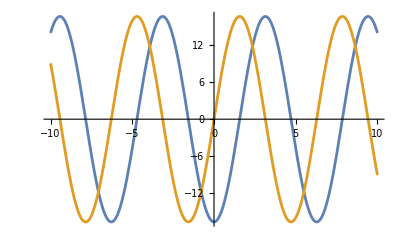

```mathematica
Plot[{16.61321825198459*Sin[t-1.5708],16.61321825198459 Sin[t]},{t,-10,10}]
```

```mathematica
Clear[nk,ζk,Δk]
```

```mathematica
m1k=(nk (-1+ζk^2))/(4 Δk^2+(-1+ζk^2)^2);m2k=(2 Δk*nk)/(4 Δk^2+(-1+ζk^2)^2);
```

```mathematica
(m1k^2+m2k^2)^(1/2)//FullSimplify
```

√(nk^2/(4 Δk^2+(-1+ζk^2)^2))

```mathematica
magkl1mn[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_]:=(Clear[c0,d0,m1k,m2k];
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);(*kr=number of resonance mode, e.g., kr=3*)
delta=oh/wem;
qk=Integrate[realklpt[k,0,θ,φ]*realklpt[k,l,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2Pi}];
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));nk=((ρ1-ρ2)*k*(k+1))/(ρ1(k+1)+ρ2*k)*√((2k+1)/(4*Pi))*qk;fk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;
(*m1k=(nk (-1+ζk^2))/(4 Δk^2+(-1+ζk^2)^2);m2k=(2 Δk*nk)/(4 Δk^2+(-1+ζk^2)^2);*)
magkl=Abs[nk]/(√((1-ζk^2)^2+4*Δk^2))
)
```

```mathematica
psikl1mn[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_]:=(Clear[tt,wem,psi];
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);(*kr=number of resonance mode, e.g., kr=3*)
delta=oh/wem;
qk=Integrate[realklpt[k,0,θ,φ]*realklpt[k,l,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2Pi}];
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));nk=((ρ1-ρ2)*k*(k+1))/(ρ1(k+1)+ρ2*k)*√((2k+1)/(4*Pi))*qk;fk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;

m1k=(nk (-1+ζk^2))/(4 Δk^2+(-1+ζk^2)^2);m2k=(2 Δk*nk)/(4 Δk^2+(-1+ζk^2)^2);
psi=ArcTan[m2k,m1k])
```

```mathematica
psikl1mn[oh_,k_,l_,kr_]:=(Clear[tt,wem,psi];
wem=(kr^2-1)(kr+2);
Δk=oh/(√wem)*(k+1)*(k+2);ζk=√(1/wem(k^2-1)(k+2));
qkl=Integrate[Cos[θ]*realkl[k,l]*Sin[θ],{θ,0,Pi/2},{φ,0,2Pi}];

m1k=(nk (-1+ζk^2))/(4 Δk^2+(-1+ζk^2)^2);m2k=(2 Δk*nk)/(4 Δk^2+(-1+ζk^2)^2);
psi=ArcTan[d2,-d1])
```

```mathematica
Coefficient[(-nk Cos[t]+nk ζk^2 Cos[t]+2 ddk nkk Sin[t])/(1+4 ddk^2-2 zk^2+zk^4),Sin[t]]
```

```mathematica
bkl0fun[0.027,0.7,0.5,0.7,0.5,2,0,2,0]
```

0.+cmn Cos[1. t]-6.69888 Sin[t]+dmn Sin[1. t]

```mathematica
wesol[ρ1_,ρ2_,k_]:=we/.Solve[(k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)we)==1,we]
```

```mathematica
wesol[0.86,0.14,2]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{8.39161}

```mathematica
Integrate[realkl[3,0]*realkl[3,0]*Sin[θ],{θ,0,Pi},{φ,0,2Pi}]
```

1

```mathematica
bkl1trans[oh_,we_,ρ1_,ρ2_,μ1_,μ2_,k_,l_]:=(
(*kr=number of resonance mode, e.g., kr=3*)
delta=oh/we;
qk=Integrate[realklpt[k,0,θ,φ]*realklpt[k,l,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2Pi}];(*factor of 2 in front because of the inner product over hemisphere*)
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)we));nk=((ρ2-ρ1)*k*(k+1))/(ρ1(k+1)+ρ2*k)*√((2k+1)/(4*Pi))*qk;gk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*gk;
m1k=If[Δk==0&&ζk==1,0,(nk (-1+ζk))/(4 Δk^2+(-1+ζk)^2)];
m2k=If[Δk==0&&ζk==1,0,(2 Δk*nk)/(4 Δk^2+(-1+ζk)^2)];(*

icsol={ckl,dkl}/.Flatten[Solve[{(ⅇ^(-t (Δk+√(Δk^2-ζk^2))) (ckl+dkl ⅇ^(2 t √(Δk^2-ζk^2)))+m1k*Cos[t]+m2k*Sin[t]/.t->0)==ic1,(D[ⅇ^(-t (Δk+√(Δk^2-ζk^2))) (ckl+dkl ⅇ^(2 t √(Δk^2-ζk^2)))+m1k*Cos[t]+m2k*Sin[t],t]/.t->0)==ic2},{ckl,dkl}]];*)
bkl1ivpsol=m1k*Sin[t]+m2k*Cos[t];
bkl1l2norm=(Integrate[(bkl1ivpsol)^2,{t,0,2Pi}])^(1/2)/(2Pi)//Chop

(*bkl0amp=(2 (1+k) qk (2 Δk Cos[t]+Sin[t]-ζk^2 Sin[t]))/(1+4 Δk^2-2 ζk^2+ζk^4)*)(*before forcing sign correction*)(*after forcing sign correction*)
)
```

```mathematica
[oh_,we_,ρ1_,ρ2_,μ1_,μ2_,k_,l_]
```

```mathematica
bkl1trans[0.01,10,0.7,0.3,0.5,0.5,2,0];nk
```

-0.560696

```mathematica
bkl1trans[0.01,10,0.7,0.3,0.5,0.5,3,0];nk
```

-0.968241

```mathematica
bkl1trans[0.01,10,0.7,0.3,0.5,0.5,4,0];nk
```

-1.44048

```mathematica
bkl1trans[0.01,10,0.7,0.3,0.5,0.5,3,0];nk
```

```mathematica
bkl1trans[0.01,10,0.7,0.3,0.5,0.5,5,0];nk
```

-1.96969

```mathematica
list2=Table[bkl1trans[0.01,we,0.7,0.3,0.5,0.5,2,0],{we,0.1,100,1}];
```

```mathematica
list3=Table[bkl1trans[0.01,we,0.7,0.3,0.5,0.5,3,0],{we,0.1,100,1}];
```

```mathematica
list4=Table[bkl1trans[0.01,we,0.7,0.3,0.5,0.5,4,0],{we,0.1,200,1}];
```

```mathematica
list5=Table[bkl1trans[0.01,we,0.7,0.3,0.5,0.5,5,0],{we,0.1,200,1}];
```

```mathematica
1
```

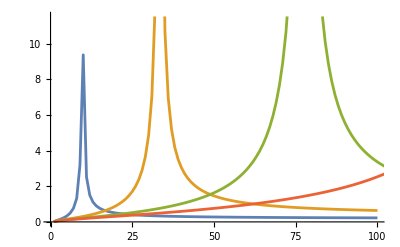

```mathematica
ListLinePlot[{list2,list3,list4,list5},PlotRange->{{0,100},Automatic}]
```

```mathematica
ζk
```

0.572075

```mathematica
nk
```

-0.968241

```mathematica
bkl0fun[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_]:=(Clear[cmn,dmn,m1k,m2k];
wer=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);(*kr=number of resonance mode, e.g., kr=3*)
delta=oh/wer;
qk=Integrate[realklpt[k,0,θ,φ]*realklpt[k,l,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2Pi}];
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wer));nk=((ρ2-ρ1)*k*(k+1))/(ρ1(k+1)+ρ2*k)*√((2k+1)/(4*Pi))*qk;gk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*gk;
(*m1k=If[Δk==0&&ζk==1,0,(nk (-1+ζk))/(4 Δk^2+(-1+ζk)^2)];*)
m1k=(nk (-1+ζk))/(4 Δk^2+(-1+ζk)^2);m2k=(2 Δk*nk)/(4 Δk^2+(-1+ζk)^2);(*
m2k=If[Δk==0&&ζk==1,0,(2 Δk*nk)/(4 Δk^2+(-1+ζk)^2)];*)

(*If[k==kr,ζk=1];*)
bkl0amp=If[k==m&&l==n,(cmn*Cos[ζk*t]+dmn*Sin[ζk*t])+m1k*Cos[t]+m2k*Sin[t],m1k*Cos[t]+m2k*Sin[t]])(*leading order amplitude of different modes at the resonance frequency kr*)
```

```mathematica
magkl1mn[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_]:=(
wer=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);(*kr=number of resonance mode, e.g., kr=3*)
delta=oh/wer;
qkl=Integrate[realklpt[k,0,θ,φ]*realklpt[k,l,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2Pi}];
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wer));nk=((ρ2-ρ1)*k*(k+1))/(ρ1(k+1)+ρ2*k)*√((2k+1)/(4*Pi))*qk;gk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*gk;
magkl=(2(k+1)*Abs[qkl])/(√((1-ζk^2)^2+4*Δk^2))
)
```

```mathematica
psikl1mn[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_]:=(Clear[tt,wem,psi];
wer=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);(*kr=number of resonance mode, e.g., kr=3*)
delta=oh/wer;
qkl=Integrate[realklpt[k,0,θ,φ]*realklpt[k,l,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2Pi}];
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wer));nk=((ρ2-ρ1)*k*(k+1))/(ρ1(k+1)+ρ2*k)*√((2k+1)/(4*Pi))*qk;gk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*gk;

d1=Coefficient[-2*Sign[qkl]*(k+1)((2 Δk Cos[tt]+Sin[tt]-ζk^2 Sin[tt])/(1+4 Δk^2-2 ζk^2+ζk^4)),Cos[tt]];
d2=Coefficient[-2*Sign[qkl]*(k+1)((2 Δk Cos[tt]+Sin[tt]-ζk^2 Sin[tt])/(1+4 Δk^2-2 ζk^2+ζk^4)),Sin[tt]];
psi=ArcTan[d2,-d1])
```

```mathematica
psikl1mn[0.02,0.7,0.3,0.2,0.8,2,0,2,0]
```

1.5708

### O(e) response

```mathematica
Clear[c0,d0,d2,d3,d4,d5,d6,b020,b021,b021t,b021tt,b121,b121t,b121tt,b020t,b020tt,b030,b030t,b030tt,b022,b022t,b022tt,b051,b051t,b051tt,b053,b053t,b053tt,b055,b055t,b055tt,b031,b031t,b031tt,b033,b033t,b033tt,b040,b040t,b040tt,b042,b042t,b042tt,b044,b044t,b044tt,b060,b060t,b060tt,b062,b062t,b062tt,b064,b064t,b064tt,b071,b071t,b071tt,b073,b073t,b073tt,delta,wer,b120,b122,b131,b133,b140,b142,b144,b151,b153,b155,b160,b162,b164,b171,b120t,b122t,b131t,b133t,b140t,b142t,b144t,b151t,b153t,b155t,b160t,b162t,b164t,b171t,b120tt,b122tt,b131tt,b133tt,b140tt,b142tt,b144tt,b151tt,b153tt,b155tt,b160tt,b162tt,b164tt,b171tt,p200t,p310t,p33t,p400t,p510t,p600t,p220t,p420t,p440t,p530t,p550t,p710t,p620t,p640t,p200,p310,p400,p510,p600,k121,k120,k130,n120,n121,n130,k121t,k120t,k130t];
```

```mathematica
(*the potential phi has two subscripts. first subscript=1 is inner fluid, =2 is outer fluid.*)
```

```mathematica
magkl1mn[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_]
```

```mathematica
Clear[b201,b211,b301];
```

#### Set physical parameters here

```mathematica
ohn=(0.001+0.0024)/(√(1040+6440)*2.26*10^-3*0.403)
```

0.0431633

```mathematica
rho2=1040*1/(1040+6440)//N
```

0.139037

```mathematica
rho1=6440*1/(1040+6440)//N
```

0.860963

```mathematica
mu2=0.001*1/(0.001+0.0024)//N
```

0.294118

```mathematica
mu1=0.0024*1/(0.001+0.0024)//N
```

0.705882

```mathematica
Clear[etaa1,fi11,fi21]
```

```mathematica
bkl0fun[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,m_,n_]
```

```mathematica
b201[s_]:=bkl0fun[ohn,rho1,rho2,mu1,mu2,2,0,2,1];
```

```mathematica
ohn=0.43 (*10 times higher than experiment*);rho2=.14;rho1=0.86;mu1=0.71;mu2=0.29;

b201[s_]:=bkl0fun[ohn,rho1,rho2,mu1,mu2,2,0,2,1];
b211[s_]:=c21*Cos[s]+d21*Sin[s];
b301[s_]:=bkl0fun[ohn,rho1,rho2,mu1,mu2,3,0,2,1];

etaa1[a_,b_,c_]:=b201[c]*realklpt[2,0,a,b]+b211[c]*realklpt[2,1,a,b]+b301[c]*realklpt[3,0,a,b]

fi11[rr_,a_,b_,c_]:=D[b201[c],c]/2*rr^2*realklpt[2,0,a,b]+D[b211[c],c]/2*rr^2*realklpt[2,1,a,b]+D[b301[c],c]/3*rr^3*realklpt[3,0,a,b]

fi21[rr_,a_,b_,c_]:=-D[b201[c],c]/(3 rr^3)*realklpt[2,0,a,b]-D[b211[c],c]/(4 rr^4)*realklpt[2,1,a,b]-D[b301[c],c]/(5 rr^5)*realklpt[3,0,a,b]
```

```mathematica
fi21[1,t,p,tt]
```

1/8 √(15/π) Cos[p] Cos[t] Sin[t] (d21 Cos[tt]-c21 Sin[tt])

#### kinematic equation

```mathematica
kinematicoe2=Coefficient[kinematicstpertr1,e^2]
```

η2[θ,φ,t]+Csc[θ]^2 η1^(0,1,0)[θ,φ,t] ϕ11^(0,0,1,0)[1,θ,φ,t]+η1^(1,0,0)[θ,φ,t] ϕ11^(0,1,0,0)[1,θ,φ,t]-ϕ12^(1,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]

```mathematica
kkl1fun=Csc[θ]^2 Derivative[0,1,0][η1][θ,φ,t] Derivative[0,0,1,0][ϕ11][1,θ,φ,t]+Derivative[1,0,0][η1][θ,φ,t] Derivative[0,1,0,0][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]]} //Chop
```

-1/4 √(15/π) Cos[2 θ] Cos[φ] (d21 Cos[t]-c21 Sin[t]) (-1/2 √(15/π) Cos[2 θ] Cos[φ] (c21 Cos[t]+d21 Sin[t])+4.48455 Cos[t] Cos[θ] Sin[θ]+1/4 √(7/π) (-0.187401 Cos[t]+0.554315 Sin[t]) (3 Sin[θ]-15 Cos[θ]^2 Sin[θ]))+1/4 √(15/π) Cos[φ] (d21 Cos[t]-c21 Sin[t]) (-0.747425 Cos[t] (-1+3 Cos[θ]^2)+1/4 √(7/π) (-3 Cos[θ]+5 Cos[θ]^3) (-0.187401 Cos[t]+0.554315 Sin[t])-1/2 √(15/π) Cos[θ] Cos[φ] (c21 Cos[t]+d21 Sin[t]) Sin[θ]) Sin[2 θ]+(15 Csc[θ]^2 (d21 Cos[t]-c21 Sin[t]) (c21 Cos[t]+d21 Sin[t]) Sin[2 θ]^2 Sin[φ]^2)/(32 π)

```mathematica
k201ff=Integrate[TrigReduce[kkl1fun]*realklpt[2,0,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify
```

ⅇ^((0.-2. ⅈ) t) (c21^2 ((2.08167×10^-17-0.011264 ⅈ)-(1.38778×10^-17-0.011264 ⅈ) ⅇ^((0.+4. ⅈ) t))+d21^2 ((-2.08167×10^-17+0.011264 ⅈ)+(1.38778×10^-17-0.011264 ⅈ) ⅇ^((0.+4. ⅈ) t))+c21 d21 ((0.022528+4.16334×10^-17 ⅈ)+(0.022528+2.77556×10^-17 ⅈ) ⅇ^((0.+4. ⅈ) t)))

```mathematica
k211ff=Integrate[TrigReduce[kkl1fun]*realklpt[2,1,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

-0.0533875 d21-0.0533875 d21 Cos[2. t]+0.106775 c21 Cos[t] Sin[t]

```mathematica
k301ff=Integrate[TrigReduce[kkl1fun]*realklpt[3,0,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

ⅇ^((0.-2. ⅈ) t) (d21^2 ((0.+1.5763 ⅈ)-(0.+1.5763 ⅈ) ⅇ^((0.+4. ⅈ) t))+c21^2 ((0.-1.5763 ⅈ)+(0.+1.5763 ⅈ) ⅇ^((0.+4. ⅈ) t))+(6.30522 c21^2-6.30522 d21^2) ⅇ^((0.+2. ⅈ) t) Cos[t] Sin[t])

#### NO penetration

```mathematica
nopenoe2=Coefficient[nopenstpertr1,e^2]
```

-ϕ12^(1,0,0,0)[1,θ,φ,t]+ϕ22^(1,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]

```mathematica
lkl1fun=η1[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]]}
```

-3/2 √(15/π) Cos[φ] (d21 Cos[t]-c21 Sin[t]) (1/4 √(5/π) (-1+3 Cos[θ]^2) (-2.36983 Cos[t]-1.30881×10^-15 Sin[t])+1/4 √(7/π) (-3 Cos[θ]+5 Cos[θ]^3) (-0.187401 Cos[t]+0.554315 Sin[t])-1/2 √(15/π) Cos[θ] Cos[φ] (c21 Cos[t]+d21 Sin[t]) Sin[θ]) Sin[2 θ]

```mathematica
l201ff=Integrate[TrigReduce[lkl1fun]*realklpt[2,0,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

-2.66112 (-0.203175 c21 d21 Cos[2. t]+(0.101587 c21^2-0.101587 d21^2) Sin[2. t])

```mathematica
realklpt[3,0,t,p]
```

1/4 √(7/π) (-3 Cos[t]+5 Cos[t]^3)

```mathematica
l211ff=Integrate[TrigReduce[lkl1fun]*realklpt[2,1,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

-0.64065 d21-0.64065 d21 Cos[2. t]+1.2813 c21 Cos[t] Sin[t]

```mathematica
realklpt[3,0,θ,φ]
```

1/4 √(7/π) (-3 Cos[θ]+5 Cos[θ]^3)

```mathematica
l301ff=Integrate[TrigReduce[lkl1fun]*realklpt[3,0,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

0.

#### normal stress equation

```mathematica
Clear[We]
```

```mathematica
normalstoe2=Coefficient[normalstpertr1,e^2]
```

(-2 (η1[θ,φ,t]^2-η2[θ,φ,t])+Csc[θ]^2 η2^(0,2,0)[θ,φ,t]+Cot[θ] η2^(1,0,0)[θ,φ,t]+2 η1[θ,φ,t] (-Csc[θ]^2 η1^(0,2,0)[θ,φ,t]-Cot[θ] η1^(1,0,0)[θ,φ,t]-η1^(2,0,0)[θ,φ,t])+η2^(2,0,0)[θ,φ,t])/We+ρ1 (ϕ12^(0,0,0,1)[1,θ,φ,t]+1/2 (Csc[θ]^2 (ϕ11^(0,0,1,0)[1,θ,φ,t])^2+(ϕ11^(0,1,0,0)[1,θ,φ,t])^2+(ϕ11^(1,0,0,0)[1,θ,φ,t])^2)+η1[θ,φ,t] ϕ11^(1,0,0,1)[1,θ,φ,t])-1/2 ρ2 (2 ϕ22^(0,0,0,1)[1,θ,φ,t]+Csc[θ]^2 (ϕ21^(0,0,1,0)[1,θ,φ,t])^2+(ϕ21^(0,1,0,0)[1,θ,φ,t])^2+(ϕ21^(1,0,0,0)[1,θ,φ,t])^2+2 η1[θ,φ,t] ϕ21^(1,0,0,1)[1,θ,φ,t])

```mathematica
nkl1fun=(-2 (η1[θ,φ,t]^2)+2 η1[θ,φ,t] (-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t]-Cot[θ] Derivative[1,0,0][η1][θ,φ,t]-Derivative[2,0,0][η1][θ,φ,t]))/We+ρ1 (1/2 (Csc[θ]^2 (Derivative[0,0,1,0][ϕ11][1,θ,φ,t])^2+(Derivative[0,1,0,0][ϕ11][1,θ,φ,t])^2+(Derivative[1,0,0,0][ϕ11][1,θ,φ,t])^2)+η1[θ,φ,t] Derivative[1,0,0,1][ϕ11][1,θ,φ,t])-1/2 ρ2 (Csc[θ]^2 (Derivative[0,0,1,0][ϕ21][1,θ,φ,t])^2+(Derivative[0,1,0,0][ϕ21][1,θ,φ,t])^2+(Derivative[1,0,0,0][ϕ21][1,θ,φ,t])^2+2 η1[θ,φ,t] Derivative[1,0,0,1][ϕ21][1,θ,φ,t])/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]]}
```

1/We(-2 (1/4 √(5/π) (-1+3 Cos[θ]^2) (-2.36983 Cos[t]-1.30881×10^-15 Sin[t])+1/4 √(7/π) (-3 Cos[θ]+5 Cos[θ]^3) (-0.187401 Cos[t]+0.554315 Sin[t])-1/2 √(15/π) Cos[θ] Cos[φ] (c21 Cos[t]+d21 Sin[t]) Sin[θ])^2+2 (1/4 √(5/π) (-1+3 Cos[θ]^2) (-2.36983 Cos[t]-1.30881×10^-15 Sin[t])+1/4 √(7/π) (-3 Cos[θ]+5 Cos[θ]^3) (-0.187401 Cos[t]+0.554315 Sin[t])-1/2 √(15/π) Cos[θ] Cos[φ] (c21 Cos[t]+d21 Sin[t]) Sin[θ]) (3/2 √(5/π) Cos[θ]^2 (-2.36983 Cos[t]-1.30881×10^-15 Sin[t])-3/2 √(5/π) (-2.36983 Cos[t]-1.30881×10^-15 Sin[t]) Sin[θ]^2-1/4 √(7/π) (-0.187401 Cos[t]+0.554315 Sin[t]) (3 Cos[θ]-15 Cos[θ]^3+30 Cos[θ] Sin[θ]^2)-Cot[θ] (-1/2 √(15/π) Cos[2 θ] Cos[φ] (c21 Cos[t]+d21 Sin[t])-3/2 √(5/π) Cos[θ] (-2.36983 Cos[t]-1.30881×10^-15 Sin[t]) Sin[θ]+1/4 √(7/π) (-0.187401 Cos[t]+0.554315 Sin[t]) (3 Sin[θ]-15 Cos[θ]^2 Sin[θ]))-√(15/π) Cos[φ] (c21 Cos[t]+d21 Sin[t]) Sin[2 θ]-1/4 √(15/π) Cos[φ] Csc[θ]^2 (c21 Cos[t]+d21 Sin[t]) Sin[2 θ]))-1/2 ρ2 ((15 Cos[2 θ]^2 Cos[φ]^2 (d21 Cos[t]-c21 Sin[t])^2)/(64 π)-1/2 √(15/π) Cos[φ] (-c21 Cos[t]-d21 Sin[t]) (1/4 √(5/π) (-1+3 Cos[θ]^2) (-2.36983 Cos[t]-1.30881×10^-15 Sin[t])+1/4 √(7/π) (-3 Cos[θ]+5 Cos[θ]^3) (-0.187401 Cos[t]+0.554315 Sin[t])-1/2 √(15/π) Cos[θ] Cos[φ] (c21 Cos[t]+d21 Sin[t]) Sin[θ]) Sin[2 θ]+(15 Cos[φ]^2 (d21 Cos[t]-c21 Sin[t])^2 Sin[2 θ]^2)/(16 π)+(15 Csc[θ]^2 (d21 Cos[t]-c21 Sin[t])^2 Sin[2 θ]^2 Sin[φ]^2)/(256 π))+ρ1 (-1/4 √(15/π) Cos[φ] (-c21 Cos[t]-d21 Sin[t]) (1/4 √(5/π) (-1+3 Cos[θ]^2) (-2.36983 Cos[t]-1.30881×10^-15 Sin[t])+1/4 √(7/π) (-3 Cos[θ]+5 Cos[θ]^3) (-0.187401 Cos[t]+0.554315 Sin[t])-1/2 √(15/π) Cos[θ] Cos[φ] (c21 Cos[t]+d21 Sin[t]) Sin[θ]) Sin[2 θ]+1/2 ((15 Cos[2 θ]^2 Cos[φ]^2 (d21 Cos[t]-c21 Sin[t])^2)/(16 π)+(15 Cos[φ]^2 (d21 Cos[t]-c21 Sin[t])^2 Sin[2 θ]^2)/(16 π)+(15 Csc[θ]^2 (d21 Cos[t]-c21 Sin[t])^2 Sin[2 θ]^2 Sin[φ]^2)/(64 π)))

```mathematica
nkl1fun1=(-2 (η1[θ,φ,t]^2)(*+2 η1[θ,φ,t] (-Csc[θ]^2 η1^(0,2,0)[θ,φ,t]-Cot[θ] η1^(1,0,0)[θ,φ,t]-η1^(2,0,0)[θ,φ,t])*))/We(*+ρ1 (1/2 (Csc[θ]^2 (ϕ11^(0,0,1,0)[1,θ,φ,t])^2+(ϕ11^(0,1,0,0)[1,θ,φ,t])^2+(ϕ11^(1,0,0,0)[1,θ,φ,t])^2)+η1[θ,φ,t] ϕ11^(1,0,0,1)[1,θ,φ,t])-1/2 ρ2 (Csc[θ]^2 (ϕ21^(0,0,1,0)[1,θ,φ,t])^2+(ϕ21^(0,1,0,0)[1,θ,φ,t])^2+(ϕ21^(1,0,0,0)[1,θ,φ,t])^2+2 η1[θ,φ,t] ϕ21^(1,0,0,1)[1,θ,φ,t])*)/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]]}
```

-(2 (1/4 √(5/π) (-1+3 Cos[θ]^2) (-2.36983 Cos[t]-1.30881×10^-15 Sin[t])+1/4 √(7/π) (-3 Cos[θ]+5 Cos[θ]^3) (-0.187401 Cos[t]+0.554315 Sin[t])-1/2 √(15/π) Cos[θ] Cos[φ] (c21 Cos[t]+d21 Sin[t]) Sin[θ])^2)/We

```mathematica
n201ff1=Integrate[TrigReduce[nkl1fun1]*realklpt[2,0,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

-1/We1.1653 (0.918004+0.0773295 c21^2+0.0773295 d21^2+(0.0555907+0.000995749 ⅈ) ⅇ^((0.-2. ⅈ) t)+0.0386647 c21^2 ⅇ^((0.-2. ⅈ) t)+(0.+0.0773295 ⅈ) c21 d21 ⅇ^((0.-2. ⅈ) t)-0.0386647 d21^2 ⅇ^((0.-2. ⅈ) t)+(0.0555907-0.000995749 ⅈ) ⅇ^((0.+2. ⅈ) t)+0.0386647 c21^2 ⅇ^((0.+2. ⅈ) t)-(0.+0.0773295 ⅈ) c21 d21 ⅇ^((0.+2. ⅈ) t)-0.0386647 d21^2 ⅇ^((0.+2. ⅈ) t)+0.718116 Cos[1. t]^2-0.0639623 Cos[1. t] Sin[1. t]-0.718116 Sin[1. t]^2)

```mathematica
nkl1fun2=((*-2 (η1[θ,φ,t]^2)+*)2 η1[θ,φ,t] (-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t]-Cot[θ] Derivative[1,0,0][η1][θ,φ,t]-Derivative[2,0,0][η1][θ,φ,t]))/We(*+ρ1 (1/2 (Csc[θ]^2 (ϕ11^(0,0,1,0)[1,θ,φ,t])^2+(ϕ11^(0,1,0,0)[1,θ,φ,t])^2+(ϕ11^(1,0,0,0)[1,θ,φ,t])^2)+η1[θ,φ,t] ϕ11^(1,0,0,1)[1,θ,φ,t])-1/2 ρ2 (Csc[θ]^2 (ϕ21^(0,0,1,0)[1,θ,φ,t])^2+(ϕ21^(0,1,0,0)[1,θ,φ,t])^2+(ϕ21^(1,0,0,0)[1,θ,φ,t])^2+2 η1[θ,φ,t] ϕ21^(1,0,0,1)[1,θ,φ,t])*)/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]]}
```

1/We 2 (1/4 √(5/π) (-1+3 Cos[θ]^2) (-2.36983 Cos[t]-1.30881×10^-15 Sin[t])+1/4 √(7/π) (-3 Cos[θ]+5 Cos[θ]^3) (-0.187401 Cos[t]+0.554315 Sin[t])-1/2 √(15/π) Cos[θ] Cos[φ] (c21 Cos[t]+d21 Sin[t]) Sin[θ]) (3/2 √(5/π) Cos[θ]^2 (-2.36983 Cos[t]-1.30881×10^-15 Sin[t])-3/2 √(5/π) (-2.36983 Cos[t]-1.30881×10^-15 Sin[t]) Sin[θ]^2-1/4 √(7/π) (-0.187401 Cos[t]+0.554315 Sin[t]) (3 Cos[θ]-15 Cos[θ]^3+30 Cos[θ] Sin[θ]^2)-Cot[θ] (-1/2 √(15/π) Cos[2 θ] Cos[φ] (c21 Cos[t]+d21 Sin[t])-3/2 √(5/π) Cos[θ] (-2.36983 Cos[t]-1.30881×10^-15 Sin[t]) Sin[θ]+1/4 √(7/π) (-0.187401 Cos[t]+0.554315 Sin[t]) (3 Sin[θ]-15 Cos[θ]^2 Sin[θ]))-√(15/π) Cos[φ] (c21 Cos[t]+d21 Sin[t]) Sin[2 θ]-1/4 √(15/π) Cos[φ] Csc[θ]^2 (c21 Cos[t]+d21 Sin[t]) Sin[2 θ])

```mathematica
add=Chop[nkl1fun2];
```

```mathematica
n201ff2=Integrate[add*realklpt[2,0,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

1/We 1.38824 (-1.82108+0.425976 c21^2-(0.910541-0.0193594 ⅈ) ⅇ^((0.-2. ⅈ) t)+0.212988 c21^2 ⅇ^((0.-2. ⅈ) t)+(0.+0.319482 ⅈ) c21 d21 ⅇ^((0.-2. ⅈ) t)-(0.910541+0.0193594 ⅈ) ⅇ^((0.+2. ⅈ) t)+0.212988 c21^2 ⅇ^((0.+2. ⅈ) t)-(0.+0.319482 ⅈ) c21 d21 ⅇ^((0.+2. ⅈ) t)+(12.4934-0.0730245 c21^2) Cos[t]^2+(-0.6816+0.279927 c21 d21) Cos[t] Sin[t]+(0.893527+0.778928 d21^2) Sin[t]^2)

```mathematica
nkl1fun3=(*((*-2 (η1[θ,φ,t]^2)+*)2 η1[θ,φ,t] (-Csc[θ]^2 η1^(0,2,0)[θ,φ,t]-Cot[θ] η1^(1,0,0)[θ,φ,t]-η1^(2,0,0)[θ,φ,t]))/We*)+ρ1 (1/2 (Csc[θ]^2 (Derivative[0,0,1,0][ϕ11][1,θ,φ,t])^2+(Derivative[0,1,0,0][ϕ11][1,θ,φ,t])^2+(Derivative[1,0,0,0][ϕ11][1,θ,φ,t])^2)+η1[θ,φ,t] Derivative[1,0,0,1][ϕ11][1,θ,φ,t])(*-1/2 ρ2 (Csc[θ]^2 (ϕ21^(0,0,1,0)[1,θ,φ,t])^2+(ϕ21^(0,1,0,0)[1,θ,φ,t])^2+(ϕ21^(1,0,0,0)[1,θ,φ,t])^2+2 η1[θ,φ,t] ϕ21^(1,0,0,1)[1,θ,φ,t])*)/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]]}
```

ρ1 (-1/4 √(15/π) Cos[φ] (-c21 Cos[t]-d21 Sin[t]) (1/4 √(5/π) (-1+3 Cos[θ]^2) (-2.36983 Cos[t]-1.30881×10^-15 Sin[t])+1/4 √(7/π) (-3 Cos[θ]+5 Cos[θ]^3) (-0.187401 Cos[t]+0.554315 Sin[t])-1/2 √(15/π) Cos[θ] Cos[φ] (c21 Cos[t]+d21 Sin[t]) Sin[θ]) Sin[2 θ]+1/2 ((15 Cos[2 θ]^2 Cos[φ]^2 (d21 Cos[t]-c21 Sin[t])^2)/(16 π)+(15 Cos[φ]^2 (d21 Cos[t]-c21 Sin[t])^2 Sin[2 θ]^2)/(16 π)+(15 Csc[θ]^2 (d21 Cos[t]-c21 Sin[t])^2 Sin[2 θ]^2 Sin[φ]^2)/(64 π)))

```mathematica
n201ff3=Integrate[Chop[nkl1fun3]*realklpt[2,0,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

-0.0422399 ρ1 (0.133333 c21^2+0.133333 d21^2+(2. c21^2-2. d21^2) Cos[2. t]+8. c21 d21 Cos[t] Sin[t])

```mathematica
nkl1fun4=(*(*((*-2 (η1[θ,φ,t]^2)+*)2 η1[θ,φ,t] (-Csc[θ]^2 η1^(0,2,0)[θ,φ,t]-Cot[θ] η1^(1,0,0)[θ,φ,t]-η1^(2,0,0)[θ,φ,t]))/We*)+ρ1 (1/2 (Csc[θ]^2 (ϕ11^(0,0,1,0)[1,θ,φ,t])^2+(ϕ11^(0,1,0,0)[1,θ,φ,t])^2+(ϕ11^(1,0,0,0)[1,θ,φ,t])^2)+η1[θ,φ,t] ϕ11^(1,0,0,1)[1,θ,φ,t])*)-1/2 ρ2 (Csc[θ]^2 (Derivative[0,0,1,0][ϕ21][1,θ,φ,t])^2+(Derivative[0,1,0,0][ϕ21][1,θ,φ,t])^2+(Derivative[1,0,0,0][ϕ21][1,θ,φ,t])^2+2 η1[θ,φ,t] Derivative[1,0,0,1][ϕ21][1,θ,φ,t])/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]]}
```

-1/2 ρ2 ((15 Cos[2 θ]^2 Cos[φ]^2 (d21 Cos[t]-c21 Sin[t])^2)/(64 π)-1/2 √(15/π) Cos[φ] (-c21 Cos[t]-d21 Sin[t]) (1/4 √(5/π) (-1+3 Cos[θ]^2) (-2.36983 Cos[t]-1.30881×10^-15 Sin[t])+1/4 √(7/π) (-3 Cos[θ]+5 Cos[θ]^3) (-0.187401 Cos[t]+0.554315 Sin[t])-1/2 √(15/π) Cos[θ] Cos[φ] (c21 Cos[t]+d21 Sin[t]) Sin[θ]) Sin[2 θ]+(15 Cos[φ]^2 (d21 Cos[t]-c21 Sin[t])^2 Sin[2 θ]^2)/(16 π)+(15 Csc[θ]^2 (d21 Cos[t]-c21 Sin[t])^2 Sin[2 θ]^2 Sin[φ]^2)/(256 π))

```mathematica
n201ff4=Integrate[Chop[nkl1fun4]*realklpt[2,0,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

0.035904 ρ2 (0.509804 c21^2+0.509804 d21^2+(2. c21^2-2. d21^2) Cos[2. t]+8. c21 d21 Cos[t] Sin[t])

```mathematica
n201ff=n201ff1+n201ff2+n201ff3+n201ff4//Simplify
```

-1/We0.0844799 (42.5883-5.93333 c21^2+1.06667 d21^2+(15.7296-0.304395 ⅈ) ⅇ^((0.-2. ⅈ) t)-2.96667 c21^2 ⅇ^((0.-2. ⅈ) t)-(0.+4.18333 ⅈ) c21 d21 ⅇ^((0.-2. ⅈ) t)-0.533333 d21^2 ⅇ^((0.-2. ⅈ) t)+(15.7296+0.304395 ⅈ) ⅇ^((0.+2. ⅈ) t)-2.96667 c21^2 ⅇ^((0.+2. ⅈ) t)+(0.+4.18333 ⅈ) c21 d21 ⅇ^((0.+2. ⅈ) t)-0.533333 d21^2 ⅇ^((0.+2. ⅈ) t)+0.0666667 c21^2 We ρ1+0.0666667 d21^2 We ρ1-0.216667 c21^2 We ρ2-0.216667 d21^2 We ρ2+(-205.302+1.2 c21^2) Cos[t]^2+9.90554 Cos[1. t]^2+1. c21^2 We ρ1 Cos[2. t]-1. d21^2 We ρ1 Cos[2. t]-0.85 c21^2 We ρ2 Cos[2. t]+0.85 d21^2 We ρ2 Cos[2. t]+(11.2006+c21 d21 (-4.6+4. We ρ1-3.4 We ρ2)) Cos[t] Sin[t]-14.6832 Sin[t]^2-12.8 d21^2 Sin[t]^2-9.90554 Sin[1. t]^2-0.441141 Sin[2. t])

```mathematica
n211ff1=Integrate[Chop[nkl1fun1]*realklpt[2,1,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

(0.8542 c21 Cos[t]^2+0.8542 d21 Cos[t] Sin[t])/We

```mathematica
n211ff2=Integrate[Chop[nkl1fun2]*realklpt[2,1,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

(-5.1252 c21 Cos[t]^2+8.06819 d21 Cos[t] Sin[t]-6.5967 d21 Sin[2. t])/We

```mathematica
n211ff3=Integrate[Chop[nkl1fun3]*realklpt[2,1,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

0.125 ρ1 (1.7084 c21 Cos[t]^2-5.01843 d21 Cos[t] Sin[t]+3.36341 d21 Sin[2. t])

```mathematica
n211ff4=Integrate[Chop[nkl1fun4]*realklpt[2,1,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

0.000679236 ρ2 (-314.397 c21 Cos[t]^2+923.542 d21 Cos[t] Sin[t]-618.97 d21 Sin[2. t])

```mathematica
n211ff=n211ff1+n211ff2+n211ff3+n211ff4//Simplify
```

(c21 (-4.271+0.21355 We ρ1-0.21355 We ρ2) Cos[t]^2+d21 (8.92239-0.627303 We ρ1+0.627303 We ρ2) Cos[t] Sin[t]+d21 (-6.5967+0.420427 We ρ1-0.420427 We ρ2) Sin[2. t])/We

```mathematica
n301ff1=Integrate[Chop[nkl1fun1]*realklpt[3,0,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

(Cos[t] (-0.298813 Cos[t]+0.883859 Sin[t]))/We

```mathematica
n301ff2=Integrate[Chop[nkl1fun2]*realklpt[3,0,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

(2.73765 (ⅇ^((0.-2. ⅈ) t) ((-0.0849897+0.251391 ⅈ)-0.169979 ⅇ^((0.+2. ⅈ) t)-(0.0849897+0.251391 ⅈ) ⅇ^((0.+4. ⅈ) t))+1.3223 Cos[t]^2-3.91124 Cos[t] Sin[t]))/We

```mathematica
n301ff3=Integrate[Chop[nkl1fun3]*realklpt[3,0,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

0

```mathematica
n301ff4=Integrate[Chop[nkl1fun4]*realklpt[3,0,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

0

```mathematica
n301ff=n301ff1+n301ff2+n301ff3+n301ff4//Simplify
```

(-0.465345-(0.232672-0.688222 ⅈ) ⅇ^((0.-2. ⅈ) t)-(0.232672+0.688222 ⅈ) ⅇ^((0.+2. ⅈ) t)+3.32119 Cos[t]^2-9.82377 Cos[t] Sin[t])/We

```mathematica
l201ff//ExpToTrig//FullSimplify//Chop
```

0.540671 c21 d21 Cos[2. t]-0.270336 (c21^2-1. d21^2) Sin[2. t]

```mathematica
k201ff//Chop
```

(-0.0647184+0.0450559 c21 d21) Cos[2. t]+(-1002.52-0.022528 c21^2+0.022528 d21^2) Sin[2. t]

```mathematica
l201ff//Expand//N
```

0.540671 c21 d21 Cos[2. t]-0.270336 c21^2 Sin[2. t]+0.270336 d21^2 Sin[2. t]

```mathematica
l201ff//Chop
```

0.540671 c21 d21 Cos[2. t]-0.270336 (c21^2-1. d21^2) Sin[2. t]

```mathematica
l201ff
```

0.540671 c21 d21 Cos[2. t]-0.270336 (c21^2-1. d21^2) Sin[2. t]

-1.42357-0.11264 c21^2-0.11264 d21^2+0.0118154 c21^2 ρ1+0.0118154 d21^2 ρ1-0.0383999 c21^2 ρ2-0.0383999 d21^2 ρ2+(0.119148+d21^2 (0.219367+0.0353292 ρ1-0.0300298 ρ2)+c21^2 (-0.219367-0.0353292 ρ1+0.0300298 ρ2)+c21 d21 (-0.332241-0.0579305 ρ1+0.0492409 ρ2)) Cos[2 t]+(-0.317883+c21^2 (0.16612+0.0289652 ρ1-0.0246205 ρ2)+d21^2 (-0.16612-0.0289652 ρ1+0.0246205 ρ2)+c21 d21 (-0.438735-0.0706584 ρ1+0.0600597 ρ2)) Sin[2 t]

```mathematica
l201ff//Chop
```

-2.66112 (-0.203175 c21 d21 Cos[2. t]+(0.101587 c21^2-0.101587 d21^2) Sin[2. t])

```mathematica
b202fun[oh_,ρ1_,ρ2_,μ1_,μ2_,m_,n_]:=(Clear[f1,f2,f3,f4,f5,Δk,k,f201,wem,We];k=2;
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);(*kr=number of resonance mode, e.g., kr=3*)
delta=oh/wem;We=wem;
qk=1;
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));nk=((ρ2-ρ1)*k*(k+1))/(ρ1(k+1)+ρ2*k)*√((2k+1)/(4*Pi))*qk;gk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*gk;hk=2*delta*μ2*(k+2);
k201ff=ⅇ^((0.-2. ⅈ) t) (d21^2 ((0.+0.01126398447330427 ⅈ)-(0.+0.01126398447330427 ⅈ) ⅇ^((0.+4. ⅈ) t))+c21^2 ((0.-0.01126398447330427 ⅈ)+(0.+0.01126398447330427 ⅈ) ⅇ^((0.+4. ⅈ) t))+c21 d21 (0.02252796894660854+0.02252796894660854 ⅇ^((0.+4. ⅈ) t)));
n201ff=-0.010067186123015708 (42.5882873129665-5.933333333333332 c21^2+1.0666666666666664 d21^2+(15.72957219316835-0.3043953730784458 ⅈ) ⅇ^((0.-2. ⅈ) t)-2.966666666666666 c21^2 ⅇ^((0.-2. ⅈ) t)-(0.+4.183333333333331 ⅈ) c21 d21 ⅇ^((0.-2. ⅈ) t)-0.5333333333333332 d21^2 ⅇ^((0.-2. ⅈ) t)+(15.72957219316835+0.3043953730784447 ⅈ) ⅇ^((0.+2. ⅈ) t)-2.966666666666666 c21^2 ⅇ^((0.+2. ⅈ) t)+(0.+4.183333333333331 ⅈ) c21 d21 ⅇ^((0.+2. ⅈ) t)-0.5333333333333332 d21^2 ⅇ^((0.+2. ⅈ) t)+0.55944055944056 c21^2 ρ1+0.55944055944056 d21^2 ρ1-1.81818181818182 c21^2 ρ2-1.81818181818182 d21^2 ρ2+(-205.3016548191142+1.200000000000004 c21^2) Cos[t]^2+9.905544640724099 Cos[1. t]^2+8.391608391608392 c21^2 ρ1 Cos[2. t]-8.391608391608392 d21^2 ρ1 Cos[2. t]-7.132867132867134 c21^2 ρ2 Cos[2. t]+7.132867132867134 d21^2 ρ2 Cos[2. t]+(11.200618598504315+c21 d21 (-4.600000000000008+33.56643356643357 ρ1-28.531468531468526 ρ2)) Cos[t] Sin[t]-14.68317943086845 Sin[t]^2-12.799999999999988 d21^2 Sin[t]^2-9.905544640724097 Sin[1. t]^2-0.441141005178042 Sin[2. t]);
l201ff=-2.661116331818138 (-0.20317460317460323 c21 d21 Cos[2. t]+(0.1015873015873016 c21^2-0.1015873015873016 d21^2) Sin[2. t]);
ff20=Integrate[(SphericalHarmonicY[2,0,θ,φ])*Sin[θ]*Conjugate[SphericalHarmonicY[2,0,θ,φ]],{θ,0,Pi/2},{φ,0,2Pi}];(*
ff30=Integrate[(SphericalHarmonicY[3,0,θ,φ])*Cos[θ]*Sin[θ]*Conjugate[SphericalHarmonicY[2,0,θ,φ]],{θ,0,Pi/2},{φ,0,2Pi}];*)
f201=TrigReduce[nk*(b201[t]*Sin[t]*ff20(*+b301[t]*Sin[t]*ff30*))-D[k201ff,t]-2*Δk*k201ff-fk*n201ff-gk*D[l201ff,t]-hk*l201ff];
f1=Integrate[(1/(2Pi))*f201,{t,-Pi,Pi}];
f4=Integrate[(1/Pi)*f201*Cos[2t],{t,-Pi,Pi}];f5=Integrate[(1/Pi)*f201*Sin[2t],{t,-Pi,Pi}];
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);
Δk=delta*(k+1)*(k+2);ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));
b201sol=f1/ζk^2+((-4 f5 Δk+f4 (-4+ζk^2)) Cos[2 t]+(4 f4 Δk+f5 (-4+ζk^2)) Sin[2 t])/(16 Δk^2+(-4+ζk^2)^2)//TrigReduce//Simplify//Chop)
```

```mathematica
b202fun[0.43,0.86,0.14,0.71,0.29,2,1]
```

-1.42357-0.107855 c21^2-0.107855 d21^2+(0.119148-0.245546 c21^2-0.375167 c21 d21+0.245546 d21^2) Cos[2 t]+(-0.317883+0.187584 c21^2-0.491093 c21 d21-0.187584 d21^2) Sin[2 t]

```mathematica
b211[t]
```

c21 Cos[t]+d21 Sin[t]

```mathematica
l211ff
```

-0.64065 d21-0.64065 d21 Cos[2. t]+1.2813 c21 Cos[t] Sin[t]

```mathematica
k211ff
```

-0.0533875 d21-0.0533875 d21 Cos[2. t]+0.106775 c21 Cos[t] Sin[t]

```mathematica
b212fun[oh_,ρ1_,ρ2_,μ1_,μ2_,m_,n_]:=(Clear[f1,f2,f3,f4,f5,Δk,k,f201,wem,We,k201ff,n201ff,l201ff];k=2;
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);(*kr=number of resonance mode, e.g., kr=3*)
delta=oh/wem;We=wem;
qk=1;
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));nk=((ρ2-ρ1)*k*(k+1))/(ρ1(k+1)+ρ2*k)*√((2k+1)/(4*Pi))*qk;gk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*gk;hk=2*delta*μ2*(k+2);
k211ff=-0.053387521115635744 d21-0.053387521115635744 d21 Cos[2. t]+0.10677504223127149 c21 Cos[t] Sin[t];
n211ff=0.11916666666666667 (c21 (-4.271001689250858+1.792028680804555 ρ1-1.7920286808045571 ρ2) Cos[t]^2+d21 (8.922389466450621-5.264084249863383 ρ1+5.264084249863381 ρ2) Cos[t] Sin[t]+d21 (-6.5966955778507375+3.5280564653339685 ρ1-3.528056465333969 ρ2) Sin[2. t]);
l211ff=-0.6406502533876284 d21-0.6406502533876284 d21 Cos[2. t]+1.2813005067752568 c21 Cos[t] Sin[t];
ff21=Integrate[(SphericalHarmonicY[2,0,θ,φ])*Sin[θ]*realklpt[2,1,θ,φ],{θ,0,Pi/2},{φ,0,2Pi}];(*
ff30=Integrate[(SphericalHarmonicY[3,0,θ,φ])*Cos[θ]*Sin[θ]*Conjugate[SphericalHarmonicY[2,0,θ,φ]],{θ,0,Pi/2},{φ,0,2Pi}];*)
f211=TrigReduce[nk*(b211[t]*Sin[t])-D[k211ff,t]-2*Δk*k211ff-fk*n211ff-gk*D[l211ff,t]-hk*l211ff];
f1=Integrate[(1/(2Pi))*f211,{t,-Pi,Pi}];
f4=Integrate[(1/Pi)*f211*Cos[2t],{t,-Pi,Pi}];f5=Integrate[(1/Pi)*f211*Sin[2t],{t,-Pi,Pi}];
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);
Δk=delta*(k+1)*(k+2);ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));

b201sol=f1/ζk^2+((-4 f5 Δk+f4 (-4+ζk^2)) Cos[2 t]+(4 f4 Δk+f5 (-4+ζk^2)) Sin[2 t])/(16 Δk^2+(-4+ζk^2)^2)//TrigReduce//Simplify//Chop)
```

```mathematica
b212fun[0.02,0.7,0.3,0.5,0.5,2,1]
```

0.444274 c21-0.273248 d21+(0.838974 c21-0.0656131 d21) Cos[2 t]+(0.0656131 c21+0.838974 d21) Sin[2 t]

```mathematica
k301ff//Chop
```

ⅇ^((0.-2. ⅈ) t) (d21^2 ((0.+1.5763 ⅈ)-(0.+1.5763 ⅈ) ⅇ^((0.+4. ⅈ) t))+c21^2 ((0.-1.5763 ⅈ)+(0.+1.5763 ⅈ) ⅇ^((0.+4. ⅈ) t))+(6.30522 c21^2-6.30522 d21^2) ⅇ^((0.+2. ⅈ) t) Cos[t] Sin[t])

```mathematica
b302fun[oh_,ρ1_,ρ2_,μ1_,μ2_,m_,n_]:=(Clear[f1,f2,f3,f4,f5,Δk,k,f201,wem];k=3;
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);
We=wem;
delta=oh/wem;
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));(*Print[ζk];*)
nk=((ρ2-ρ1)*k*(k+1))/(ρ1(k+1)+ρ2*k)*√((2k+1)/(4*Pi))*qk;fk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;
gk=(ρ2*k)/(ρ1(k+1)+ρ2*k);hk=2*delta*μ2*(k+2);
k301ff=0;
n301ff=0.11249999999999999 (-0.46534463952875427-(0.232672319764377-0.6882224463965135 ⅈ) ⅇ^((0.-2. ⅈ) t)-(0.23267231976437683+0.6882224463965129 ⅈ) ⅇ^((0.+2. ⅈ) t)+3.321191046343924 Cos[t]^2-9.823765152553229 Cos[t] Sin[t]);
l301ff=0;(*
ff30=Integrate[(SphericalHarmonicY[2,0,θ,φ])*Sin[θ]*Conjugate[SphericalHarmonicY[2,1,θ,φ]],{θ,0,Pi/2},{φ,0,2Pi}];*)(*
ff20=Integrate[(SphericalHarmonicY[3,0,θ,φ])*Cos[θ]*Sin[θ]*Conjugate[SphericalHarmonicY[2,0,θ,φ]],{θ,0,Pi/2},{φ,0,2Pi}];*)
f201=TrigReduce[nk*(b211[t]*Sin[t](**ff30*))-D[k301ff,t]-2*Δk*k301ff-fk*n301ff-gk*D[l301ff,t]-hk*l301ff];
f1=Integrate[(1/(2Pi))*f201,{t,-Pi,Pi}];
f4=Integrate[(1/Pi)*f201*Cos[2t],{t,-Pi,Pi}];f5=Integrate[(1/Pi)*f201*Sin[2t],{t,-Pi,Pi}];
wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);
Δk=delta*(k+1)*(k+2);ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));

b201sol=f1/ζk^2+((-4 f5 Δk+f4 (-4+ζk^2)) Cos[2 t]+(4 f4 Δk+f5 (-4+ζk^2)) Sin[2 t])/(16 Δk^2+(-4+ζk^2)^2)//TrigReduce//Simplify//Chop)
```

```mathematica
b302fun[0.02,0.7,0.3,0.5,0.5,2,1]
```

-0.133034-0.132685 d21+(15.4883+0.559146 c21-1.09143 d21) Cos[2 t]+(32.929+1.09143 c21+0.559146 d21) Sin[2 t]

### 4.1 .3 : O (\epsilon^3) solution

#### Kinematic equation

```mathematica
b22f[c_]:=b202fun[0,3]/.t->c
```

```mathematica
b33f[c_]:=b302fun[0,3]/.t->c
```

```mathematica
ohn=0.043;rho2=.14;rho1=0.86;mu1=0.71;mu2=0.29;
```

```mathematica
b202f[c_]:=b202fun[ohn,rho1,rho2,mu1,mu2,2,1]/.t->c;
b212f[c_]:=b212fun[ohn,rho1,rho2,mu1,mu2,2,1]/.t->c;
b302f[c_]:=b302fun[ohn,rho1,rho2,mu1,mu2,2,1]/.t->c;
k201f[c_]:=k201ff/.t->c;
k211f[c_]:=k211ff/.t->c;
k301f[c_]:=k301ff/.t->c;
l201f[c_]:=l201ff/.t->c;
l211f[c_]:=l211ff/.t->c;
l301f[c_]:=l301ff/.t->c;
```

```mathematica
etaa2[a_,b_,c_]:=b202f[c]*realklpt[2,0,a,b]+b212f[c]*realklpt[2,1,a,b]+b302f[c]*realklpt[3,0,a,b]
```

```mathematica
fi12[rr_,a_,b_,c_]:=(D[b202f[c],c]+k201f[c])/2*rr^2*realklpt[2,0,a,b]+(D[b212f[c],c]+k211f[c])/2*rr^2*realklpt[2,1,a,b]+(D[b302f[c],c]+k301f[c])/3*rr^2*realklpt[3,0,a,b]
```

```mathematica
fi22[rr_,a_,b_,c_]:=-(D[b202f[c],c]+k201f[c]+l201f[c])/(3*rr^3)*realklpt[2,0,a,b]-(D[b212f[c],c]+k211f[c]+l211f[c])/(3*rr^3)*realklpt[2,1,a,b]-(D[b302f[c],c]+k301f[c]+l301f[c])/(4*rr^4)*realklpt[3,0,a,b];
```

```mathematica
kinematicoe3=Coefficient[kinematicstpertr1,e^3]
```

η3[θ,φ,t]+(-2 η1[θ,φ,t] η1^(1,0,0)[θ,φ,t]+η2^(1,0,0)[θ,φ,t]) ϕ11^(0,1,0,0)[1,θ,φ,t]-ϕ13^(1,0,0,0)[1,θ,φ,t]+Csc[θ]^2 ((-2 η1[θ,φ,t] η1^(0,1,0)[θ,φ,t]+η2^(0,1,0)[θ,φ,t]) ϕ11^(0,0,1,0)[1,θ,φ,t]+η1^(0,1,0)[θ,φ,t] (ϕ12^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,0,1,0)[1,θ,φ,t]))+η1^(1,0,0)[θ,φ,t] (ϕ12^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,1,0,0)[1,θ,φ,t])-η2[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ12^(2,0,0,0)[1,θ,φ,t]-1/2 η1[θ,φ,t]^2 ϕ11^(3,0,0,0)[1,θ,φ,t]

```mathematica
kkl2fun=(-2 η1[θ,φ,t] Derivative[1,0,0][η1][θ,φ,t]+Derivative[1,0,0][η2][θ,φ,t]) Derivative[0,1,0,0][ϕ11][1,θ,φ,t]+Csc[θ]^2 ((-2 η1[θ,φ,t] Derivative[0,1,0][η1][θ,φ,t]+Derivative[0,1,0][η2][θ,φ,t]) Derivative[0,0,1,0][ϕ11][1,θ,φ,t]+Derivative[0,1,0][η1][θ,φ,t] (Derivative[0,0,1,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,1,0][ϕ11][1,θ,φ,t]))+Derivative[1,0,0][η1][θ,φ,t] (Derivative[0,1,0,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,1,0,0][ϕ11][1,θ,φ,t])-η2[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ12][1,θ,φ,t]-1/2 η1[θ,φ,t]^2 Derivative[3,0,0,0][ϕ11][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2[θ,φ,t]],ϕ12->Function[{r,θ,φ,t},fi12[r,θ,φ,t]],ϕ22->Function[{r,θ,φ,t},fi22[r,θ,φ,t]]} //Simplify
```

0.136569 Cos[2 θ] Cos[φ] (d21 Cos[t]-c21 Sin[t]) (3.56265 Cos[2 θ] Cos[φ] (0.457048 c21-0.572405 d21+(1. c21-0.116799 d21) Cos[2 t]+(0.116799 c21+1. d21) Sin[2 t])-3 √(7/π) (1-5 Cos[θ]^2) (-0.112838-0.225472 d21+(-1.50202+1.34139 c21-0.966406 d21) Cos[2 t]+(-2.10187+0.966406 c21+1.34139 d21) Sin[2 t]) Sin[θ]+6 √(5/π) Cos[θ] (-1.42357-0.107855 c21^2-0.107855 d21^2+(0.221386-0.396785 c21^2-0.0623159 c21 d21+0.396785 d21^2) Cos[2 t]+(-1.93182+0.0311579 c21^2-0.79357 c21 d21-0.0311579 d21^2) Sin[2 t]) Sin[θ]+9.5493 (Cos[t] (1. c21 Cos[2 θ] Cos[φ]+(0.0213733-41.0467 Cos[θ]-0.106867 Cos[θ]^2) Sin[θ])+Sin[t] (1. d21 Cos[2 θ] Cos[φ]+(-0.632202-2.26693×10^-13 Cos[θ]+3.16101 Cos[θ]^2) Sin[θ])) (Cos[t] (-6.84112+20.5234 Cos[θ]^2+0.0356222 Cos[θ]^3+Cos[θ] (-0.0213733+1. c21 Cos[φ] Sin[θ]))+Sin[t] (-3.77822×10^-14+1.13347×10^-13 Cos[θ]^2-1.05367 Cos[θ]^3+Cos[θ] (0.632202+1. d21 Cos[φ] Sin[θ]))))-0.0470158 (Sin[t] (-1.09255 d21 Cos[2 θ] Cos[φ]+(0.690711+2.47673×10^-13 Cos[θ]-3.45356 Cos[θ]^2) Sin[θ])+Cos[t] (-1.09255 c21 Cos[2 θ] Cos[φ]+(-0.0233514+44.8455 Cos[θ]+0.116757 Cos[θ]^2) Sin[θ])) (18.9439 Cos[2 θ] Cos[φ] (-0.0327444 d21+(0.116799 c21+1. d21) Cos[2 t]-0.0327444 d21 Cos[2. t]-1.93451 c21 Cos[t] Sin[t]+0.233597 d21 Cos[t] Sin[t])-3 √7 (1-5 Cos[θ]^2) ((-4.20375+1.93281 c21+2.68278 d21) Cos[2 t]+(3.00403-2.68278 c21+1.93281 d21) Sin[2 t]) Sin[θ]+9 √5 Cos[θ] (2 (-1.93182+0.0311579 c21^2-0.79357 c21 d21-0.0311579 d21^2) Cos[2 t]+0.0450559 c21 d21 Cos[2. t]+0.79357 (-0.557949+1. c21^2+0.157052 c21 d21-1. d21^2) Sin[2 t]+0.022528 (-1. c21^2+d21^2) Sin[2. t]) Sin[θ]-11.619 Cos[2 θ] Cos[φ] (d21 Cos[t]-1. c21 Sin[t]) (Cos[t] (-14.9485+44.8455 Cos[θ]^2+0.0778379 Cos[θ]^3+Cos[θ] (-0.0467028+2.1851 c21 Cos[φ] Sin[θ]))+Sin[t] (-8.25578×10^-14+2.47673×10^-13 Cos[θ]^2-2.30237 Cos[θ]^3+Cos[θ] (1.38142+2.1851 d21 Cos[φ] Sin[θ]))))+0.0770506 Cos[φ] (d21 Cos[t]-c21 Sin[t]) (√7 Cos[θ] (-3+5 Cos[θ]^2) (-0.112838-0.225472 d21+(-1.50202+1.34139 c21-0.966406 d21) Cos[2 t]+(-2.10187+0.966406 c21+1.34139 d21) Sin[2 t])+√5 (-1+3 Cos[θ]^2) (-1.42357-0.107855 c21^2-0.107855 d21^2+(0.221386-0.396785 c21^2-0.0623159 c21 d21+0.396785 d21^2) Cos[2 t]+(-1.93182+0.0311579 c21^2-0.79357 c21 d21-0.0311579 d21^2) Sin[2 t])-6.31463 Cos[θ] Cos[φ] (0.457048 c21-0.572405 d21+(1. c21-0.116799 d21) Cos[2 t]+(0.116799 c21+1. d21) Sin[2 t]) Sin[θ]) Sin[2 θ]-0.0470158 (Cos[t] (7.47425-22.4228 Cos[θ]^2-0.038919 Cos[θ]^3+Cos[θ] (0.0233514-1.09255 c21 Cos[φ] Sin[θ]))+Sin[t] (4.12789×10^-14-1.23837×10^-13 Cos[θ]^2+1.15119 Cos[θ]^3+Cos[θ] (-0.690711-1.09255 d21 Cos[φ] Sin[θ]))) (2 √7 Cos[θ] (-3+5 Cos[θ]^2) ((-4.20375+1.93281 c21+2.68278 d21) Cos[2 t]+(3.00403-2.68278 c21+1.93281 d21) Sin[2 t])+3 √5 (-1+3 Cos[θ]^2) (2 (-1.93182+0.0311579 c21^2-0.79357 c21 d21-0.0311579 d21^2) Cos[2 t]+0.0450559 c21 d21 Cos[2. t]+0.79357 (-0.557949+1. c21^2+0.157052 c21 d21-1. d21^2) Sin[2 t]+0.022528 (-1. c21^2+d21^2) Sin[2. t])-18.9439 Cos[φ] (-0.0327444 d21+(0.116799 c21+1. d21) Cos[2 t]-0.0327444 d21 Cos[2. t]-1.93451 c21 Cos[t] Sin[t]+0.233597 d21 Cos[t] Sin[t]) Sin[2 θ])+0.0637267 Cos[θ]^2 Csc[t] (Cos[t] ((2.98951 c21-4.37025 d21) d21 Sin[t]+(-1.78349 c21^2-44.8093 c21 d21+3.56697 d21^2) Sin[t]^3)-7.38488 c21^2 Sin[2 t]^2+1.33762 c21 d21 Sin[2 t]^2+3.81744 d21^2 Sin[2 t]^2+0.445872 c21^2 Sin[4 t]+5.72616 c21 d21 Sin[4 t]-0.222936 d21^2 Sin[4 t]-0.125 c21 d21 Csc[2. t] Sin[2 t] Sin[4. t]+Sin[t]^2 (-3.48951 c21^2+4.37025 c21 d21-0.5 d21^2+(-3.81744 c21^2+1.33762 c21 d21+7.63488 d21^2) Csc[2 t] Sin[4 t]-0.25 d21^2 Csc[2. t] Sin[4. t])) Sin[φ]^2

```mathematica
k212ff=Integrate[TrigReduce[kkl2fun]*realklpt[2,1,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]//N//Simplify//Expand//Chop
```

(-0.0725934+0.450548 ⅈ) c21 ⅇ^((0.-1. ⅈ) t)+(0.000350962+0.00664537 ⅈ) c21^3 ⅇ^((0.-1. ⅈ) t)-(0.427034+0.0290735 ⅈ) d21 ⅇ^((0.-1. ⅈ) t)-(0.00664537-0.000350962 ⅈ) c21^2 d21 ⅇ^((0.-1. ⅈ) t)+(0.000350962+0.00664537 ⅈ) c21 d21^2 ⅇ^((0.-1. ⅈ) t)-(0.00664537-0.000350962 ⅈ) d21^3 ⅇ^((0.-1. ⅈ) t)-(0.0725934+0.450548 ⅈ) c21 ⅇ^((0.+1. ⅈ) t)+(0.000350962-0.00664537 ⅈ) c21^3 ⅇ^((0.+1. ⅈ) t)-(0.427034-0.0290735 ⅈ) d21 ⅇ^((0.+1. ⅈ) t)-(0.00664537+0.000350962 ⅈ) c21^2 d21 ⅇ^((0.+1. ⅈ) t)+(0.000350962-0.00664537 ⅈ) c21 d21^2 ⅇ^((0.+1. ⅈ) t)-(0.00664537+0.000350962 ⅈ) d21^3 ⅇ^((0.+1. ⅈ) t)-(0.116113-0.413491 ⅈ) c21 ⅇ^((0.-3. ⅈ) t)+(0.00105289+0.0131544 ⅈ) c21^3 ⅇ^((0.-3. ⅈ) t)-(0.413491+0.116113 ⅈ) d21 ⅇ^((0.-3. ⅈ) t)-(0.0394632-0.00315866 ⅈ) c21^2 d21 ⅇ^((0.-3. ⅈ) t)-(0.00315866+0.0394632 ⅈ) c21 d21^2 ⅇ^((0.-3. ⅈ) t)+(0.0131544-0.00105289 ⅈ) d21^3 ⅇ^((0.-3. ⅈ) t)-(0.116113+0.413491 ⅈ) c21 ⅇ^((0.+3. ⅈ) t)+(0.00105289-0.0131544 ⅈ) c21^3 ⅇ^((0.+3. ⅈ) t)-(0.413491-0.116113 ⅈ) d21 ⅇ^((0.+3. ⅈ) t)-(0.0394632+0.00315866 ⅈ) c21^2 d21 ⅇ^((0.+3. ⅈ) t)-(0.00315866-0.0394632 ⅈ) c21 d21^2 ⅇ^((0.+3. ⅈ) t)+(0.0131544+0.00105289 ⅈ) d21^3 ⅇ^((0.+3. ⅈ) t)

```mathematica
Clear[We]
```

#### Normal stress condition

```mathematica
normalstoe3=Coefficient[normalstpertr1,e^3]
```

0.119167 (2 (η1[θ,φ,t]^3-2 η1[θ,φ,t] η2[θ,φ,t]+η3[θ,φ,t])+Csc[θ]^2 η3^(0,2,0)[θ,φ,t]-Csc[θ]^2 η1^(0,2,0)[θ,φ,t] (η1^(1,0,0)[θ,φ,t])^2-Cot[θ] (η1^(1,0,0)[θ,φ,t])^3+Cot[θ] η3^(1,0,0)[θ,φ,t]-2 Csc[θ]^2 η1^(0,1,0)[θ,φ,t] η1^(1,0,0)[θ,φ,t] η1^(1,1,0)[θ,φ,t]-(3 η1[θ,φ,t]^2-2 η2[θ,φ,t]) (-Csc[θ]^2 η1^(0,2,0)[θ,φ,t]-Cot[θ] η1^(1,0,0)[θ,φ,t]-η1^(2,0,0)[θ,φ,t])-3 (η1^(1,0,0)[θ,φ,t])^2 η1^(2,0,0)[θ,φ,t]+2 η1[θ,φ,t] (-Csc[θ]^2 η2^(0,2,0)[θ,φ,t]-Cot[θ] η2^(1,0,0)[θ,φ,t]-η2^(2,0,0)[θ,φ,t])+η3^(2,0,0)[θ,φ,t])+ρ1 (ϕ13^(0,0,0,1)[1,θ,φ,t]+η2[θ,φ,t] ϕ11^(1,0,0,1)[1,θ,φ,t]+η1[θ,φ,t] ϕ12^(1,0,0,1)[1,θ,φ,t]+1/2 (-2 η1[θ,φ,t] (ϕ11^(0,1,0,0)[1,θ,φ,t])^2+Csc[θ]^2 (-2 η1[θ,φ,t] (ϕ11^(0,0,1,0)[1,θ,φ,t])^2+2 ϕ11^(0,0,1,0)[1,θ,φ,t] (ϕ12^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,0,1,0)[1,θ,φ,t]))+2 ϕ11^(0,1,0,0)[1,θ,φ,t] (ϕ12^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,1,0,0)[1,θ,φ,t])+2 ϕ11^(1,0,0,0)[1,θ,φ,t] (ϕ12^(1,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]))+1/2 η1[θ,φ,t]^2 ϕ11^(2,0,0,1)[1,θ,φ,t])+ρ2 (-ϕ23^(0,0,0,1)[1,θ,φ,t]-η2[θ,φ,t] ϕ21^(1,0,0,1)[1,θ,φ,t]-η1[θ,φ,t] ϕ22^(1,0,0,1)[1,θ,φ,t]+1/2 (2 η1[θ,φ,t] (ϕ21^(0,1,0,0)[1,θ,φ,t])^2-Csc[θ]^2 (-2 η1[θ,φ,t] (ϕ21^(0,0,1,0)[1,θ,φ,t])^2+2 ϕ21^(0,0,1,0)[1,θ,φ,t] (ϕ22^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(1,0,1,0)[1,θ,φ,t]))-2 ϕ21^(0,1,0,0)[1,θ,φ,t] (ϕ22^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(1,1,0,0)[1,θ,φ,t])-2 ϕ21^(1,0,0,0)[1,θ,φ,t] (ϕ22^(1,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]))-1/2 η1[θ,φ,t]^2 ϕ21^(2,0,0,1)[1,θ,φ,t])

```mathematica
We
```

11.215

```mathematica
nkl2fun=0.11916666666666667 (2 (η1[θ,φ,t]^3-2 η1[θ,φ,t] η2[θ,φ,t]+η3[θ,φ,t])+Csc[θ]^2 Derivative[0,2,0][η3][θ,φ,t]-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t] (Derivative[1,0,0][η1][θ,φ,t])^2-Cot[θ] (Derivative[1,0,0][η1][θ,φ,t])^3+Cot[θ] Derivative[1,0,0][η3][θ,φ,t]-2 Csc[θ]^2 Derivative[0,1,0][η1][θ,φ,t] Derivative[1,0,0][η1][θ,φ,t] Derivative[1,1,0][η1][θ,φ,t]-(3 η1[θ,φ,t]^2-2 η2[θ,φ,t]) (-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t]-Cot[θ] Derivative[1,0,0][η1][θ,φ,t]-Derivative[2,0,0][η1][θ,φ,t])-3 (Derivative[1,0,0][η1][θ,φ,t])^2 Derivative[2,0,0][η1][θ,φ,t]+2 η1[θ,φ,t] (-Csc[θ]^2 Derivative[0,2,0][η2][θ,φ,t]-Cot[θ] Derivative[1,0,0][η2][θ,φ,t]-Derivative[2,0,0][η2][θ,φ,t])+Derivative[2,0,0][η3][θ,φ,t])+ρ1 (Derivative[0,0,0,1][ϕ13][1,θ,φ,t]+η2[θ,φ,t] Derivative[1,0,0,1][ϕ11][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,0,1][ϕ12][1,θ,φ,t]+1/2 (-2 η1[θ,φ,t] (Derivative[0,1,0,0][ϕ11][1,θ,φ,t])^2+Csc[θ]^2 (-2 η1[θ,φ,t] (Derivative[0,0,1,0][ϕ11][1,θ,φ,t])^2+2 Derivative[0,0,1,0][ϕ11][1,θ,φ,t] (Derivative[0,0,1,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,1,0][ϕ11][1,θ,φ,t]))+2 Derivative[0,1,0,0][ϕ11][1,θ,φ,t] (Derivative[0,1,0,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,1,0,0][ϕ11][1,θ,φ,t])+2 Derivative[1,0,0,0][ϕ11][1,θ,φ,t] (Derivative[1,0,0,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]))+1/2 η1[θ,φ,t]^2 Derivative[2,0,0,1][ϕ11][1,θ,φ,t])+ρ2 (-Derivative[0,0,0,1][ϕ23][1,θ,φ,t]-η2[θ,φ,t] Derivative[1,0,0,1][ϕ21][1,θ,φ,t]-η1[θ,φ,t] Derivative[1,0,0,1][ϕ22][1,θ,φ,t]+1/2 (2 η1[θ,φ,t] (Derivative[0,1,0,0][ϕ21][1,θ,φ,t])^2-Csc[θ]^2 (-2 η1[θ,φ,t] (Derivative[0,0,1,0][ϕ21][1,θ,φ,t])^2+2 Derivative[0,0,1,0][ϕ21][1,θ,φ,t] (Derivative[0,0,1,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,1,0][ϕ21][1,θ,φ,t]))-2 Derivative[0,1,0,0][ϕ21][1,θ,φ,t] (Derivative[0,1,0,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,1,0,0][ϕ21][1,θ,φ,t])-2 Derivative[1,0,0,0][ϕ21][1,θ,φ,t] (Derivative[1,0,0,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]))-1/2 η1[θ,φ,t]^2 Derivative[2,0,0,1][ϕ21][1,θ,φ,t])/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2[θ,φ,t]],ϕ12->Function[{r,θ,φ,t},fi12[r,θ,φ,t]],ϕ22->Function[{r,θ,φ,t},fi22[r,θ,φ,t]]} //Simplify
```

$Aborted

```mathematica
nkl2fun1=0.11916666666666667 (2 (η1[θ,φ,t]^3-2 η1[θ,φ,t] η2[θ,φ,t])-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t] (Derivative[1,0,0][η1][θ,φ,t])^2-Cot[θ] (Derivative[1,0,0][η1][θ,φ,t])^3-2 Csc[θ]^2 Derivative[0,1,0][η1][θ,φ,t] Derivative[1,0,0][η1][θ,φ,t] Derivative[1,1,0][η1][θ,φ,t]-(3 η1[θ,φ,t]^2-2 η2[θ,φ,t]) (-Csc[θ]^2 Derivative[0,2,0][η1][θ,φ,t]-Cot[θ] Derivative[1,0,0][η1][θ,φ,t]-Derivative[2,0,0][η1][θ,φ,t])-3 (Derivative[1,0,0][η1][θ,φ,t])^2 Derivative[2,0,0][η1][θ,φ,t]+2 η1[θ,φ,t] (-Csc[θ]^2 Derivative[0,2,0][η2][θ,φ,t]-Cot[θ] Derivative[1,0,0][η2][θ,φ,t]-Derivative[2,0,0][η2][θ,φ,t]))/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2[θ,φ,t]],ϕ12->Function[{r,θ,φ,t},fi12[r,θ,φ,t]],ϕ22->Function[{r,θ,φ,t},fi22[r,θ,φ,t]]} //Simplify
```

0.0148958 Cot[θ] (Cos[t] (2.1851 c21 Cos[2 θ] Cos[φ]+(0.0467028-89.691 Cos[θ]-0.233514 Cos[θ]^2) Sin[θ])+Sin[t] (2.1851 d21 Cos[2 θ] Cos[φ]+(-1.38142-4.95347×10^-13 Cos[θ]+6.90711 Cos[θ]^2) Sin[θ]))^3-0.0672326 (√7 Cos[θ] (-3+5 Cos[θ]^2) (-0.112838-0.225472 d21+(-1.50202+1.34139 c21-0.966406 d21) Cos[2 t]+(-2.10187+0.966406 c21+1.34139 d21) Sin[2 t])+√5 (-1+3 Cos[θ]^2) (-1.42357-0.107855 c21^2-0.107855 d21^2+(0.221386-0.396785 c21^2-0.0623159 c21 d21+0.396785 d21^2) Cos[2 t]+(-1.93182+0.0311579 c21^2-0.79357 c21 d21-0.0311579 d21^2) Sin[2 t])-6.31463 Cos[θ] Cos[φ] (0.457048 c21-0.572405 d21+(1. c21-0.116799 d21) Cos[2 t]+(0.116799 c21+1. d21) Sin[2 t]) Sin[θ]) (Cos[t] (7.47425-22.4228 Cos[θ]^2-0.038919 Cos[θ]^3+Cos[θ] (0.0233514-1.09255 c21 Cos[φ] Sin[θ]))+Sin[t] (4.12789×10^-14-1.23837×10^-13 Cos[θ]^2+1.15119 Cos[θ]^3+Cos[θ] (-0.690711-1.09255 d21 Cos[φ] Sin[θ])))-0.0000140497 (Cos[t] (-192.047+576.14 Cos[θ]^2+1. Cos[θ]^3+Cos[θ] (-0.6+28.0724 c21 Cos[φ] Sin[θ]))+Sin[t] (-1.06064×10^-12+3.18191×10^-12 Cos[θ]^2-29.579 Cos[θ]^3+Cos[θ] (17.7474+28.0724 d21 Cos[φ] Sin[θ])))^3-0.089375 (Cos[t] (2.1851 c21 Cos[2 θ] Cos[φ]+(0.0467028-89.691 Cos[θ]-0.233514 Cos[θ]^2) Sin[θ])+Sin[t] (2.1851 d21 Cos[2 θ] Cos[φ]+(-1.38142-4.95347×10^-13 Cos[θ]+6.90711 Cos[θ]^2) Sin[θ]))^2 (Cos[t] (44.8455 Cos[θ]^2+0.116757 Cos[θ]^3-44.8455 Sin[θ]^2+Cos[θ] (-0.0233514+4.37019 c21 Cos[φ] Sin[θ]-0.233514 Sin[θ]^2))+Sin[t] (2.47673×10^-13 Cos[θ]^2-3.45356 Cos[θ]^3-2.47673×10^-13 Sin[θ]^2+Cos[θ] (0.690711+4.37019 d21 Cos[φ] Sin[θ]+6.90711 Sin[θ]^2)))-0.119167 (Sin[t] (-4.95347×10^-13 Cos[θ]^2+6.90711 Cos[θ]^3+d21 (-1.09255+1.09255 Cos[2 θ]) Cos[φ] Cot[θ]+2.47673×10^-13 Sin[θ]^2+Cos[θ] (-1.38142-4.37019 d21 Cos[φ] Sin[θ]-6.90711 Sin[θ]^2))+Cos[t] (-89.691 Cos[θ]^2-0.233514 Cos[θ]^3+c21 (-1.09255+1.09255 Cos[2 θ]) Cos[φ] Cot[θ]+44.8455 Sin[θ]^2+Cos[θ] (0.0467028-4.37019 c21 Cos[φ] Sin[θ]+0.233514 Sin[θ]^2))) (-1/2 √(7/π) Cos[θ] (-3+5 Cos[θ]^2) (-0.112838-0.225472 d21+(-1.50202+1.34139 c21-0.966406 d21) Cos[2 t]+(-2.10187+0.966406 c21+1.34139 d21) Sin[2 t])-1/2 √(5/π) (-1+3 Cos[θ]^2) (-1.42357-0.107855 c21^2-0.107855 d21^2+(0.221386-0.396785 c21^2-0.0623159 c21 d21+0.396785 d21^2) Cos[2 t]+(-1.93182+0.0311579 c21^2-0.79357 c21 d21-0.0311579 d21^2) Sin[2 t])+1.78132 Cos[θ] Cos[φ] (0.457048 c21-0.572405 d21+(1. c21-0.116799 d21) Cos[2 t]+(0.116799 c21+1. d21) Sin[2 t]) Sin[θ]+0.00454406 (Cos[t] (-192.047+576.14 Cos[θ]^2+1. Cos[θ]^3+Cos[θ] (-0.6+28.0724 c21 Cos[φ] Sin[θ]))+Sin[t] (-1.06064×10^-12+3.18191×10^-12 Cos[θ]^2-29.579 Cos[θ]^3+Cos[θ] (17.7474+28.0724 d21 Cos[φ] Sin[θ])))^2)-0.0162744 Cos[φ] (c21 Cos[t]+d21 Sin[t]) (Cos[t] (0.0467028-89.691 Cos[θ]-0.233514 Cos[θ]^2+2.1851 c21 Cos[2 θ] Cos[φ] Csc[θ])+(-1.38142-4.95347×10^-13 Cos[θ]+6.90711 Cos[θ]^2+2.1851 d21 Cos[2 θ] Cos[φ] Csc[θ]) Sin[t])^2 Sin[2 θ]+0.238333 (Cos[t] (7.47425-22.4228 Cos[θ]^2-0.038919 Cos[θ]^3+Cos[θ] (0.0233514-1.09255 c21 Cos[φ] Sin[θ]))+Sin[t] (4.12789×10^-14-1.23837×10^-13 Cos[θ]^2+1.15119 Cos[θ]^3+Cos[θ] (-0.690711-1.09255 d21 Cos[φ] Sin[θ]))) (0.559764 Cos[θ] (7-15 Cos[2 θ]) (0.112838+0.225472 d21+(1.50202-1.34139 c21+0.966406 d21) Cos[2 t]+(2.10187-0.966406 c21-1.34139 d21) Sin[2 t])+0.890662 Cos[2 θ] Cos[φ] Cot[θ] (0.457048 c21-0.572405 d21+(1. c21-0.116799 d21) Cos[2 t]+(0.116799 c21+1. d21) Sin[2 t])-1.11953 Cos[θ] (1-5 Cos[θ]^2) (-0.112838-0.225472 d21+(-1.50202+1.34139 c21-0.966406 d21) Cos[2 t]+(-2.10187+0.966406 c21+1.34139 d21) Sin[2 t])+1.89235 Cos[θ]^2 (-1.42357-0.107855 c21^2-0.107855 d21^2+(0.221386-0.396785 c21^2-0.0623159 c21 d21+0.396785 d21^2) Cos[2 t]+(-1.93182+0.0311579 c21^2-0.79357 c21 d21-0.0311579 d21^2) Sin[2 t])-1.89235 Cos[θ]^2 (1.42357+0.107855 c21^2+0.107855 d21^2+(-0.221386+0.396785 c21^2+0.0623159 c21 d21-0.396785 d21^2) Cos[2 t]+(1.93182-0.0311579 c21^2+0.79357 c21 d21+0.0311579 d21^2) Sin[2 t])+1.89235 (1.42357+0.107855 c21^2+0.107855 d21^2+(-0.221386+0.396785 c21^2+0.0623159 c21 d21-0.396785 d21^2) Cos[2 t]+(1.93182-0.0311579 c21^2+0.79357 c21 d21+0.0311579 d21^2) Sin[2 t]) Sin[θ]^2-1.78132 Cos[φ] (0.457048 c21-0.572405 d21+(1. c21-0.116799 d21) Cos[2 t]+(0.116799 c21+1. d21) Sin[2 t]) Sin[2 θ]-0.445331 Cos[φ] Csc[θ]^2 (0.457048 c21-0.572405 d21+(1. c21-0.116799 d21) Cos[2 t]+(0.116799 c21+1. d21) Sin[2 t]) Sin[2 θ])+0.0711224 Cos[2 θ] Csc[θ] (c21 Cos[t]+d21 Sin[t])^2 (Cos[t] (0.0467028-89.691 Cos[θ]-0.233514 Cos[θ]^2+2.1851 c21 Cos[2 θ] Cos[φ] Csc[θ])+(-1.38142-4.95347×10^-13 Cos[θ]+6.90711 Cos[θ]^2+2.1851 d21 Cos[2 θ] Cos[φ] Csc[θ]) Sin[t]) Sin[2 θ] Sin[φ]^2

```mathematica
n212ff1=Integrate[TrigReduce[nkl2fun1]*realklpt[2,1,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]//N//Simplify//Chop
```

ⅇ^((0.-3. ⅈ) t) (c21^3 ((-0.0244792+0.00167292 ⅈ)-(0.0424112-0.00167292 ⅈ) ⅇ^((0.+2. ⅈ) t)-(0.0424112+0.00167292 ⅈ) ⅇ^((0.+4. ⅈ) t)-(0.0244792+0.00167292 ⅈ) ⅇ^((0.+6. ⅈ) t))+c21^2 d21 ((-0.00501876-0.0734375 ⅈ)-(0.00167292+0.0424112 ⅈ) ⅇ^((0.+2. ⅈ) t)-(0.00167292-0.0424112 ⅈ) ⅇ^((0.+4. ⅈ) t)-(0.00501876-0.0734375 ⅈ) ⅇ^((0.+6. ⅈ) t))+d21 ((0.227349+10.3504 ⅈ)+(1.20245+10.3201 ⅈ) ⅇ^((0.+2. ⅈ) t)+(1.20245-10.3201 ⅈ) ⅇ^((0.+4. ⅈ) t)+(0.227349-10.3504 ⅈ) ⅇ^((0.+6. ⅈ) t)+d21^2 ((0.00167292+0.0244792 ⅈ)-(0.00167292+0.0424112 ⅈ) ⅇ^((0.+2. ⅈ) t)-(0.00167292-0.0424112 ⅈ) ⅇ^((0.+4. ⅈ) t)+(0.00167292-0.0244792 ⅈ) ⅇ^((0.+6. ⅈ) t)))+c21 ((10.3504-0.227349 ⅈ)+(32.1472-0.227349 ⅈ) ⅇ^((0.+2. ⅈ) t)+(32.1472+0.227349 ⅈ) ⅇ^((0.+4. ⅈ) t)+(10.3504+0.227349 ⅈ) ⅇ^((0.+6. ⅈ) t)+d21^2 ((0.0734375-0.00501876 ⅈ)-(0.0424112-0.00167292 ⅈ) ⅇ^((0.+2. ⅈ) t)-(0.0424112+0.00167292 ⅈ) ⅇ^((0.+4. ⅈ) t)+(0.0734375+0.00501876 ⅈ) ⅇ^((0.+6. ⅈ) t))))

```mathematica
n212ff1//Chop
```

(28.0695-0.47055 ⅈ) c21 ⅇ^((0.-1. ⅈ) t)-(0.00398599-0.000109909 ⅈ) c21^3 ⅇ^((0.-1. ⅈ) t)-(0.185277-29.7402 ⅈ) d21 ⅇ^((0.-1. ⅈ) t)-(0.000109909+0.00398599 ⅈ) c21^2 d21 ⅇ^((0.-1. ⅈ) t)-(0.00398599-0.000109909 ⅈ) c21 d21^2 ⅇ^((0.-1. ⅈ) t)-(0.000109909+0.00398599 ⅈ) d21^3 ⅇ^((0.-1. ⅈ) t)+(28.0695+0.47055 ⅈ) c21 ⅇ^((0.+1. ⅈ) t)-(0.00398599+0.000109909 ⅈ) c21^3 ⅇ^((0.+1. ⅈ) t)-(0.185277+29.7402 ⅈ) d21 ⅇ^((0.+1. ⅈ) t)-(0.000109909-0.00398599 ⅈ) c21^2 d21 ⅇ^((0.+1. ⅈ) t)-(0.00398599+0.000109909 ⅈ) c21 d21^2 ⅇ^((0.+1. ⅈ) t)-(0.000109909-0.00398599 ⅈ) d21^3 ⅇ^((0.+1. ⅈ) t)-(2.68451+0.192349 ⅈ) c21 ⅇ^((0.-3. ⅈ) t)-(0.00670798-0.000109909 ⅈ) c21^3 ⅇ^((0.-3. ⅈ) t)+(0.185277-2.81304 ⅈ) d21 ⅇ^((0.-3. ⅈ) t)-(0.000329727+0.0201239 ⅈ) c21^2 d21 ⅇ^((0.-3. ⅈ) t)+(0.0201239-0.000329727 ⅈ) c21 d21^2 ⅇ^((0.-3. ⅈ) t)+(0.000109909+0.00670798 ⅈ) d21^3 ⅇ^((0.-3. ⅈ) t)-(2.68451-0.192349 ⅈ) c21 ⅇ^((0.+3. ⅈ) t)-(0.00670798+0.000109909 ⅈ) c21^3 ⅇ^((0.+3. ⅈ) t)+(0.185277+2.81304 ⅈ) d21 ⅇ^((0.+3. ⅈ) t)-(0.000329727-0.0201239 ⅈ) c21^2 d21 ⅇ^((0.+3. ⅈ) t)+(0.0201239+0.000329727 ⅈ) c21 d21^2 ⅇ^((0.+3. ⅈ) t)+(0.000109909-0.00670798 ⅈ) d21^3 ⅇ^((0.+3. ⅈ) t)

```mathematica
nkl2fun2=(*0.11249999999999999 (2 (η1[θ,φ,t]^3-2 η1[θ,φ,t] η2[θ,φ,t]+η3[θ,φ,t])-Csc[θ]^2 η1^(0,2,0)[θ,φ,t] (η1^(1,0,0)[θ,φ,t])^2-Cot[θ] (η1^(1,0,0)[θ,φ,t])^3-2 Csc[θ]^2 η1^(0,1,0)[θ,φ,t] η1^(1,0,0)[θ,φ,t] η1^(1,1,0)[θ,φ,t]-(3 η1[θ,φ,t]^2-2 η2[θ,φ,t]) (-Csc[θ]^2 η1^(0,2,0)[θ,φ,t]-Cot[θ] η1^(1,0,0)[θ,φ,t]-η1^(2,0,0)[θ,φ,t])-3 (η1^(1,0,0)[θ,φ,t])^2 η1^(2,0,0)[θ,φ,t]+2 η1[θ,φ,t] (-Csc[θ]^2 η2^(0,2,0)[θ,φ,t]-Cot[θ] η2^(1,0,0)[θ,φ,t]-η2^(2,0,0)[θ,φ,t]))+*)ρ1 (η2[θ,φ,t] Derivative[1,0,0,1][ϕ11][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,0,1][ϕ12][1,θ,φ,t]+1/2 (-2 η1[θ,φ,t] (Derivative[0,1,0,0][ϕ11][1,θ,φ,t])^2+Csc[θ]^2 (-2 η1[θ,φ,t] (Derivative[0,0,1,0][ϕ11][1,θ,φ,t])^2+2 Derivative[0,0,1,0][ϕ11][1,θ,φ,t] (Derivative[0,0,1,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,1,0][ϕ11][1,θ,φ,t]))+2 Derivative[0,1,0,0][ϕ11][1,θ,φ,t] (Derivative[0,1,0,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,1,0,0][ϕ11][1,θ,φ,t])+2 Derivative[1,0,0,0][ϕ11][1,θ,φ,t] (Derivative[1,0,0,0][ϕ12][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]))+1/2 η1[θ,φ,t]^2 Derivative[2,0,0,1][ϕ11][1,θ,φ,t])(*+ρ2 (-η2[θ,φ,t] ϕ21^(1,0,0,1)[1,θ,φ,t]-η1[θ,φ,t] ϕ22^(1,0,0,1)[1,θ,φ,t]+1/2 (2 η1[θ,φ,t] (ϕ21^(0,1,0,0)[1,θ,φ,t])^2-Csc[θ]^2 (-2 η1[θ,φ,t] (ϕ21^(0,0,1,0)[1,θ,φ,t])^2+2 ϕ21^(0,0,1,0)[1,θ,φ,t] (ϕ22^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(1,0,1,0)[1,θ,φ,t]))-2 ϕ21^(0,1,0,0)[1,θ,φ,t] (ϕ22^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(1,1,0,0)[1,θ,φ,t])-2 ϕ21^(1,0,0,0)[1,θ,φ,t] (ϕ22^(1,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]))-1/2 η1[θ,φ,t]^2 ϕ21^(2,0,0,1)[1,θ,φ,t])*)/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2[θ,φ,t]],ϕ12->Function[{r,θ,φ,t},fi12[r,θ,φ,t]],ϕ22->Function[{r,θ,φ,t},fi22[r,θ,φ,t]]} //Simplify
```

1/(64 π)ρ1 (30. Cos[2 θ]^2 Cos[φ]^2 (d21 Cos[t]-1. c21 Sin[t])^2 (Cos[t] (-14.9485+44.8455 Cos[θ]^2+0.0778379 Cos[θ]^3+Cos[θ] (-0.0467028+2.1851 c21 Cos[φ] Sin[θ]))+Sin[t] (-8.25578×10^-14+2.47673×10^-13 Cos[θ]^2-2.30237 Cos[θ]^3+Cos[θ] (1.38142+2.1851 d21 Cos[φ] Sin[θ])))+4 √(5/3) Cos[2 θ] Cos[φ] (d21 Cos[t]-c21 Sin[t]) (18.9439 Cos[2 θ] Cos[φ] (-0.0327444 d21+(0.116799 c21+1. d21) Cos[2 t]-0.0327444 d21 Cos[2. t]-1.93451 c21 Cos[t] Sin[t]+0.233597 d21 Cos[t] Sin[t])-3 √7 (1-5 Cos[θ]^2) ((-4.20375+1.93281 c21+2.68278 d21) Cos[2 t]+(3.00403-2.68278 c21+1.93281 d21) Sin[2 t]) Sin[θ]+9 √5 Cos[θ] (2 (-1.93182+0.0311579 c21^2-0.79357 c21 d21-0.0311579 d21^2) Cos[2 t]+0.0450559 c21 d21 Cos[2. t]+0.79357 (-0.557949+1. c21^2+0.157052 c21 d21-1. d21^2) Sin[2 t]+0.022528 (-1. c21^2+d21^2) Sin[2. t]) Sin[θ]-11.619 Cos[2 θ] Cos[φ] (d21 Cos[t]-1. c21 Sin[t]) (Cos[t] (-14.9485+44.8455 Cos[θ]^2+0.0778379 Cos[θ]^3+Cos[θ] (-0.0467028+2.1851 c21 Cos[φ] Sin[θ]))+Sin[t] (-8.25578×10^-14+2.47673×10^-13 Cos[θ]^2-2.30237 Cos[θ]^3+Cos[θ] (1.38142+2.1851 d21 Cos[φ] Sin[θ]))))+4 √15 Cos[φ] (c21 Cos[t]+d21 Sin[t]) (√7 Cos[θ] (-3+5 Cos[θ]^2) (-0.112838-0.225472 d21+(-1.50202+1.34139 c21-0.966406 d21) Cos[2 t]+(-2.10187+0.966406 c21+1.34139 d21) Sin[2 t])+√5 (-1+3 Cos[θ]^2) (-1.42357-0.107855 c21^2-0.107855 d21^2+(0.221386-0.396785 c21^2-0.0623159 c21 d21+0.396785 d21^2) Cos[2 t]+(-1.93182+0.0311579 c21^2-0.79357 c21 d21-0.0311579 d21^2) Sin[2 t])-6.31463 Cos[θ] Cos[φ] (0.457048 c21-0.572405 d21+(1. c21-0.116799 d21) Cos[2 t]+(0.116799 c21+1. d21) Sin[2 t]) Sin[θ]) Sin[2 θ]+13.7294 Cos[φ] (c21 Cos[t]+d21 Sin[t]) (Cos[t] (-14.9485+44.8455 Cos[θ]^2+0.0778379 Cos[θ]^3+Cos[θ] (-0.0467028+2.1851 c21 Cos[φ] Sin[θ]))+Sin[t] (-8.25578×10^-14+2.47673×10^-13 Cos[θ]^2-2.30237 Cos[θ]^3+Cos[θ] (1.38142+2.1851 d21 Cos[φ] Sin[θ])))^2 Sin[2 θ]+16/3 √π (Cos[t] (7.47425-22.4228 Cos[θ]^2-0.038919 Cos[θ]^3+Cos[θ] (0.0233514-1.09255 c21 Cos[φ] Sin[θ]))+Sin[t] (4.12789×10^-14-1.23837×10^-13 Cos[θ]^2+1.15119 Cos[θ]^3+Cos[θ] (-0.690711-1.09255 d21 Cos[φ] Sin[θ]))) (2 √7 Cos[θ] (-3+5 Cos[θ]^2) ((6.00806-5.36556 c21+3.86563 d21) Cos[2 t]+(8.4075-3.86563 c21-5.36556 d21) Sin[2 t])+3 √5 (-1+3 Cos[θ]^2) (1.58714 (-0.557949+1. c21^2+0.157052 c21 d21-1. d21^2) Cos[2 t]+0.0450559 (-1. c21^2+d21^2) Cos[2. t]-0.124632 (-62.0008+1. c21^2-25.4693 c21 d21-1. d21^2) Sin[2 t]-0.0901119 c21 d21 Sin[2. t])-1.24061 Cos[φ] (1. c21 Cos[t]^2+(-30.5395 c21+3.56697 d21) Cos[2 t]+(-7.13395 c21-61.0791 d21) Cos[t] Sin[t]-1. c21 Sin[t]^2+1. d21 Sin[2. t]) Sin[2 θ])-4 √(5/3) Cos[φ] (d21 Cos[t]-c21 Sin[t]) Sin[2 θ] (2 √7 Cos[θ] (-3+5 Cos[θ]^2) ((-4.20375+1.93281 c21+2.68278 d21) Cos[2 t]+(3.00403-2.68278 c21+1.93281 d21) Sin[2 t])+3 √5 (-1+3 Cos[θ]^2) (2 (-1.93182+0.0311579 c21^2-0.79357 c21 d21-0.0311579 d21^2) Cos[2 t]+0.0450559 c21 d21 Cos[2. t]+0.79357 (-0.557949+1. c21^2+0.157052 c21 d21-1. d21^2) Sin[2 t]+0.022528 (-1. c21^2+d21^2) Sin[2. t])-18.9439 Cos[φ] (-0.0327444 d21+(0.116799 c21+1. d21) Cos[2 t]-0.0327444 d21 Cos[2. t]-1.93451 c21 Cos[t] Sin[t]+0.233597 d21 Cos[t] Sin[t]) Sin[2 θ]+5.80948 Cos[φ] (d21 Cos[t]-1. c21 Sin[t]) (Cos[t] (-14.9485+44.8455 Cos[θ]^2+0.0778379 Cos[θ]^3+Cos[θ] (-0.0467028+2.1851 c21 Cos[φ] Sin[θ]))+Sin[t] (-8.25578×10^-14+2.47673×10^-13 Cos[θ]^2-2.30237 Cos[θ]^3+Cos[θ] (1.38142+2.1851 d21 Cos[φ] Sin[θ]))) Sin[2 θ])+9.5493 Cos[θ]^2 (d21 Cos[t]-1. c21 Sin[t]) (-0.335444 d21+(1.19652 c21+10.2443 d21) Cos[2 t]-0.335444 d21 Cos[2. t]-2.59363×10^-13 c21 Sin[t]^2+4.33987 c21 Cos[θ] Sin[t]^2+7.78089×10^-13 c21 Cos[θ]^2 Sin[t]^2-7.23311 c21 Cos[θ]^3 Sin[t]^2+6.86468 c21 d21 Cos[θ] Cos[φ] Sin[t]^2 Sin[θ]+d21 Cos[t]^2 (46.9621-140.886 Cos[θ]^2-0.244535 Cos[θ]^3+Cos[θ] (0.146721-6.86468 c21 Cos[φ] Sin[θ]))+Cos[t] Sin[t] (-66.7798 c21+2.39304 d21+(140.886 c21-7.78089×10^-13 d21) Cos[θ]^2+(0.244535 c21+7.23311 d21) Cos[θ]^3+Cos[θ] (-0.146721 c21-4.33987 d21+(6.86468 c21^2-6.86468 d21^2) Cos[φ] Sin[θ]))) Sin[φ]^2)

```mathematica
n212ff2=Integrate[Chop[TrigReduce[nkl2fun2]]*realklpt[2,1,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]//N//Simplify//Expand
```

(-4.2466+0.268726 ⅈ) c21 ⅇ^((0.-1. ⅈ) t) ρ1+(3.85186×10^-34+6.93889×10^-18 ⅈ) c21^2 ⅇ^((0.-1. ⅈ) t) ρ1+(0.0181408-0.00105289 ⅈ) c21^3 ⅇ^((0.-1. ⅈ) t) ρ1-(0.137941+0.244643 ⅈ) d21 ⅇ^((0.-1. ⅈ) t) ρ1-(4.81482×10^-35+8.67362×10^-19 ⅈ) c21 d21 ⅇ^((0.-1. ⅈ) t) ρ1+(0.00105289+0.0181408 ⅈ) c21^2 d21 ⅇ^((0.-1. ⅈ) t) ρ1+(3.85186×10^-34+6.93889×10^-18 ⅈ) d21^2 ⅇ^((0.-1. ⅈ) t) ρ1+(0.0181408-0.00105289 ⅈ) c21 d21^2 ⅇ^((0.-1. ⅈ) t) ρ1+(0.00105289+0.0181408 ⅈ) d21^3 ⅇ^((0.-1. ⅈ) t) ρ1-(4.2466+0.268726 ⅈ) c21 ⅇ^((0.+1. ⅈ) t) ρ1-(3.85186×10^-34+6.93889×10^-18 ⅈ) c21^2 ⅇ^((0.+1. ⅈ) t) ρ1+(0.0181408+0.00105289 ⅈ) c21^3 ⅇ^((0.+1. ⅈ) t) ρ1-(0.137941-0.244643 ⅈ) d21 ⅇ^((0.+1. ⅈ) t) ρ1+(4.81482×10^-35+8.67362×10^-19 ⅈ) c21 d21 ⅇ^((0.+1. ⅈ) t) ρ1+(0.00105289-0.0181408 ⅈ) c21^2 d21 ⅇ^((0.+1. ⅈ) t) ρ1-(3.85186×10^-34+6.93889×10^-18 ⅈ) d21^2 ⅇ^((0.+1. ⅈ) t) ρ1+(0.0181408+0.00105289 ⅈ) c21 d21^2 ⅇ^((0.+1. ⅈ) t) ρ1+(0.00105289-0.0181408 ⅈ) d21^3 ⅇ^((0.+1. ⅈ) t) ρ1-(0.352002-0.573365 ⅈ) c21 ⅇ^((0.-3. ⅈ) t) ρ1-(3.08149×10^-33+5.55112×10^-17 ⅈ) c21^2 ⅇ^((0.-3. ⅈ) t) ρ1+(0.0314456-0.00596636 ⅈ) c21^3 ⅇ^((0.-3. ⅈ) t) ρ1-(0.573365+0.352002 ⅈ) d21 ⅇ^((0.-3. ⅈ) t) ρ1-(1.11022×10^-16-6.16298×10^-33 ⅈ) c21 d21 ⅇ^((0.-3. ⅈ) t) ρ1+(0.0178991+0.0943367 ⅈ) c21^2 d21 ⅇ^((0.-3. ⅈ) t) ρ1-(3.08149×10^-33+5.55112×10^-17 ⅈ) d21^2 ⅇ^((0.-3. ⅈ) t) ρ1-(0.0943367-0.0178991 ⅈ) c21 d21^2 ⅇ^((0.-3. ⅈ) t) ρ1-(0.00596636+0.0314456 ⅈ) d21^3 ⅇ^((0.-3. ⅈ) t) ρ1-(0.352002+0.573365 ⅈ) c21 ⅇ^((0.+3. ⅈ) t) ρ1+(3.08149×10^-33+5.55112×10^-17 ⅈ) c21^2 ⅇ^((0.+3. ⅈ) t) ρ1+(0.0314456+0.00596636 ⅈ) c21^3 ⅇ^((0.+3. ⅈ) t) ρ1-(0.573365-0.352002 ⅈ) d21 ⅇ^((0.+3. ⅈ) t) ρ1-(1.11022×10^-16-6.16298×10^-33 ⅈ) c21 d21 ⅇ^((0.+3. ⅈ) t) ρ1+(0.0178991-0.0943367 ⅈ) c21^2 d21 ⅇ^((0.+3. ⅈ) t) ρ1+(3.08149×10^-33+5.55112×10^-17 ⅈ) d21^2 ⅇ^((0.+3. ⅈ) t) ρ1-(0.0943367+0.0178991 ⅈ) c21 d21^2 ⅇ^((0.+3. ⅈ) t) ρ1-(0.00596636-0.0314456 ⅈ) d21^3 ⅇ^((0.+3. ⅈ) t) ρ1

```mathematica
nkl2fun3=(*0.11249999999999999 (2 (η1[θ,φ,t]^3-2 η1[θ,φ,t] η2[θ,φ,t]+η3[θ,φ,t])-Csc[θ]^2 η1^(0,2,0)[θ,φ,t] (η1^(1,0,0)[θ,φ,t])^2-Cot[θ] (η1^(1,0,0)[θ,φ,t])^3-2 Csc[θ]^2 η1^(0,1,0)[θ,φ,t] η1^(1,0,0)[θ,φ,t] η1^(1,1,0)[θ,φ,t]-(3 η1[θ,φ,t]^2-2 η2[θ,φ,t]) (-Csc[θ]^2 η1^(0,2,0)[θ,φ,t]-Cot[θ] η1^(1,0,0)[θ,φ,t]-η1^(2,0,0)[θ,φ,t])-3 (η1^(1,0,0)[θ,φ,t])^2 η1^(2,0,0)[θ,φ,t]+2 η1[θ,φ,t] (-Csc[θ]^2 η2^(0,2,0)[θ,φ,t]-Cot[θ] η2^(1,0,0)[θ,φ,t]-η2^(2,0,0)[θ,φ,t]))+*)(*ρ1 (η2[θ,φ,t] ϕ11^(1,0,0,1)[1,θ,φ,t]+η1[θ,φ,t] ϕ12^(1,0,0,1)[1,θ,φ,t]+1/2 (-2 η1[θ,φ,t] (ϕ11^(0,1,0,0)[1,θ,φ,t])^2+Csc[θ]^2 (-2 η1[θ,φ,t] (ϕ11^(0,0,1,0)[1,θ,φ,t])^2+2 ϕ11^(0,0,1,0)[1,θ,φ,t] (ϕ12^(0,0,1,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,0,1,0)[1,θ,φ,t]))+2 ϕ11^(0,1,0,0)[1,θ,φ,t] (ϕ12^(0,1,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(1,1,0,0)[1,θ,φ,t])+2 ϕ11^(1,0,0,0)[1,θ,φ,t] (ϕ12^(1,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]))+1/2 η1[θ,φ,t]^2 ϕ11^(2,0,0,1)[1,θ,φ,t])*)+ρ2 (-η2[θ,φ,t] Derivative[1,0,0,1][ϕ21][1,θ,φ,t]-η1[θ,φ,t] Derivative[1,0,0,1][ϕ22][1,θ,φ,t]+1/2 (2 η1[θ,φ,t] (Derivative[0,1,0,0][ϕ21][1,θ,φ,t])^2-Csc[θ]^2 (-2 η1[θ,φ,t] (Derivative[0,0,1,0][ϕ21][1,θ,φ,t])^2+2 Derivative[0,0,1,0][ϕ21][1,θ,φ,t] (Derivative[0,0,1,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,0,1,0][ϕ21][1,θ,φ,t]))-2 Derivative[0,1,0,0][ϕ21][1,θ,φ,t] (Derivative[0,1,0,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[1,1,0,0][ϕ21][1,θ,φ,t])-2 Derivative[1,0,0,0][ϕ21][1,θ,φ,t] (Derivative[1,0,0,0][ϕ22][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]))-1/2 η1[θ,φ,t]^2 Derivative[2,0,0,1][ϕ21][1,θ,φ,t])/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2[θ,φ,t]],ϕ12->Function[{r,θ,φ,t},fi12[r,θ,φ,t]],ϕ22->Function[{r,θ,φ,t},fi22[r,θ,φ,t]]} //Simplify
```

$Aborted

```mathematica
n212ff3=Integrate[TrigReduce[nkl2fun3]*realklpt[2,1,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]//N//Simplify//Expand
```

(2.22045×10^-16-1.11022×10^-16 ⅈ) c21 ⅇ^((0.-1. ⅈ) t) ρ2+(0.00494822-6.67094×10^-35 ⅈ) c21^3 ⅇ^((0.-1. ⅈ) t) ρ2+(4.12604×10^-14+7.41059 ⅈ) d21 ⅇ^((0.-1. ⅈ) t) ρ2-(6.98047×10^-18+8.67362×10^-19 ⅈ) c21 d21 ⅇ^((0.-1. ⅈ) t) ρ2+(6.67094×10^-35+0.00494822 ⅈ) c21^2 d21 ⅇ^((0.-1. ⅈ) t) ρ2+(0.00494822-6.67094×10^-35 ⅈ) c21 d21^2 ⅇ^((0.-1. ⅈ) t) ρ2+(6.67094×10^-35+0.00494822 ⅈ) d21^3 ⅇ^((0.-1. ⅈ) t) ρ2+(2.22045×10^-16+1.11022×10^-16 ⅈ) c21 ⅇ^((0.+1. ⅈ) t) ρ2+(0.00494822-6.67094×10^-35 ⅈ) c21^3 ⅇ^((0.+1. ⅈ) t) ρ2+(4.12604×10^-14-7.41059 ⅈ) d21 ⅇ^((0.+1. ⅈ) t) ρ2-(6.98047×10^-18-8.67362×10^-19 ⅈ) c21 d21 ⅇ^((0.+1. ⅈ) t) ρ2-(6.67094×10^-35+0.00494822 ⅈ) c21^2 d21 ⅇ^((0.+1. ⅈ) t) ρ2+(0.00494822-6.67094×10^-35 ⅈ) c21 d21^2 ⅇ^((0.+1. ⅈ) t) ρ2-(6.67094×10^-35+0.00494822 ⅈ) d21^3 ⅇ^((0.+1. ⅈ) t) ρ2-(12.6751-0.102919 ⅈ) c21 ⅇ^((0.-3. ⅈ) t) ρ2-(1.38778×10^-17-1.38778×10^-17 ⅈ) c21^2 ⅇ^((0.-3. ⅈ) t) ρ2-(0.218786-0.00526444 ⅈ) c21^3 ⅇ^((0.-3. ⅈ) t) ρ2-(0.102919+12.6751 ⅈ) d21 ⅇ^((0.-3. ⅈ) t) ρ2+(5.55112×10^-17-2.77556×10^-17 ⅈ) c21 d21 ⅇ^((0.-3. ⅈ) t) ρ2-(0.0157933+0.656358 ⅈ) c21^2 d21 ⅇ^((0.-3. ⅈ) t) ρ2-(2.77556×10^-17-2.77556×10^-17 ⅈ) d21^2 ⅇ^((0.-3. ⅈ) t) ρ2+(0.656358-0.0157933 ⅈ) c21 d21^2 ⅇ^((0.-3. ⅈ) t) ρ2+(0.00526444+0.218786 ⅈ) d21^3 ⅇ^((0.-3. ⅈ) t) ρ2-(12.6751+0.102919 ⅈ) c21 ⅇ^((0.+3. ⅈ) t) ρ2-(1.38778×10^-17+1.38778×10^-17 ⅈ) c21^2 ⅇ^((0.+3. ⅈ) t) ρ2-(0.218786+0.00526444 ⅈ) c21^3 ⅇ^((0.+3. ⅈ) t) ρ2-(0.102919-12.6751 ⅈ) d21 ⅇ^((0.+3. ⅈ) t) ρ2+(5.55112×10^-17+2.77556×10^-17 ⅈ) c21 d21 ⅇ^((0.+3. ⅈ) t) ρ2-(0.0157933-0.656358 ⅈ) c21^2 d21 ⅇ^((0.+3. ⅈ) t) ρ2-(2.77556×10^-17+2.77556×10^-17 ⅈ) d21^2 ⅇ^((0.+3. ⅈ) t) ρ2+(0.656358+0.0157933 ⅈ) c21 d21^2 ⅇ^((0.+3. ⅈ) t) ρ2+(0.00526444-0.218786 ⅈ) d21^3 ⅇ^((0.+3. ⅈ) t) ρ2-(86.093+1.33923×10^-29 ⅈ) c21 ρ2 Cos[t]-(0.134346+2.08982×10^-32 ⅈ) c21^3 ρ2 Cos[t]-(2.59281+4.03326×10^-31 ⅈ) d21 ρ2 Cos[t]-(0.00350962+5.45943×10^-34 ⅈ) c21^2 d21 ρ2 Cos[t]-(0.134346+2.08982×10^-32 ⅈ) c21 d21^2 ρ2 Cos[t]-(0.00350962+5.45943×10^-34 ⅈ) d21^3 ρ2 Cos[t]+(1.40045+2.17848×10^-31 ⅈ) c21 ρ2 Sin[t]+(0.00350962+5.45943×10^-34 ⅈ) c21^3 ρ2 Sin[t]-(70.4339+1.09564×10^-29 ⅈ) d21 ρ2 Sin[t]-(0.134346+2.08982×10^-32 ⅈ) c21^2 d21 ρ2 Sin[t]+(0.00350962+5.45943×10^-34 ⅈ) c21 d21^2 ρ2 Sin[t]-(0.134346+2.08982×10^-32 ⅈ) d21^3 ρ2 Sin[t]

```mathematica
n212ff=n212ff1+n212ff2+n212ff3//TrigExpand//Chop
```

(3.20001+0.307639 ⅈ) c21 ⅇ^((0.-1. ⅈ) t)-(0.0424112-0.00167292 ⅈ) c21^3 ⅇ^((0.-1. ⅈ) t)+(0.0818786-14.5455 ⅈ) d21 ⅇ^((0.-1. ⅈ) t)-(0.00167292+0.0424112 ⅈ) c21^2 d21 ⅇ^((0.-1. ⅈ) t)-(0.0424112-0.00167292 ⅈ) c21 d21^2 ⅇ^((0.-1. ⅈ) t)-(0.00167292+0.0424112 ⅈ) d21^3 ⅇ^((0.-1. ⅈ) t)+(3.20001-0.307639 ⅈ) c21 ⅇ^((0.+1. ⅈ) t)-(0.0424112+0.00167292 ⅈ) c21^3 ⅇ^((0.+1. ⅈ) t)+(0.0818786+14.5455 ⅈ) d21 ⅇ^((0.+1. ⅈ) t)-(0.00167292-0.0424112 ⅈ) c21^2 d21 ⅇ^((0.+1. ⅈ) t)-(0.0424112+0.00167292 ⅈ) c21 d21^2 ⅇ^((0.+1. ⅈ) t)-(0.00167292-0.0424112 ⅈ) d21^3 ⅇ^((0.+1. ⅈ) t)+(3.3889+0.307639 ⅈ) c21 ⅇ^((0.-3. ⅈ) t)-(0.0244792-0.00167292 ⅈ) c21^3 ⅇ^((0.-3. ⅈ) t)-(0.307639-3.3889 ⅈ) d21 ⅇ^((0.-3. ⅈ) t)-(0.00501876+0.0734375 ⅈ) c21^2 d21 ⅇ^((0.-3. ⅈ) t)+(0.0734375-0.00501876 ⅈ) c21 d21^2 ⅇ^((0.-3. ⅈ) t)+(0.00167292+0.0244792 ⅈ) d21^3 ⅇ^((0.-3. ⅈ) t)+(3.3889-0.307639 ⅈ) c21 ⅇ^((0.+3. ⅈ) t)-(0.0244792+0.00167292 ⅈ) c21^3 ⅇ^((0.+3. ⅈ) t)-(0.307639+3.3889 ⅈ) d21 ⅇ^((0.+3. ⅈ) t)-(0.00501876-0.0734375 ⅈ) c21^2 d21 ⅇ^((0.+3. ⅈ) t)+(0.0734375+0.00501876 ⅈ) c21 d21^2 ⅇ^((0.+3. ⅈ) t)+(0.00167292-0.0244792 ⅈ) d21^3 ⅇ^((0.+3. ⅈ) t)+(14.9031-0.81901 ⅈ) c21 ⅇ^((0.-1. ⅈ) t) ρ1+(0.0181408-0.00105289 ⅈ) c21^3 ⅇ^((0.-1. ⅈ) t) ρ1+(1.17762+21.707 ⅈ) d21 ⅇ^((0.-1. ⅈ) t) ρ1+(0.00105289+0.0181408 ⅈ) c21^2 d21 ⅇ^((0.-1. ⅈ) t) ρ1+(0.0181408-0.00105289 ⅈ) c21 d21^2 ⅇ^((0.-1. ⅈ) t) ρ1+(0.00105289+0.0181408 ⅈ) d21^3 ⅇ^((0.-1. ⅈ) t) ρ1+(14.9031+0.81901 ⅈ) c21 ⅇ^((0.+1. ⅈ) t) ρ1+(0.0181408+0.00105289 ⅈ) c21^3 ⅇ^((0.+1. ⅈ) t) ρ1+(1.17762-21.707 ⅈ) d21 ⅇ^((0.+1. ⅈ) t) ρ1+(0.00105289-0.0181408 ⅈ) c21^2 d21 ⅇ^((0.+1. ⅈ) t) ρ1+(0.0181408+0.00105289 ⅈ) c21 d21^2 ⅇ^((0.+1. ⅈ) t) ρ1+(0.00105289-0.0181408 ⅈ) d21^3 ⅇ^((0.+1. ⅈ) t) ρ1+(6.61566+0.0172171 ⅈ) c21 ⅇ^((0.-3. ⅈ) t) ρ1+(0.0314456-0.00596636 ⅈ) c21^3 ⅇ^((0.-3. ⅈ) t) ρ1-(0.0172171-6.61566 ⅈ) d21 ⅇ^((0.-3. ⅈ) t) ρ1+(0.0178991+0.0943367 ⅈ) c21^2 d21 ⅇ^((0.-3. ⅈ) t) ρ1-(0.0943367-0.0178991 ⅈ) c21 d21^2 ⅇ^((0.-3. ⅈ) t) ρ1-(0.00596636+0.0314456 ⅈ) d21^3 ⅇ^((0.-3. ⅈ) t) ρ1+(6.61566-0.0172171 ⅈ) c21 ⅇ^((0.+3. ⅈ) t) ρ1+(0.0314456+0.00596636 ⅈ) c21^3 ⅇ^((0.+3. ⅈ) t) ρ1-(0.0172171+6.61566 ⅈ) d21 ⅇ^((0.+3. ⅈ) t) ρ1+(0.0178991-0.0943367 ⅈ) c21^2 d21 ⅇ^((0.+3. ⅈ) t) ρ1-(0.0943367+0.0178991 ⅈ) c21 d21^2 ⅇ^((0.+3. ⅈ) t) ρ1-(0.00596636-0.0314456 ⅈ) d21^3 ⅇ^((0.+3. ⅈ) t) ρ1+0.00494822 c21^3 ⅇ^((0.-1. ⅈ) t) ρ2+(0.+7.41059 ⅈ) d21 ⅇ^((0.-1. ⅈ) t) ρ2+(0.+0.00494822 ⅈ) c21^2 d21 ⅇ^((0.-1. ⅈ) t) ρ2+0.00494822 c21 d21^2 ⅇ^((0.-1. ⅈ) t) ρ2+(0.+0.00494822 ⅈ) d21^3 ⅇ^((0.-1. ⅈ) t) ρ2+0.00494822 c21^3 ⅇ^((0.+1. ⅈ) t) ρ2-(0.+7.41059 ⅈ) d21 ⅇ^((0.+1. ⅈ) t) ρ2-(0.+0.00494822 ⅈ) c21^2 d21 ⅇ^((0.+1. ⅈ) t) ρ2+0.00494822 c21 d21^2 ⅇ^((0.+1. ⅈ) t) ρ2-(0.+0.00494822 ⅈ) d21^3 ⅇ^((0.+1. ⅈ) t) ρ2-(12.6751-0.102919 ⅈ) c21 ⅇ^((0.-3. ⅈ) t) ρ2-(0.218786-0.00526444 ⅈ) c21^3 ⅇ^((0.-3. ⅈ) t) ρ2-(0.102919+12.6751 ⅈ) d21 ⅇ^((0.-3. ⅈ) t) ρ2-(0.0157933+0.656358 ⅈ) c21^2 d21 ⅇ^((0.-3. ⅈ) t) ρ2+(0.656358-0.0157933 ⅈ) c21 d21^2 ⅇ^((0.-3. ⅈ) t) ρ2+(0.00526444+0.218786 ⅈ) d21^3 ⅇ^((0.-3. ⅈ) t) ρ2-(12.6751+0.102919 ⅈ) c21 ⅇ^((0.+3. ⅈ) t) ρ2-(0.218786+0.00526444 ⅈ) c21^3 ⅇ^((0.+3. ⅈ) t) ρ2-(0.102919-12.6751 ⅈ) d21 ⅇ^((0.+3. ⅈ) t) ρ2-(0.0157933-0.656358 ⅈ) c21^2 d21 ⅇ^((0.+3. ⅈ) t) ρ2+(0.656358+0.0157933 ⅈ) c21 d21^2 ⅇ^((0.+3. ⅈ) t) ρ2+(0.00526444-0.218786 ⅈ) d21^3 ⅇ^((0.+3. ⅈ) t) ρ2-86.093 c21 ρ2 Cos[t]-0.134346 c21^3 ρ2 Cos[t]-2.59281 d21 ρ2 Cos[t]-0.00350962 c21^2 d21 ρ2 Cos[t]-0.134346 c21 d21^2 ρ2 Cos[t]-0.00350962 d21^3 ρ2 Cos[t]+1.40045 c21 ρ2 Sin[t]+0.00350962 c21^3 ρ2 Sin[t]-70.4339 d21 ρ2 Sin[t]-0.134346 c21^2 d21 ρ2 Sin[t]+0.00350962 c21 d21^2 ρ2 Sin[t]-0.134346 d21^3 ρ2 Sin[t]

#### No penetration condition

```mathematica
nopenoe3=Coefficient[nopenstpertr1,e^3]
```

Csc[θ] η1^(0,1,0)[θ,φ,t] (Csc[θ] ϕ11^(0,0,1,0)[1,θ,φ,t]-Csc[θ] ϕ21^(0,0,1,0)[1,θ,φ,t])+η1^(1,0,0)[θ,φ,t] (ϕ11^(0,1,0,0)[1,θ,φ,t]-ϕ21^(0,1,0,0)[1,θ,φ,t])-ϕ13^(1,0,0,0)[1,θ,φ,t]+ϕ23^(1,0,0,0)[1,θ,φ,t]-η2[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ12^(2,0,0,0)[1,θ,φ,t]+η2[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ22^(2,0,0,0)[1,θ,φ,t]-1/2 η1[θ,φ,t]^2 ϕ11^(3,0,0,0)[1,θ,φ,t]+1/2 η1[θ,φ,t]^2 ϕ21^(3,0,0,0)[1,θ,φ,t]

```mathematica
lkl2fun=Csc[θ] Derivative[0,1,0][η1][θ,φ,t] (Csc[θ] Derivative[0,0,1,0][ϕ11][1,θ,φ,t]-Csc[θ] Derivative[0,0,1,0][ϕ21][1,θ,φ,t])+Derivative[1,0,0][η1][θ,φ,t] (Derivative[0,1,0,0][ϕ11][1,θ,φ,t]-Derivative[0,1,0,0][ϕ21][1,θ,φ,t])-η2[θ,φ,t] Derivative[2,0,0,0][ϕ11][1,θ,φ,t]-η1[θ,φ,t] Derivative[2,0,0,0][ϕ12][1,θ,φ,t]+η2[θ,φ,t] Derivative[2,0,0,0][ϕ21][1,θ,φ,t]+η1[θ,φ,t] Derivative[2,0,0,0][ϕ22][1,θ,φ,t]-1/2 η1[θ,φ,t]^2 Derivative[3,0,0,0][ϕ11][1,θ,φ,t]+1/2 η1[θ,φ,t]^2 Derivative[3,0,0,0][ϕ21][1,θ,φ,t]/.{η1->Function[{θ,φ,t},etaa1[θ,φ,t]],ϕ11->Function[{r,θ,φ,t},fi11[r,θ,φ,t]],ϕ21->Function[{r,θ,φ,t},fi21[r,θ,φ,t]],η2->Function[{θ,φ,t},etaa2[θ,φ,t]],ϕ12->Function[{r,θ,φ,t},fi12[r,θ,φ,t]],ϕ22->Function[{r,θ,φ,t},fi22[r,θ,φ,t]]}//Simplify
```

1/(64 π)(82.3762 Cos[2 θ] Cos[φ] (d21 Cos[t]-1. c21 Sin[t]) (Cos[t] (2.1851 c21 Cos[2 θ] Cos[φ]+(0.0467028-89.691 Cos[θ]-0.233514 Cos[θ]^2) Sin[θ])+Sin[t] (2.1851 d21 Cos[2 θ] Cos[φ]+(-1.38142-4.95347×10^-13 Cos[θ]+6.90711 Cos[θ]^2) Sin[θ]))+24 √15 Cos[φ] (d21 Cos[t]-c21 Sin[t]) (√7 Cos[θ] (-3+5 Cos[θ]^2) (-0.125592-0.225472 d21+(21.5625+1.34139 c21-0.966406 d21) Cos[2 t]+(16.6698+0.966406 c21+1.34139 d21) Sin[2 t])+√5 (-1+3 Cos[θ]^2) (-126.696-0.107855 c21^2-0.107855 d21^2+(41.6798-0.396785 c21^2-0.0623159 c21 d21+0.396785 d21^2) Cos[2 t]+(-5.30279+0.0311579 c21^2-0.79357 c21 d21-0.0311579 d21^2) Sin[2 t])-62.2447 Cos[θ] Cos[φ] (0.463668 c21-0.0471356 d21+(1. c21+0.0581756 d21) Cos[2 t]+(-0.0581756 c21+1. d21) Sin[2 t]) Sin[θ]) Sin[2 θ]-411.881 Cos[φ] (d21 Cos[t]-1. c21 Sin[t]) (Cos[t] (-14.9485+44.8455 Cos[θ]^2+0.0778379 Cos[θ]^3+Cos[θ] (-0.0467028+2.1851 c21 Cos[φ] Sin[θ]))+Sin[t] (-8.25578×10^-14+2.47673×10^-13 Cos[θ]^2-2.30237 Cos[θ]^3+Cos[θ] (1.38142+2.1851 d21 Cos[φ] Sin[θ])))^2 Sin[2 θ]-16/3 √π (Cos[t] (7.47425-22.4228 Cos[θ]^2-0.038919 Cos[θ]^3+Cos[θ] (0.0233514-1.09255 c21 Cos[φ] Sin[θ]))+Sin[t] (4.12789×10^-14-1.23837×10^-13 Cos[θ]^2+1.15119 Cos[θ]^3+Cos[θ] (-0.690711-1.09255 d21 Cos[φ] Sin[θ]))) (2 √7 Cos[θ] (-3+5 Cos[θ]^2) ((33.3395+1.93281 c21+2.68278 d21) Cos[2 t]+(-43.1251-2.68278 c21+1.93281 d21) Sin[2 t])+3 √5 (-1+3 Cos[θ]^2) (2 (-5.30279+0.0311579 c21^2-0.79357 c21 d21-0.0311579 d21^2) Cos[2 t]+0.0450559 c21 d21 Cos[2. t]+0.79357 (-105.044+1. c21^2+0.157052 c21 d21-1. d21^2) Sin[2 t]+0.022528 (-1. c21^2+d21^2) Sin[2. t])-186.734 Cos[φ] (-0.0332187 d21+(-0.0581756 c21+1. d21) Cos[2 t]-0.0332187 d21 Cos[2. t]-1.93356 c21 Cos[t] Sin[t]-0.116351 d21 Cos[t] Sin[t]) Sin[2 θ])-16 √π (Cos[t] (7.47425-22.4228 Cos[θ]^2-0.038919 Cos[θ]^3+Cos[θ] (0.0233514-1.09255 c21 Cos[φ] Sin[θ]))+Sin[t] (4.12789×10^-14-1.23837×10^-13 Cos[θ]^2+1.15119 Cos[θ]^3+Cos[θ] (-0.690711-1.09255 d21 Cos[φ] Sin[θ]))) (5 √7 Cos[θ] (-3+5 Cos[θ]^2) ((33.3395+1.93281 c21+2.68278 d21) Cos[2 t]+(-43.1251-2.68278 c21+1.93281 d21) Sin[2 t])+4 √5 (-1+3 Cos[θ]^2) ((-10.6056+0.0623159 c21^2-1.58714 c21 d21-0.0623159 d21^2) Cos[2 t]+0.585727 c21 d21 Cos[2. t]-166.719 Cos[t] Sin[t]+1.58714 c21^2 Cos[t] Sin[t]+0.249263 c21 d21 Cos[t] Sin[t]-1.58714 d21^2 Cos[t] Sin[t]-0.292864 c21^2 Sin[2. t]+0.292864 d21^2 Sin[2. t])-248.979 Cos[φ] (-0.431843 d21+(-0.0581756 c21+1. d21) Cos[2 t]-0.431843 d21 Cos[2. t]-1.13631 c21 Cos[t] Sin[t]-0.116351 d21 Cos[t] Sin[t]) Sin[2 θ])+180 Cos[θ]^2 (d21 Cos[t]-c21 Sin[t]) (c21 Cos[t]+d21 Sin[t]) Sin[φ]^2)

```mathematica
l212ff=Integrate[TrigReduce[lkl2fun]*realklpt[2,1,θ,φ]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]//N//Simplify//Expand
```

(1.32682×10^-14-4.93038×10^-32 ⅈ) c21-(2.40244-3.46945×10^-18 ⅈ) d21-(2.01457+118.294 ⅈ) c21 ⅇ^((0.-1. ⅈ) t)-(1.38778×10^-17+2.40741×10^-35 ⅈ) c21^2 ⅇ^((0.-1. ⅈ) t)-(0.0028077+0.357745 ⅈ) c21^3 ⅇ^((0.-1. ⅈ) t)+(215.203-2.977 ⅈ) d21 ⅇ^((0.-1. ⅈ) t)-(1.38778×10^-17+2.32682×10^-18 ⅈ) c21 d21 ⅇ^((0.-1. ⅈ) t)+(0.357745-0.0028077 ⅈ) c21^2 d21 ⅇ^((0.-1. ⅈ) t)-(1.38778×10^-17+2.40741×10^-35 ⅈ) d21^2 ⅇ^((0.-1. ⅈ) t)-(0.0028077+0.357745 ⅈ) c21 d21^2 ⅇ^((0.-1. ⅈ) t)+(0.357745-0.0028077 ⅈ) d21^3 ⅇ^((0.-1. ⅈ) t)-(2.01457-118.294 ⅈ) c21 ⅇ^((0.+1. ⅈ) t)-(1.38778×10^-17+2.40741×10^-35 ⅈ) c21^2 ⅇ^((0.+1. ⅈ) t)-(0.0028077-0.357745 ⅈ) c21^3 ⅇ^((0.+1. ⅈ) t)+(215.203+2.977 ⅈ) d21 ⅇ^((0.+1. ⅈ) t)-(1.38778×10^-17-2.32682×10^-18 ⅈ) c21 d21 ⅇ^((0.+1. ⅈ) t)+(0.357745+0.0028077 ⅈ) c21^2 d21 ⅇ^((0.+1. ⅈ) t)-(1.38778×10^-17+2.40741×10^-35 ⅈ) d21^2 ⅇ^((0.+1. ⅈ) t)-(0.0028077-0.357745 ⅈ) c21 d21^2 ⅇ^((0.+1. ⅈ) t)+(0.357745+0.0028077 ⅈ) d21^3 ⅇ^((0.+1. ⅈ) t)-(6.63358×10^-15-1.20122 ⅈ) c21 ⅇ^((0.-2. ⅈ) t)-(1.20122+6.63358×10^-15 ⅈ) d21 ⅇ^((0.-2. ⅈ) t)-(6.64226×10^-15+1.20122 ⅈ) c21 ⅇ^((0.+2. ⅈ) t)-(1.20122-6.64226×10^-15 ⅈ) d21 ⅇ^((0.+2. ⅈ) t)-(0.587784+72.5763 ⅈ) c21 ⅇ^((0.-3. ⅈ) t)-(1.44445×10^-34-2.77556×10^-17 ⅈ) c21^2 ⅇ^((0.-3. ⅈ) t)-(0.0112308+0.435853 ⅈ) c21^3 ⅇ^((0.-3. ⅈ) t)+(72.5763-0.587784 ⅈ) d21 ⅇ^((0.-3. ⅈ) t)-(5.55112×10^-17+2.88889×10^-34 ⅈ) c21 d21 ⅇ^((0.-3. ⅈ) t)+(1.30756-0.0336924 ⅈ) c21^2 d21 ⅇ^((0.-3. ⅈ) t)+(2.77556×10^-17-2.77556×10^-17 ⅈ) d21^2 ⅇ^((0.-3. ⅈ) t)+(0.0336924+1.30756 ⅈ) c21 d21^2 ⅇ^((0.-3. ⅈ) t)-(0.435853-0.0112308 ⅈ) d21^3 ⅇ^((0.-3. ⅈ) t)-(0.587784-72.5763 ⅈ) c21 ⅇ^((0.+3. ⅈ) t)+(4.81482×10^-35-2.77556×10^-17 ⅈ) c21^2 ⅇ^((0.+3. ⅈ) t)-(0.0112308-0.435853 ⅈ) c21^3 ⅇ^((0.+3. ⅈ) t)+(72.5763+0.587784 ⅈ) d21 ⅇ^((0.+3. ⅈ) t)-(5.55112×10^-17+9.62965×10^-35 ⅈ) c21 d21 ⅇ^((0.+3. ⅈ) t)+(1.30756+0.0336924 ⅈ) c21^2 d21 ⅇ^((0.+3. ⅈ) t)+(2.77556×10^-17+2.77556×10^-17 ⅈ) d21^2 ⅇ^((0.+3. ⅈ) t)+(0.0336924-1.30756 ⅈ) c21 d21^2 ⅇ^((0.+3. ⅈ) t)-(0.435853+0.0112308 ⅈ) d21^3 ⅇ^((0.+3. ⅈ) t)

```mathematica
l212fff=l212ff//Chop
```

-2.40244 d21-(2.01457+118.294 ⅈ) c21 ⅇ^((0.-1. ⅈ) t)-(0.0028077+0.357745 ⅈ) c21^3 ⅇ^((0.-1. ⅈ) t)+(215.203-2.977 ⅈ) d21 ⅇ^((0.-1. ⅈ) t)+(0.357745-0.0028077 ⅈ) c21^2 d21 ⅇ^((0.-1. ⅈ) t)-(0.0028077+0.357745 ⅈ) c21 d21^2 ⅇ^((0.-1. ⅈ) t)+(0.357745-0.0028077 ⅈ) d21^3 ⅇ^((0.-1. ⅈ) t)-(2.01457-118.294 ⅈ) c21 ⅇ^((0.+1. ⅈ) t)-(0.0028077-0.357745 ⅈ) c21^3 ⅇ^((0.+1. ⅈ) t)+(215.203+2.977 ⅈ) d21 ⅇ^((0.+1. ⅈ) t)+(0.357745+0.0028077 ⅈ) c21^2 d21 ⅇ^((0.+1. ⅈ) t)-(0.0028077-0.357745 ⅈ) c21 d21^2 ⅇ^((0.+1. ⅈ) t)+(0.357745+0.0028077 ⅈ) d21^3 ⅇ^((0.+1. ⅈ) t)+(0.+1.20122 ⅈ) c21 ⅇ^((0.-2. ⅈ) t)-1.20122 d21 ⅇ^((0.-2. ⅈ) t)-(0.+1.20122 ⅈ) c21 ⅇ^((0.+2. ⅈ) t)-1.20122 d21 ⅇ^((0.+2. ⅈ) t)-(0.587784+72.5763 ⅈ) c21 ⅇ^((0.-3. ⅈ) t)-(0.0112308+0.435853 ⅈ) c21^3 ⅇ^((0.-3. ⅈ) t)+(72.5763-0.587784 ⅈ) d21 ⅇ^((0.-3. ⅈ) t)+(1.30756-0.0336924 ⅈ) c21^2 d21 ⅇ^((0.-3. ⅈ) t)+(0.0336924+1.30756 ⅈ) c21 d21^2 ⅇ^((0.-3. ⅈ) t)-(0.435853-0.0112308 ⅈ) d21^3 ⅇ^((0.-3. ⅈ) t)-(0.587784-72.5763 ⅈ) c21 ⅇ^((0.+3. ⅈ) t)-(0.0112308-0.435853 ⅈ) c21^3 ⅇ^((0.+3. ⅈ) t)+(72.5763+0.587784 ⅈ) d21 ⅇ^((0.+3. ⅈ) t)+(1.30756+0.0336924 ⅈ) c21^2 d21 ⅇ^((0.+3. ⅈ) t)+(0.0336924-1.30756 ⅈ) c21 d21^2 ⅇ^((0.+3. ⅈ) t)-(0.435853+0.0112308 ⅈ) d21^3 ⅇ^((0.+3. ⅈ) t)

```mathematica
nopene3=Coefficient[nopenstpertr1,e^3]
```

Csc[θ] η1^(0,1,0)[θ,φ,t] (Csc[θ] ϕ11^(0,0,1,0)[1,θ,φ,t]-Csc[θ] ϕ21^(0,0,1,0)[1,θ,φ,t])+η1^(1,0,0)[θ,φ,t] (ϕ11^(0,1,0,0)[1,θ,φ,t]-ϕ21^(0,1,0,0)[1,θ,φ,t])-ϕ13^(1,0,0,0)[1,θ,φ,t]+ϕ23^(1,0,0,0)[1,θ,φ,t]-η2[θ,φ,t] ϕ11^(2,0,0,0)[1,θ,φ,t]-η1[θ,φ,t] ϕ12^(2,0,0,0)[1,θ,φ,t]+η2[θ,φ,t] ϕ21^(2,0,0,0)[1,θ,φ,t]+η1[θ,φ,t] ϕ22^(2,0,0,0)[1,θ,φ,t]-1/2 η1[θ,φ,t]^2 ϕ11^(3,0,0,0)[1,θ,φ,t]+1/2 η1[θ,φ,t]^2 ϕ21^(3,0,0,0)[1,θ,φ,t]

```mathematica
Clear[We]
```

```mathematica
ohn=0.027;rho1=.7;rho2=0.3;mu1=0.5;mu2=0.5;
```

```mathematica
b212fun[0.027,0.7,0.3,0.5,0.5,2,1]
```

-30.3831 c21+0.286864 d21+(21.7874 c21+0.0185218 d21) Cos[2 t]+(-0.0185218 c21+21.7874 d21) Sin[2 t]

```mathematica
k212ff//Chop
```

(0.189848+6.5323 ⅈ) c21 ⅇ^((0.-1. ⅈ) t)+(0.000350962+0.00664537 ⅈ) c21^3 ⅇ^((0.-1. ⅈ) t)-(7.18624-0.309309 ⅈ) d21 ⅇ^((0.-1. ⅈ) t)-(0.00664537-0.000350962 ⅈ) c21^2 d21 ⅇ^((0.-1. ⅈ) t)+(0.000350962+0.00664537 ⅈ) c21 d21^2 ⅇ^((0.-1. ⅈ) t)-(0.00664537-0.000350962 ⅈ) d21^3 ⅇ^((0.-1. ⅈ) t)+(0.189848-6.5323 ⅈ) c21 ⅇ^((0.+1. ⅈ) t)+(0.000350962-0.00664537 ⅈ) c21^3 ⅇ^((0.+1. ⅈ) t)-(7.18624+0.309309 ⅈ) d21 ⅇ^((0.+1. ⅈ) t)-(0.00664537+0.000350962 ⅈ) c21^2 d21 ⅇ^((0.+1. ⅈ) t)+(0.000350962-0.00664537 ⅈ) c21 d21^2 ⅇ^((0.+1. ⅈ) t)-(0.00664537+0.000350962 ⅈ) d21^3 ⅇ^((0.+1. ⅈ) t)+(0.070387+2.73914 ⅈ) c21 ⅇ^((0.-3. ⅈ) t)+(0.00105289+0.0131544 ⅈ) c21^3 ⅇ^((0.-3. ⅈ) t)-(2.73914-0.070387 ⅈ) d21 ⅇ^((0.-3. ⅈ) t)-(0.0394632-0.00315866 ⅈ) c21^2 d21 ⅇ^((0.-3. ⅈ) t)-(0.00315866+0.0394632 ⅈ) c21 d21^2 ⅇ^((0.-3. ⅈ) t)+(0.0131544-0.00105289 ⅈ) d21^3 ⅇ^((0.-3. ⅈ) t)+(0.070387-2.73914 ⅈ) c21 ⅇ^((0.+3. ⅈ) t)+(0.00105289-0.0131544 ⅈ) c21^3 ⅇ^((0.+3. ⅈ) t)-(2.73914+0.070387 ⅈ) d21 ⅇ^((0.+3. ⅈ) t)-(0.0394632+0.00315866 ⅈ) c21^2 d21 ⅇ^((0.+3. ⅈ) t)-(0.00315866-0.0394632 ⅈ) c21 d21^2 ⅇ^((0.+3. ⅈ) t)+(0.0131544+0.00105289 ⅈ) d21^3 ⅇ^((0.+3. ⅈ) t)

```mathematica
h21eqn[oh_,ρ1_,ρ2_,μ1_,μ2_,m_,n_]:=(Clear[c0,d0,b312sol,we,wer,f31,zetak,delta,forc313];
k=m;kr=2;qk=1; (*qk should be 1, but needs double check still*)

wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);(*weber number for the resonance mode*)
We=wem;
delta=oh/wem;
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wem));(*Print[ζk];*)
nk=((ρ2-ρ1)*k*(k+1))/(ρ1(k+1)+ρ2*k)*√((2k+1)/(4*Pi))*qk;fk=(k(k+1))/(ρ1(k+1)+ρ2*k);Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;
gk=(ρ2*k)/(ρ1(k+1)+ρ2*k);hk=2*delta*μ2*(k+2);
b212sol=b212fun[oh,ρ1,ρ2,μ1,μ2,m,n];
k212ff=(0.18984795389612652+6.532298412672593 ⅈ) c21 ⅇ^((0.-1. ⅈ) t)+(0.0003509624335909573+0.006645373435221441 ⅈ) c21^3 ⅇ^((0.-1. ⅈ) t)-(7.1862365557510595-0.30930893441432034 ⅈ) d21 ⅇ^((0.-1. ⅈ) t)-(0.006645373435221462-0.000350962433590955 ⅈ) c21^2 d21 ⅇ^((0.-1. ⅈ) t)+(0.0003509624335909557+0.006645373435221449 ⅈ) c21 d21^2 ⅇ^((0.-1. ⅈ) t)-(0.006645373435221454-0.00035096243359095754 ⅈ) d21^3 ⅇ^((0.-1. ⅈ) t)+(0.18984795389612652-6.532298412672596 ⅈ) c21 ⅇ^((0.+1. ⅈ) t)+(0.000350962433590957-0.006645373435221442 ⅈ) c21^3 ⅇ^((0.+1. ⅈ) t)-(7.1862365557510595+0.30930893441431984 ⅈ) d21 ⅇ^((0.+1. ⅈ) t)-(0.006645373435221465+0.00035096243359095515 ⅈ) c21^2 d21 ⅇ^((0.+1. ⅈ) t)+(0.00035096243359095537-0.006645373435221448 ⅈ) c21 d21^2 ⅇ^((0.+1. ⅈ) t)-(0.0066453734352214505+0.00035096243359095743 ⅈ) d21^3 ⅇ^((0.+1. ⅈ) t)+(0.07038697337788877+2.7391389145230884 ⅈ) c21 ⅇ^((0.-3. ⅈ) t)+(0.0010528873007728701+0.013154393062355729 ⅈ) c21^3 ⅇ^((0.-3. ⅈ) t)-(2.739138914523094-0.07038697337788888 ⅈ) d21 ⅇ^((0.-3. ⅈ) t)-(0.039463179187067224-0.0031586619023186054 ⅈ) c21^2 d21 ⅇ^((0.-3. ⅈ) t)-(0.0031586619023186097+0.039463179187067224 ⅈ) c21 d21^2 ⅇ^((0.-3. ⅈ) t)+(0.013154393062355727-0.0010528873007728703 ⅈ) d21^3 ⅇ^((0.-3. ⅈ) t)+(0.07038697337788877-2.739138914523088 ⅈ) c21 ⅇ^((0.+3. ⅈ) t)+(0.0010528873007728692-0.01315439306235573 ⅈ) c21^3 ⅇ^((0.+3. ⅈ) t)-(2.7391389145230947+0.07038697337788871 ⅈ) d21 ⅇ^((0.+3. ⅈ) t)-(0.039463179187067224+0.003158661902318606 ⅈ) c21^2 d21 ⅇ^((0.+3. ⅈ) t)-(0.00315866190231861-0.039463179187067224 ⅈ) c21 d21^2 ⅇ^((0.+3. ⅈ) t)+(0.013154393062355723+0.0010528873007728697 ⅈ) d21^3 ⅇ^((0.+3. ⅈ) t);
n212ff=(3.200014557536563+0.3076393124704319 ⅈ) c21 ⅇ^((0.-1. ⅈ) t)-(0.042411160842216154-0.0016729209334502252 ⅈ) c21^3 ⅇ^((0.-1. ⅈ) t)+(0.08187860179970652-14.5454693783504 ⅈ) d21 ⅇ^((0.-1. ⅈ) t)-(0.001672920933450226+0.04241116084221611 ⅈ) c21^2 d21 ⅇ^((0.-1. ⅈ) t)-(0.04241116084221615-0.0016729209334502252 ⅈ) c21 d21^2 ⅇ^((0.-1. ⅈ) t)-(0.0016729209334502252+0.04241116084221612 ⅈ) d21^3 ⅇ^((0.-1. ⅈ) t)+(3.200014557536564-0.30763931247043186 ⅈ) c21 ⅇ^((0.+1. ⅈ) t)-(0.04241116084221617+0.0016729209334502247 ⅈ) c21^3 ⅇ^((0.+1. ⅈ) t)+(0.08187860179970652+14.545469378350397 ⅈ) d21 ⅇ^((0.+1. ⅈ) t)-(0.0016729209334502256-0.04241116084221612 ⅈ) c21^2 d21 ⅇ^((0.+1. ⅈ) t)-(0.04241116084221616+0.001672920933450225 ⅈ) c21 d21^2 ⅇ^((0.+1. ⅈ) t)-(0.0016729209334502256-0.04241116084221612 ⅈ) d21^3 ⅇ^((0.+1. ⅈ) t)+(3.388901887726588+0.30763931247037124 ⅈ) c21 ⅇ^((0.-3. ⅈ) t)-(0.024479162577185434-0.0016729209334502254 ⅈ) c21^3 ⅇ^((0.-3. ⅈ) t)-(0.30763931247037135-3.3889018877265875 ⅈ) d21 ⅇ^((0.-3. ⅈ) t)-(0.0050187628003506785+0.07343748773155628 ⅈ) c21^2 d21 ⅇ^((0.-3. ⅈ) t)+(0.07343748773155628-0.005018762800350678 ⅈ) c21 d21^2 ⅇ^((0.-3. ⅈ) t)+(0.0016729209334502258+0.02447916257718541 ⅈ) d21^3 ⅇ^((0.-3. ⅈ) t)+(3.388901887726586-0.30763931247037124 ⅈ) c21 ⅇ^((0.+3. ⅈ) t)-(0.024479162577185427+0.0016729209334502252 ⅈ) c21^3 ⅇ^((0.+3. ⅈ) t)-(0.30763931247037135+3.388901887726585 ⅈ) d21 ⅇ^((0.+3. ⅈ) t)-(0.005018762800350679-0.07343748773155628 ⅈ) c21^2 d21 ⅇ^((0.+3. ⅈ) t)+(0.0734374877315563+0.005018762800350679 ⅈ) c21 d21^2 ⅇ^((0.+3. ⅈ) t)+(0.0016729209334502254-0.024479162577185413 ⅈ) d21^3 ⅇ^((0.+3. ⅈ) t)+(14.903129890950796-0.8190098136048054 ⅈ) c21 ⅇ^((0.-1. ⅈ) t) ρ1+(0.018140761494015868-0.0010528873007728686 ⅈ) c21^3 ⅇ^((0.-1. ⅈ) t) ρ1+(1.1776177396369714+21.70700730904858 ⅈ) d21 ⅇ^((0.-1. ⅈ) t) ρ1+(0.00105288730077287+0.018140761494015882 ⅈ) c21^2 d21 ⅇ^((0.-1. ⅈ) t) ρ1+(0.018140761494015882-0.00105288730077287 ⅈ) c21 d21^2 ⅇ^((0.-1. ⅈ) t) ρ1+(0.0010528873007728695+0.018140761494015882 ⅈ) d21^3 ⅇ^((0.-1. ⅈ) t) ρ1+(14.903129890950796+0.8190098136048056 ⅈ) c21 ⅇ^((0.+1. ⅈ) t) ρ1+(0.018140761494015868+0.0010528873007728695 ⅈ) c21^3 ⅇ^((0.+1. ⅈ) t) ρ1+(1.177617739636971-21.707007309048574 ⅈ) d21 ⅇ^((0.+1. ⅈ) t) ρ1+(0.0010528873007728682-0.01814076149401588 ⅈ) c21^2 d21 ⅇ^((0.+1. ⅈ) t) ρ1+(0.01814076149401588+0.001052887300772869 ⅈ) c21 d21^2 ⅇ^((0.+1. ⅈ) t) ρ1+(0.0010528873007728682-0.01814076149401588 ⅈ) d21^3 ⅇ^((0.+1. ⅈ) t) ρ1+(6.615656064877704+0.017217050022719116 ⅈ) c21 ⅇ^((0.-3. ⅈ) t) ρ1+(0.03144555542237513-0.005966361371046259 ⅈ) c21^3 ⅇ^((0.-3. ⅈ) t) ρ1-(0.01721705002272067-6.615656064877722 ⅈ) d21 ⅇ^((0.-3. ⅈ) t) ρ1+(0.017899084113138754+0.09433666626712524 ⅈ) c21^2 d21 ⅇ^((0.-3. ⅈ) t) ρ1-(0.09433666626712524-0.017899084113138754 ⅈ) c21 d21^2 ⅇ^((0.-3. ⅈ) t) ρ1-(0.005966361371046255+0.03144555542237512 ⅈ) d21^3 ⅇ^((0.-3. ⅈ) t) ρ1+(6.615656064877709-0.017217050022718672 ⅈ) c21 ⅇ^((0.+3. ⅈ) t) ρ1+(0.03144555542237515+0.0059663613710462535 ⅈ) c21^3 ⅇ^((0.+3. ⅈ) t) ρ1-(0.017217050022720892+6.615656064877725 ⅈ) d21 ⅇ^((0.+3. ⅈ) t) ρ1+(0.017899084113138754-0.09433666626712528 ⅈ) c21^2 d21 ⅇ^((0.+3. ⅈ) t) ρ1-(0.09433666626712528+0.017899084113138754 ⅈ) c21 d21^2 ⅇ^((0.+3. ⅈ) t) ρ1-(0.0059663613710462535-0.03144555542237512 ⅈ) d21^3 ⅇ^((0.+3. ⅈ) t) ρ1+0.004948216502378764 c21^3 ⅇ^((0.-1. ⅈ) t) ρ2+(0.+7.4105912682683535 ⅈ) d21 ⅇ^((0.-1. ⅈ) t) ρ2+(0.+0.0049482165023787645 ⅈ) c21^2 d21 ⅇ^((0.-1. ⅈ) t) ρ2+0.004948216502378764 c21 d21^2 ⅇ^((0.-1. ⅈ) t) ρ2+(0.+0.0049482165023787645 ⅈ) d21^3 ⅇ^((0.-1. ⅈ) t) ρ2+0.004948216502378764 c21^3 ⅇ^((0.+1. ⅈ) t) ρ2-(0.+7.4105912682683535 ⅈ) d21 ⅇ^((0.+1. ⅈ) t) ρ2-(0.+0.004948216502378764 ⅈ) c21^2 d21 ⅇ^((0.+1. ⅈ) t) ρ2+0.004948216502378764 c21 d21^2 ⅇ^((0.+1. ⅈ) t) ρ2-(0.+0.004948216502378764 ⅈ) d21^3 ⅇ^((0.+1. ⅈ) t) ρ2-(12.675055459751475-0.10291888392827749 ⅈ) c21 ⅇ^((0.-3. ⅈ) t) ρ2-(0.21878604484687567-0.005264436503864344 ⅈ) c21^3 ⅇ^((0.-3. ⅈ) t) ρ2-(0.10291888392827846+12.675055459751484 ⅈ) d21 ⅇ^((0.-3. ⅈ) t) ρ2-(0.015793309511593027+0.656358134540627 ⅈ) c21^2 d21 ⅇ^((0.-3. ⅈ) t) ρ2+(0.656358134540627-0.015793309511593027 ⅈ) c21 d21^2 ⅇ^((0.-3. ⅈ) t) ρ2+(0.005264436503864342+0.21878604484687558 ⅈ) d21^3 ⅇ^((0.-3. ⅈ) t) ρ2-(12.675055459751475+0.10291888392827749 ⅈ) c21 ⅇ^((0.+3. ⅈ) t) ρ2-(0.21878604484687567+0.005264436503864344 ⅈ) c21^3 ⅇ^((0.+3. ⅈ) t) ρ2-(0.10291888392827846-12.675055459751484 ⅈ) d21 ⅇ^((0.+3. ⅈ) t) ρ2-(0.015793309511593027-0.656358134540627 ⅈ) c21^2 d21 ⅇ^((0.+3. ⅈ) t) ρ2+(0.656358134540627+0.015793309511593027 ⅈ) c21 d21^2 ⅇ^((0.+3. ⅈ) t) ρ2+(0.005264436503864342-0.21878604484687558 ⅈ) d21^3 ⅇ^((0.+3. ⅈ) t) ρ2-86.09301012764027 c21 ρ2 Cos[t]-0.13434553613552447 c21^3 ρ2 Cos[t]-2.5928075334447933 d21 ρ2 Cos[t]-0.00350962433590956 c21^2 d21 ρ2 Cos[t]-0.1343455361355244 c21 d21^2 ρ2 Cos[t]-0.003509624335909564 d21^3 ρ2 Cos[t]+1.400447573038685 c21 ρ2 Sin[t]+0.003509624335909565 c21^3 ρ2 Sin[t]-70.4338538498278 d21 ρ2 Sin[t]-0.13434553613552433 c21^2 d21 ρ2 Sin[t]+0.003509624335909564 c21 d21^2 ρ2 Sin[t]-0.1343455361355244 d21^3 ρ2 Sin[t];
l212ff=-2.4024384502036047 d21-(2.0145657523155385+118.29381691429703 ⅈ) c21 ⅇ^((0.-1. ⅈ) t)-(0.0028076994687276464+0.35774492225595 ⅈ) c21^3 ⅇ^((0.-1. ⅈ) t)+(215.2029364003939-2.977003130788911 ⅈ) d21 ⅇ^((0.-1. ⅈ) t)+(0.35774492225594984-0.002807699468727645 ⅈ) c21^2 d21 ⅇ^((0.-1. ⅈ) t)-(0.002807699468727649+0.3577449222559498 ⅈ) c21 d21^2 ⅇ^((0.-1. ⅈ) t)+(0.35774492225594984-0.0028076994687276477 ⅈ) d21^3 ⅇ^((0.-1. ⅈ) t)-(2.014565752315539-118.29381691429707 ⅈ) c21 ⅇ^((0.+1. ⅈ) t)-(0.002807699468727642-0.3577449222559501 ⅈ) c21^3 ⅇ^((0.+1. ⅈ) t)+(215.20293640039375+2.977003130788904 ⅈ) d21 ⅇ^((0.+1. ⅈ) t)+(0.3577449222559501+0.002807699468727642 ⅈ) c21^2 d21 ⅇ^((0.+1. ⅈ) t)-(0.002807699468727648-0.3577449222559501 ⅈ) c21 d21^2 ⅇ^((0.+1. ⅈ) t)+(0.3577449222559501+0.002807699468727642 ⅈ) d21^3 ⅇ^((0.+1. ⅈ) t)+(0.+1.2012192251018023 ⅈ) c21 ⅇ^((0.-2. ⅈ) t)-1.2012192251018023 d21 ⅇ^((0.-2. ⅈ) t)-(0.+1.2012192251018015 ⅈ) c21 ⅇ^((0.+2. ⅈ) t)-1.2012192251018015 d21 ⅇ^((0.+2. ⅈ) t)-(0.5877835204246036+72.57625817288677 ⅈ) c21 ⅇ^((0.-3. ⅈ) t)-(0.011230797874910586+0.43585315778156164 ⅈ) c21^3 ⅇ^((0.-3. ⅈ) t)+(72.57625817288674-0.5877835204246058 ⅈ) d21 ⅇ^((0.-3. ⅈ) t)+(1.3075594733446851-0.033692393624731795 ⅈ) c21^2 d21 ⅇ^((0.-3. ⅈ) t)+(0.033692393624731795+1.3075594733446851 ⅈ) c21 d21^2 ⅇ^((0.-3. ⅈ) t)-(0.4358531577815614-0.011230797874910582 ⅈ) d21^3 ⅇ^((0.-3. ⅈ) t)-(0.5877835204246039-72.57625817288684 ⅈ) c21 ⅇ^((0.+3. ⅈ) t)-(0.011230797874910598-0.43585315778156136 ⅈ) c21^3 ⅇ^((0.+3. ⅈ) t)+(72.57625817288684+0.5877835204246055 ⅈ) d21 ⅇ^((0.+3. ⅈ) t)+(1.307559473344684+0.033692393624731795 ⅈ) c21^2 d21 ⅇ^((0.+3. ⅈ) t)+(0.033692393624731795-1.307559473344684 ⅈ) c21 d21^2 ⅇ^((0.+3. ⅈ) t)-(0.43585315778156125+0.011230797874910589 ⅈ) d21^3 ⅇ^((0.+3. ⅈ) t);
forc213=TrigReduce[nk*(b212sol*Sin[t])-D[k212ff,t]-2*Δk*k212ff-fk*n212ff-gk*D[l212ff,t]-hk*l212ff]//TrigReduce;
fcos=Integrate[(1/Pi)*forc213*Cos[t],{t,-Pi,Pi}];
fsin=Integrate[(1/Pi)*forc213*Sin[t],{t,-Pi,Pi}];
g1=Coefficient[fsin,c21]-Coefficient[fsin,c21*d21^2]*d21^2//FullSimplify//Chop;g2=Coefficient[fsin,d21]-Coefficient[fsin,d21*c21^2]*c21^2//FullSimplify//Chop;g3=Coefficient[fcos,c21]-Coefficient[fcos,c21*d21^2]*d21^2//FullSimplify//Chop;g4=Coefficient[fcos,d21]-Coefficient[fcos,d21*c21^2]*c21^2//FullSimplify//Chop;
α=Coefficient[fcos,c21^3]//Chop;
β=Coefficient[fcos,d21^3]//Chop;

wem=(m(m+1)(m^2+m-2))/(ρ1*(m+1)+ρ2*m);
delta=oh/(√wem);
Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;
zetak=wem/we;
dat={g1,g2,g3,g4,α,β,Δk,wem,f31}(*;ContourPlot[{zetak-1-ϵ^2*((1/2) (g2+g3-√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0,zetak-1-ϵ^2*((1/2) (g2+g3+√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0},{we,0.1,20},{ϵ,0,0.5},Frame->False,Axes->True,AxesLabel->{"We","A/R"}(*,PlotPoints->200*)]*)
)
```

```mathematica
h21eqn[0.043,0.86,0.14,0.71,0.29,2,1]
```

{-5.33578,888.192,441.58+5.20263×10^-9 ⅈ,0.863609-8.66921×10^-7 ⅈ,1.63676,0.00845816-1.5973×10^-9 ⅈ,0.0582335,8.39161,f31}

```mathematica
b212sol
```

-0.115586 c21-0.300513 d21+(0.0495985 c21-2.12436 d21) Cos[2 t]+(1.97173 c21+0.057996 d21) Sin[2 t]

```mathematica
dat
```

{(-9.76028-0.0000395978 ⅈ)-0.00119534 c31^2-0.00884596 c31 d31+0.000760673 d31^2+0.0143555 k201ff-0.0177311 n201ff,(71.5473+9.82356×10^-8 ⅈ)+0.0142807 c31^2-0.00195602 c31 d31+0.00543477 d31^2+1.26164 k201ff-28.0733 n201ff,(598.533+2.27253×10^-9 ⅈ)+0.00543477 c31^2+0.00195602 c31 d31+0.0142807 d31^2+1.26164 k201ff-28.0733 n201ff,(5.40095+6.77356×10^-8 ⅈ)-0.000760673 c31^2-0.00884596 c31 d31+0.00119534 d31^2-(0.0143555+3.69399×10^-10 ⅈ) k201ff+(0.0177311+9.01119×10^-9 ⅈ) n201ff,1.64074,0.0202539-2.76338×10^-10 ⅈ,0.0582335,8.39161,f31}

```mathematica
zetak=wem/we;
```

```mathematica
g3=441.5801028951393;
```

```mathematica
g2=888.1915610415773;
```

```mathematica
g4=0.8636089105795541;
```

```mathematica
g1=-5.335778880000518;
```

```mathematica
zetak-1-ϵ^2*((1/2) (g2+g3-√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))//Chop
```

-1+8.39161/we-1/2 ϵ^2 (1329.77-√(199462.+(4 (0.116467-5.33578 ϵ^2) (-0.116467+0.863609 ϵ^2))/ϵ^4))

```mathematica
Solve[√(199461.79454768755+(4 (0.11646694149645409-5.335778880000518 ϵ^2) (-0.11646694149645409+0.8636089105795541 ϵ^2))/ϵ^4)==0,ϵ]//Chop
```

{{ϵ→-0.0226802},{ϵ→0.-0.0229972 ⅈ},{ϵ→0.+0.0229972 ⅈ},{ϵ→0.0226802}}

```mathematica
zetak-1-ϵ^2*((1/2) (g2+g3-√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0
```

-1+8.88889/we-1/2 ϵ^2 ((212.657+8.85939×10^-10 ⅈ)-√((1792.62+7.50201×10^-8 ⅈ)+(4 (-0.100623-(1.29184+9.19942×10^-8 ⅈ) ϵ^2) (0.100623+0.839769 ϵ^2))/ϵ^4))==0

```mathematica
epwe11[we_]:=Solve[-1+8.88888888888889/we-1/2 ϵ^2 ((-119.12089684448532-2.755097705531284*^-9 ⅈ)-√((792.1856063536947-1.550888138257798*^-7 ⅈ)+(4 (-0.10062305898749054+(0.3861522614243745+6.679799469111458*^-8 ⅈ) ϵ^2) (0.10062305898749054+4.480805947895071 ϵ^2))/ϵ^4))==0,ϵ]
```

```mathematica
epwe11[0.1]
```

{{ϵ→-7.69551×10^-11-1.09198 ⅈ},{ϵ→7.69557×10^-11+1.09198 ⅈ}}

```mathematica
epwe12[we_]:=Solve[-1+8.88888888888889/we-1/2 ϵ^2 ((212.6571319753863+8.859393219040612*^-10 ⅈ)+√((1792.6173125121463+7.502012213790006*^-8 ⅈ)+(4 (-0.10062305898749054-(1.2918367972833216+9.199423800509976*^-8 ⅈ) ϵ^2) (0.10062305898749054+0.8397686663036812 ϵ^2))/ϵ^4))==0,ϵ]
```

```mathematica
we=2;sols=ϵ/. Solve[-1+8.88888888888889/we-1/2 ϵ^2 ((212.6571319753863+8.859393219040612*^-10 ⅈ)-√((1792.6173125121463+7.502012213790006*^-8 ⅈ)+(4 (-0.10062305898749054-(1.2918367972833216+9.199423800509976*^-8 ⅈ) ϵ^2) (0.10062305898749054+0.8397686663036812 ϵ^2))/ϵ^4))==0,ϵ]
```

{-0.200761+8.67318×10^-12 ⅈ,0.200761-8.67318×10^-12 ⅈ}

```mathematica
epwe1[we_]:=Module[{sols},sols=ϵ/. Solve[-1+8.391608391608392/we-1/2 ϵ^2 (1329.7716639367165-√(199461.79454768755+(4 (0.11646694149645409-5.335778880000518 ϵ^2) (-0.11646694149645409+0.8636089105795541 ϵ^2))/ϵ^4))==0,ϵ];
sols=Map[If[Abs[Im[#]]<10^-6,Re[#],#]&,sols];
sols=Select[sols,Element[#,Reals]&&#>0&];
First@sols]
```

```mathematica
sols
```

sols

```mathematica
epwe1[7]
```

First::nofirst: {} has zero length and no first element.

First[{}]

```mathematica
epwe2[we_]:=Module[{sols},sols=ϵ/. Solve[-1+8.391608391608392/we-1/2 ϵ^2 (1329.7716639367165+√(199461.79454768755+(4 (0.11646694149645409-5.335778880000518 ϵ^2) (-0.11646694149645409+0.8636089105795541 ϵ^2))/ϵ^4))==0,ϵ];
sols=Map[If[Abs[Im[#]]<10^-6,Re[#],#]&,sols];
sols=Select[sols,Element[#,Reals]&&#>0&];
First@sols]
```

```mathematica
we=8;Solve[-1+8.391608391608392/we-1/2 ϵ^2 (670.14-√(277792.24360000005+(4 (0.11646694149645409-9.76 ϵ^2) (-0.11646694149645409+5.41 ϵ^2))/ϵ^4))==0,ϵ]
```

{{ϵ→-0.0225085-0.010173 ⅈ},{ϵ→-0.0225085+0.010173 ⅈ},{ϵ→0.0225085-0.010173 ⅈ},{ϵ→0.0225085+0.010173 ⅈ}}

```mathematica
epwe2[9]
```

Select::normal: Nonatomic expression expected at position 1 in Select[ϵ,#1∈&&#1>0&].

ϵ

```mathematica
ll=Table[{we,epwe1[we]},{we,0.1,10,0.1}]
```

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

{{0.1,0.433325},{0.2,0.304556},{0.3,0.247147},{0.4,0.21271},{0.5,0.189059},{0.6,0.17149},{0.7,0.157746},{0.8,0.146594},{0.9,0.137296},{1.,0.129376},{1.1,0.122516},{1.2,0.11649},{1.3,0.111137},{1.4,0.106333},{1.5,0.101987},{1.6,0.0980251},{1.7,0.0943913},{1.8,0.0910391},{1.9,0.0879311},{2.,0.0850363},{2.1,0.0823291},{2.2,0.0797879},{2.3,0.0773942},{2.4,0.0751326},{2.5,0.0729894},{2.6,0.0709531},{2.7,0.0690135},{2.8,0.0671616},{2.9,0.0653897},{3.,0.0636907},{3.1,0.0620585},{3.2,0.0604875},{3.3,0.0589729},{3.4,0.05751},{3.5,0.0560948},{3.6,0.0547237},{3.7,0.0533932},{3.8,0.0521002},{3.9,0.050842},{4.,0.0496158},{4.1,0.0484191},{4.2,0.0472497},{4.3,0.0461054},{4.4,0.044984},{4.5,0.0438837},{4.6,0.0428025},{4.7,0.0417385},{4.8,0.0406899},{4.9,0.0396549},{5.,0.0386315},{5.1,0.037618},{5.2,0.0366122},{5.3,0.035612},{5.4,0.0346149},{5.5,0.0336183},{5.6,0.0326187},{5.7,0.0316121},{5.8,0.0305932},{5.9,0.0295546},{6.,0.0284849},{6.1,0.0273646},{6.2,0.0261522},{6.3,0.0227388},{6.4,First[{}]},{6.5,First[{}]},{6.6,First[{}]},{6.7,First[{}]},{6.8,First[{}]},{6.9,First[{}]},{7.,First[{}]},{7.1,First[{}]},{7.2,First[{}]},{7.3,First[{}]},{7.4,First[{}]},{7.5,First[{}]},{7.6,First[{}]},{7.7,First[{}]},{7.8,First[{}]},{7.9,First[{}]},{8.,First[{}]},{8.1,First[{}]},{8.2,First[{}]},{8.3,First[{}]},{8.4,First[{}]},{8.5,First[{}]},{8.6,First[{}]},{8.7,First[{}]},{8.8,First[{}]},{8.9,First[{}]},{9.,First[{}]},{9.1,First[{}]},{9.2,First[{}]},{9.3,First[{}]},{9.4,First[{}]},{9.5,First[{}]},{9.6,First[{}]},{9.7,First[{}]},{9.8,First[{}]},{9.9,First[{}]},{10.,First[{}]}}

```mathematica
rr=Table[{we,epwe2[we]},{we,0.1,10,0.1}]
```

Select::normal: Nonatomic expression expected at position 1 in Select[ϵ,#1∈&&#1>0&].

General::stop: Further output of Select::normal will be suppressed during this calculation.

{{0.1,0.305538},{0.2,0.21474},{0.3,0.174261},{0.4,0.14998},{0.5,0.133306},{0.6,0.120919},{0.7,0.111231},{0.8,0.103371},{0.9,0.0968184},{1.,0.0912386},{1.1,0.0864062},{1.2,0.082163},{1.3,0.0783939},{1.4,0.0750133},{1.5,0.0719557},{1.6,0.06917},{1.7,0.0666161},{1.8,0.0642613},{1.9,0.0620794},{2.,0.0600487},{2.1,0.0581509},{2.2,0.0563709},{2.3,0.0546959},{2.4,0.0531148},{2.5,0.0516182},{2.6,0.050198},{2.7,0.0488471},{2.8,0.0475592},{2.9,0.0463289},{3.,0.0451513},{3.1,0.0440223},{3.2,0.042938},{3.3,0.041895},{3.4,0.0408903},{3.5,0.0399212},{3.6,0.0389852},{3.7,0.0380801},{3.8,0.0372039},{3.9,0.036355},{4.,0.0355315},{4.1,0.0347321},{4.2,0.0339554},{4.3,0.0332003},{4.4,0.0324658},{4.5,0.0317509},{4.6,0.0310548},{4.7,0.0303769},{4.8,0.0297166},{4.9,0.0290735},{5.,0.0284474},{5.1,0.0278381},{5.2,0.0272459},{5.3,0.026671},{5.4,0.0261143},{5.5,0.0255767},{5.6,0.02506},{5.7,0.0245667},{5.8,0.0241006},{5.9,0.0236679},{6.,0.0232784},{6.1,0.0229503},{6.2,0.0227238},{6.3,ϵ},{6.4,ϵ},{6.5,ϵ},{6.6,ϵ},{6.7,ϵ},{6.8,ϵ},{6.9,ϵ},{7.,ϵ},{7.1,ϵ},{7.2,ϵ},{7.3,ϵ},{7.4,ϵ},{7.5,ϵ},{7.6,ϵ},{7.7,ϵ},{7.8,ϵ},{7.9,ϵ},{8.,ϵ},{8.1,ϵ},{8.2,ϵ},{8.3,ϵ},{8.4,ϵ},{8.5,ϵ},{8.6,ϵ},{8.7,ϵ},{8.8,ϵ},{8.9,ϵ},{9.,ϵ},{9.1,ϵ},{9.2,ϵ},{9.3,ϵ},{9.4,ϵ},{9.5,ϵ},{9.6,ϵ},{9.7,ϵ},{9.8,ϵ},{9.9,ϵ},{10.,ϵ}}

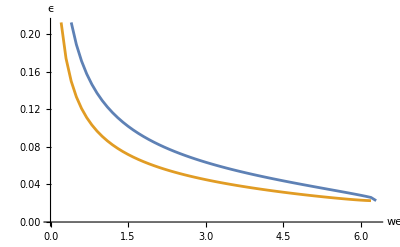

```mathematica
ListLinePlot[{ll,rr},AxesLabel->{"we","ϵ"}]
```

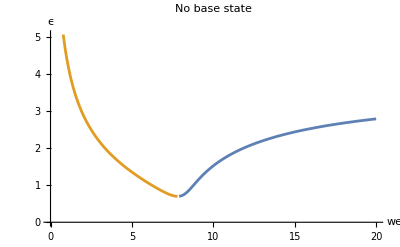

```mathematica
ListLinePlot[{lls,rrs},AxesLabel->{"we","ϵ"},PlotLabel->"No base state"]
```

```mathematica
ContourPlot[{zetak-1-ϵ^2*((1/2) (g2+g3-√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0,zetak-1-ϵ^2*((1/2) (g2+g3+√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0},{we,10,70},{ϵ,0,0.5},Frame->False,Axes->True,AxesLabel->{"We","A/R"}(*,PlotPoints->200*)]
```

-Graphics-

```mathematica
mu1
```

0.71

-Graphics-

```mathematica
zetak
```

zetak

```mathematica
h21eqn[oh_,ρ1_,ρ2_,μ1_,μ2_,m_,n_]
```

```mathematica
Cos[9Pi/8]//N
```

-0.92388

```mathematica
Cos[7Pi/8]//N
```

-0.92388

```mathematica
k212fun=
```

```mathematica
k212fun=Integrate[TrigReduce[(D[eta1,θ]*D[phi12,θ]+(1/Sin[θ])^2*(D[eta1,φ]*D[phi12,φ])+D[eta2,θ]*D[phi11,θ]+(1/Sin[θ])^2*(D[eta2,φ]*D[phi11,φ])+eta1(D[phi11,r,θ]*D[eta1,θ]+1/Sin[θ]^2*(D[eta1,φ]*D[phi11,r,φ])-2*D[phi11,θ]*D[eta1,θ]-2/Sin[θ]^2*(D[phi11,φ]*D[eta1,φ]))-eta2*D[phi11,r,r]-eta1*D[phi12,r,r]-eta1^2/2*D[phi11,r,r,r])-(D[eta1,θ]*D[phi22,θ]+(1/Sin[θ])^2*(D[eta1,φ]*D[phi22,φ])+D[eta2,θ]*D[phi21,θ]+(1/Sin[θ])^2*(D[eta2,φ]*D[phi21,φ])+eta1(D[phi21,r,θ]*D[eta1,θ]+1/Sin[θ]^2*(D[eta1,φ]*D[phi21,r,φ])-2*D[phi21,θ]*D[eta1,θ]-2/Sin[θ]^2*(D[phi21,φ]*D[eta1,φ]))-eta2*D[phi21,r,r]-eta1*D[phi22,r,r]-eta1^2/2*D[phi21,r,r,r])]*realkl[2,1]*Sin[θ],{θ,0,Pi/2},{φ,0,2 Pi}]/.r->1//N//Simplify
```

0.426308 b020^2 b021t+0.568411 b021^2 b021t+0.434059 b021t b030^2-0.11264 b021t b120-0.11264 b020t b121+0.204081 b030t b121+b020 (0.142103 b020t b021+0.643654 b021t b030+0.193096 b021 b030t-0.11264 b121t-0.11264 k121-0.135168 l121)+0.116618 b030 l121+b021 (0.430442 b030 b030t-0.11264 b120t+0.204081 b130t-0.11264 k120+0.204081 k130-0.135168 l120+0.204081 l130)

```mathematica
phii2t
```

1/8 (b120tt+k120t) √(5/π) r^2 (-1+3 Cos[θ]^2)+1/12 (b130tt+k130t) √(7/π) r^3 (-3 Cos[θ]+5 Cos[θ]^3)-1/4 (b121tt+k121t) √(15/π) r^2 Cos[θ] Cos[φ] Sin[θ]

```mathematica
phi22
```

-((b120t+k120) √(5/π) (-1+3 Cos[θ]^2))/(12 r^3)-((b130t+k130) √(7/π) (-3 Cos[θ]+5 Cos[θ]^3))/(16 r^4)+((b121t+k121) √(5/(3 π)) Cos[θ] Cos[φ] Sin[θ])/(2 r^3)

```mathematica
n212fun=Integrate[TrigReduce[eta1*(D[phi12t,r]-D[phi22t,r])+eta2*(D[phi11t,r]-D[phi21t,r])+eta1^2/2*(D[phi11t,r,r]-D[phi21t,r,r])+(D[phi11*r]*D[phi12,r]-D[phi21*r]*D[phi22,r])+(D[phi11,θ]*D[phi12,θ]-D[phi21,θ]*D[phi22,θ])+1/Sin[θ]^2*(D[phi11,φ]*D[phi12,φ]-D[phi21,φ]*D[phi22,φ])+eta1*(D[phi11,r]*D[phi11,r,r]-D[phi21,r]*D[phi21,r,r])+eta1*(D[phi11,θ]*D[phi11,r,θ]-D[phi21,θ]*D[phi21,r,θ]+1/Sin[θ]^2*D[phi11,φ]*D[phi11,r,φ]-1/Sin[θ]^2*D[phi21,φ]*D[phi21,r,φ]-D[phi11,θ]^2+D[phi21,θ]^2-1/Sin[θ]^2*D[phi11,φ]+1/Sin[θ]^2*D[phi21,φ])-2/wer*(eta1*((1-2-2^2)*b120*realkl[2,0]+(1-2-2^2)*b121*realkl[2,1]+(1-3-3^2)*b130*realkl[3,0])+eta2*((1-2-2^2)*b020*realkl[2,0]+(1-2-2^2)*b021*realkl[2,1]+(1-3-3^2)*b031*realkl[3,0]))]*realkl[2,1]*Sin[θ],{θ,0,Pi/2},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

0.0710513 b020^2 b021tt+0.213154 b021^2 b021tt+0.0306502 b020t b021t b030+0.0874146 b021tt b030^2+0.35629 b021t b030 b030t+0.0563199 b021t b120t+0.0563199 b020t b121t-0.0631679 b030t b121t-0.0777451 b021t b130t+0.0563199 b021t k120+0.0563199 b020t k121-0.0631679 b030t k121-0.0777451 b021t k130+0.0145772 b030t l121+b020 (0.165786 b020t b021t+0.0919505 b021tt b030+0.151718 b021t b030t-0.0450559 l121t)+0.0583088 b030 l121t+0.00971813 b021t l130+(0.901119 b020 b121)/wer-(0.583088 b030 b121)/wer-(1.28279 b031 b121)/wer+1/wer b021 (0.901119 b120-1.86588 b130+(0.37894 b020t^2+0.142103 b020 b020tt+0.553608 b021t^2+0.0919505 b020tt b030+0.634459 b020t b030t+0.523282 b030t^2+0.128731 b020 b030tt+0.244761 b030 b030tt-0.0450559 l120t+0.0583088 l130t) wer)

```mathematica
l212fun=Integrate[TrigReduce[eta1*D[phi12,r,r]+eta2*D[phi11,r,r]+1/2*eta1^2*D[phi11,r,r,r]-(eta1*D[phi22,r,r]+eta2*D[phi21,r,r]+1/2*eta1^2*D[phi21,r,r,r])]*realkl[2,1]*Sin[θ],{θ,0,Pi/2},{φ,0,2 Pi}]/.r->1//N//Simplify//Chop
```

-0.284205 b020^2 b021t-0.852616 b021^2 b021t-0.349659 b021t b030^2+0.22528 b021t b120+0.22528 b020t b121-0.408162 b030t b121-0.291544 b030 b121t-0.291544 b021t b130-0.291544 b030 k121+b020 (-0.568411 b020t b021-0.367802 b021t b030-0.514923 b021 b030t+0.22528 b121t+0.22528 k121+0.180224 l121)-0.233235 b030 l121+b021 (-0.367802 b020t b030-0.979044 b030 b030t+0.22528 b120t-0.408162 b130t+0.22528 k120-0.408162 k130+0.180224 l120-0.291544 l130)

```mathematica
v31term=eta1*D[phi2t,r]+eta2*D[phi1t,r]+D[phi1*r]*D[phi2,r]+D[phi1,θ]*D[phi2,θ]+1/Sin[θ]^2*D[phi1,φ]*D[phi2,φ](*+2/wer*(eta1*((1-2-2^2)*b120*SphericalHarmonicY[2,0,θ,φ]+(1-3-3^2)*b131*realkl[3,1]+(1-4-4^2)*b140*SphericalHarmonicY[4,0,θ,φ])+eta2*((1-2-2^2)*b020*SphericalHarmonicY[2,0,θ,φ]+(1-3-3^2)*b031*realkl[3,1]+(1-4-4^2)*b040*SphericalHarmonicY[4,0,θ,φ]))*);
```

```mathematica
Clear[k120f]
```

```mathematica
k201f[0.02,0.7,0.5,0.5,0.5,2]
```

-0.004703 Cos[2 t]-0.00910368 c0 Cos[2 t]+0.111069 d0 Cos[2 t]+0.135168 c0 d0 Cos[2 t]-0.120336 Sin[2 t]-0.111069 c0 Sin[2 t]-0.0675839 c0^2 Sin[2 t]-0.00910368 d0 Sin[2 t]+0.0675839 d0^2 Sin[2 t]

```mathematica
b020
```

1.23256 Cos[t]+c0 Cos[t]-0.101026 Sin[t]+d0 Sin[t]

```mathematica
bkl0fun[0.02,0.7,0.5,0.5,0.5,2,0,2]
```

```mathematica
k201f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,p20now,p31now,p40now,b020t,b020tt,b022,b022t,b022tt,b051,b051t,b051tt,b031,b031t,b031tt,b040,b040t,b040tt,b042,b042t,b042tt,b060,b060t,b060tt];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;
b021t=D[b021,t]//Simplify;
b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;
b021tt=D[b021,t,t]//Simplify;
b030tt=D[b030,t,t]//Simplify;

k120ff=0.09011187578643427 b020 b020t+0.045055937893217136 b021 b021t+0.168208834801344 b030 b030t;
k1klnow=k120ff//TrigReduce//Chop)
```

```mathematica
k211f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,p20now,p31now,p40now,b020t,b020tt,b022,b022t,b022tt,b051,b051t,b051tt,b031,b031t,b031tt,b040,b040t,b040tt,b042,b042t,b042tt,b060,b060t,b060tt];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;
b021t=D[b021,t]//Simplify;
b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;
b021tt=D[b021,t,t]//Simplify;
b030tt=D[b030,t,t]//Simplify;

k121ff=0.04505593789321714 (b020t b021+b020 b021t);
k1klnow=k121ff//TrigReduce//Chop)
```

```mathematica
Clear[k121f]
```

```mathematica
k301f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,b020t,b020tt,b022,b022t,b022tt,b051,b051t,b051tt,b031,b031t,b031tt,b040,b040t,b040tt,b042,b042t,b042tt,b060,b060t,b060tt,k301ff,k1klnow];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;
b021t=D[b021,t]//Simplify;
b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;
b021tt=D[b021,t,t]//Simplify;
b030tt=D[b030,t,t]//Simplify;

k301ff=0.084104417400672 b020t b030-0.168208834801344 b020 b030t;
k1klnow=k301ff//TrigReduce//Chop)
```

```mathematica
Clear[k130f]
```

```mathematica
n201f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,p20now,p31now,p40now,b020t,b020tt,b022,b022t,b022tt,b051,b051t,b051tt,b031,b031t,b031tt,b040,b040t,b040tt,b042,b042t,b042tt,b060,b060t,b060tt];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;
b021t=D[b021,t]//Simplify;
b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;
b021tt=D[b021,t,t]//Simplify;
b030tt=D[b030,t,t]//Simplify;

n120ff=1/wer(1.8022375157286856 b020^2+0.9011187578643428 b021^2+3.700594365629568 b030^2+0.037546614911014284 b020t^2 wer+0.018773307455507142 b021t^2 wer+0.036795682612794 b030t^2 wer);
n1klnow=n120ff//TrigReduce//Chop)
```

```mathematica
Clear[n120f]
```

```mathematica
n211f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,p20now,p31now,p40now,b020t,b020tt,b022,b022t,b022tt,b051,b051t,b051tt,b031,b031t,b031tt,b040,b040t,b040tt,b042,b042t,b042tt,b060,b060t,b060tt];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;
b021t=D[b021,t]//Simplify;
b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;
b021tt=D[b021,t,t]//Simplify;
b030tt=D[b030,t,t]//Simplify;

n121ff=-0.03754661491101429 b020t b021t+(1.8022375157286858 b020 b021)/wer;
n1klnow=n121ff//TrigReduce//Chop)
```

```mathematica
n301f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,b020t,b020tt,b022,b022t,b022tt,b051,b051t,b051tt,b031,b031t,b031tt,b040,b040t,b040tt,b042,b042t,b042tt,b060,b060t,b060tt,n130ff,n1klnow];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;
b021t=D[b021,t]//Simplify;
b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;
b021tt=D[b021,t,t]//Simplify;
b030tt=D[b030,t,t]//Simplify;

n130ff=0.042052208700336 b020t b030t+(5.382682713643008 b020 b030)/wer;
n1klnow=n130ff//TrigReduce//Chop)
```

```mathematica
Clear[n130f]
```

```mathematica
l201f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,p20now,p31now,p40now,b020t,b020tt,b022,b022t,b022tt,b051,b051t,b051tt,b031,b031t,b031tt,b040,b040t,b040tt,b042,b042t,b042tt,b060,b060t,b060tt];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;
b021t=D[b021,t]//Simplify;
b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;
b021tt=D[b021,t,t]//Simplify;
b030tt=D[b030,t,t]//Simplify;

l120ff=0.9011187578643428 b020 b020t+0.4505593789321714 b021 b021t+1.177461843609408 b030 b030t;
l1klnow=l120ff//TrigReduce//Chop)
```

```mathematica
l211f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,p20now,p31now,p40now,b020t,b020tt,b022,b022t,b022tt,b051,b051t,b051tt,b031,b031t,b031tt,b040,b040t,b040tt,b042,b042t,b042tt,b060,b060t,b060tt];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;
b021t=D[b021,t]//Simplify;
b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;
b021tt=D[b021,t,t]//Simplify;
b030tt=D[b030,t,t]//Simplify;

l121ff=0.4505593789321715 (b020t b021+b020 b021t);
l1klnow=l121ff//TrigReduce//Chop)
```

```mathematica
l301f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,p20now,p31now,p40now,b020t,b020tt,b022,b022t,b022tt,b051,b051t,b051tt,b031,b031t,b031tt,b040,b040t,b040tt,b042,b042t,b042tt,b060,b060t,b060tt];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;
b021t=D[b021,t]//Simplify;
b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;
b021tt=D[b021,t,t]//Simplify;
b030tt=D[b030,t,t]//Simplify;

l121ff=0.8410441740067199 b020t b030+1.177461843609408 b020 b030t;
l1klnow=l121ff//TrigReduce//Chop)
```

```mathematica
Integrate[eta1*(a1*realkl[2,0]+a3*realkl[3,0])*realkl[2,0],{θ,0,Pi},{φ,0,2 Pi}]
```

(5 (232 a1 b020+259 a3 b030) √(5 π))/4096

```mathematica
nm0[k_]:=√((2k+1)/(4*Pi));
```

```mathematica
n201f[0,0,1,0,0,2]
```

64.6106-0.355257 c0+0.1408 c0^2+0.1408 d0^2+50.7729 Cos[2 t]-0.213154 c0 Cos[2 t]+0.0844799 c0^2 Cos[2 t]-0.0844799 d0^2 Cos[2 t]-0.213154 d0 Sin[2 t]+0.16896 c0 d0 Sin[2 t]

```mathematica
t201=Integrate[eta1*(mkl[2,0]*realkl[2,0]+mkl[2,1]*realkl[2,1]+mkl[3,0]*realkl[3,0])*realkl[2,0],{θ,0,Pi},{φ,0,2 Pi}];
```

```mathematica
b201[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[f1,f2,f3,f4,f5,f44,f55,Δk,k,eta1,b020,b021,b030,forcing201];k=2;l=0;
eta1=b020*realkl[2,0]+(b021)*realkl[2,1]+b030*realkl[3,0];
tkl1=Integrate[eta1*(mkl[2,0]*realkl[2,0]+mkl[2,1]*realkl[2,1]+mkl[3,0]*realkl[3,0])*realkl[2,0]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}];
nkl1=n201f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
kkl1=k201f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
lkl1=l201f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
kkl1t=D[kkl1,t];
lkl1t=D[lkl1,t];
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
δ=oh/(√wer);
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wer));fk=(k(k+1))/(ρ1(k+1)+ρ2*k);
Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;gk=(ρ2*k)/(ρ1*(k+1)+ρ2*k);hk=2δ*μ2*(k+2);
forcing201=(ρ2-ρ1)*fk*tkl1*Sin[t]-kkl1t-2*Δk*kkl1-gk*lkl1t-hk*lkl1-fk*nkl1;
f1=Integrate[(1/(2Pi))*forcing201,{t,-Pi,Pi}];
f44=Integrate[(1/Pi)*forcing201*Cos[2t],{t,-Pi,Pi}];f55=Integrate[(1/Pi)*forcing201*Sin[2t],{t,-Pi,Pi}];
(*Δk=delta*(k+1)*(k+2);ζk=√((1/wer)(k^2-1)(k+2));*)f4=f44;f5=f55;

b201sol=f1/ζk^2+((-4 f5 Δk+f4 (-4+ζk^2)) Cos[2 t]+(4 f4 Δk+f5 (-4+ζk^2)) Sin[2 t])/(16 Δk^2+(-4+ζk^2)^2)//TrigReduce//Simplify//Chop)
```

```mathematica
forcing201
```

0.+0.195146 Cos[2 t]+0.208392 c0 Cos[2 t]+0.135168 c0^2 Cos[2 t]-0.135168 d0^2 Cos[2 t]-0.000513647 Sin[t] (14 √35 (0.-0.666243 Cos[t])+75 (0.+1.1563 Cos[t]+c0 Cos[t]+d0 Sin[t]))+0.208392 d0 Sin[2 t]+0.270336 c0 d0 Sin[2 t]-0.332226 (-1.72746 Cos[2 t]-2.08392 c0 Cos[2 t]-1.35168 c0^2 Cos[2 t]+1.35168 d0^2 Cos[2 t]-2.08392 d0 Sin[2 t]-2.70336 c0 d0 Sin[2 t])-1.99336 (0.20211+0.217075 c0+0.1408 c0^2+0.1408 d0^2+0.135577 Cos[2 t]+0.130245 c0 Cos[2 t]+0.0844799 c0^2 Cos[2 t]-0.0844799 d0^2 Cos[2 t]+0.130245 d0 Sin[2 t]+0.16896 c0 d0 Sin[2 t])

```mathematica
b020
```

1.14703 Cos[t]+c0 Cos[t]-0.103071 Sin[t]+d0 Sin[t]

```mathematica
b201[0.02,0.67,0.5,0.5,0.5,2]
```

-0.397452-0.429241 c0-0.280664 c0^2+0.0193092 d0-0.280664 d0^2+(-0.162486-0.138668 c0^2+c0 (-0.212723+0.0104421 d0)-0.0174917 d0+0.138668 d0^2) Cos[2 t]+(0.0125894+0.0174917 c0-0.00522106 c0^2-0.212723 d0-0.277337 c0 d0+0.00522106 d0^2) Sin[2 t]

```mathematica
b301[0,0.67,0.5,0,0,2]
```

0.108143+0.093525 c0-0.00610663 d0+(0.505873+0.805274 c0+0.318067 c0^2+0.0301327 d0-0.318067 d0^2) Cos[2 t]+(-0.0178752-0.0301327 c0+0.805274 d0+0.636134 c0 d0) Sin[2 t]

```mathematica
b030
```

0.-0.666243 Cos[t]

```mathematica
b211[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[f1,f2,f3,f4,f5,Δk,k,eta1,b020,b021,b030,forcing211];k=2;l=1;
eta1=b020*realkl[2,0]+(b021)*realkl[2,1]+b030*realkl[3,0];
tkl1=Integrate[eta1*(mkl[2,0]*realkl[2,0]+mkl[2,1]*realkl[2,1]+mkl[3,0]*realkl[3,0])*realkl[k,l]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}];
nkl1=n211f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
kkl1=k211f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
lkl1=l211f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
kkl1t=D[kkl1,t];
lkl1t=D[lkl1,t];
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
δ=oh/(√wer);
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wer));fk=(k(k+1))/(ρ1(k+1)+ρ2*k);
Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;gk=(ρ2*k)/(ρ1*(k+1)+ρ2*k);hk=2δ*μ2*(k+2);
forcing201=(ρ2-ρ1)*fk*tkl1*Sin[t]-kkl1t-2*Δk*kkl1-gk*lkl1t-hk*lkl1-fk*nkl1;
f1=Integrate[(1/(2Pi))*forcing201,{t,-Pi,Pi}];
f4=Integrate[(1/Pi)*forcing201*Cos[2t],{t,-Pi,Pi}];f5=Integrate[(1/Pi)*forcing201*Sin[2t],{t,-Pi,Pi}];
(*Δk=delta*(k+1)*(k+2);ζk=√((1/wer)(k^2-1)(k+2));*)

b201sol=f1/ζk^2+((-4 f5 Δk+f4 (-4+ζk^2)) Cos[2 t]+(4 f4 Δk+f5 (-4+ζk^2)) Sin[2 t])/(16 Δk^2+(-4+ζk^2)^2)//TrigReduce//Simplify//Chop)
```

```mathematica
b301[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[f1,f2,f3,f4,f5,Δk,k,eta1,b020,b021,b030,forcing301];k=3;l=0;
eta1=b020*realkl[2,0]+(b021)*realkl[2,1]+b030*realkl[3,0];
tkl1=Integrate[eta1*(mkl[2,0]*realkl[2,0]+mkl[2,1]*realkl[2,1]+mkl[3,0]*realkl[3,0])*realkl[k,l]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}];
nkl1=n301f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
kkl1=k301f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
lkl1=l301f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
kkl1t=D[kkl1,t];
lkl1t=D[lkl1,t];
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wer));fk=(k(k+1))/(ρ1(k+1)+ρ2*k);
Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;gk=(ρ2*k)/(ρ1*(k+1)+ρ2*k);hk=2δ*μ2*(k+2);
forcing301=(ρ2-ρ1)*fk*tkl1*Sin[t]-kkl1t-2*Δk*kkl1-gk*lkl1t-hk*lkl1-fk*nkl1;
f1=Integrate[(1/(2Pi))*forcing301,{t,-Pi,Pi}];
f4=Integrate[(1/Pi)*forcing301*Cos[2t],{t,-Pi,Pi}];f5=Integrate[(1/Pi)*forcing301*Sin[2t],{t,-Pi,Pi}];
Δk=delta*(k+1)*(k+2);ζk=√((1/wer)(k^2-1)(k+2));

b301sol=f1/ζk^2+((-4 f5 Δk+f4 (-4+ζk^2)) Cos[2 t]+(4 f4 Δk+f5 (-4+ζk^2)) Sin[2 t])/(16 Δk^2+(-4+ζk^2)^2)//TrigReduce//Simplify//Chop)
```

```mathematica
b301[0.026,2,1,1,1,2]
```

0.0872234+0.135277 c0-0.166881 d0+(0.276356-0.326047 c0-0.900938 d0) Cos[2 t]+(1.63569+0.900938 c0-0.326047 d0) Sin[2 t]

```mathematica
t2kl[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,kr_]:=(Clear[c0,d0,b020,p20now,p31now,p40now,b020t,b020tt,b022,b022t,b022tt,b051,b051t,b051tt,b031,b031t,b031tt,b040,b040t,b040tt,b042,b042t,b042tt,b060,b060t,b060tt];

wer=(kr^2-1)(kr+2);(*weber number for the resonance mode*)
delta=oh/(√wer);
b120=b201[oh,ρ1,ρ2,μ1,μ2,2,0,kr];
b121=b211[oh,ρ1,ρ2,μ1,μ2,2,1,kr];
b130=b301[oh,ρ1,ρ2,μ1,μ2,3,0,kr];
eta2=b120*realkl[2,0]+(b121)*realkl[2,1]+b130*realkl[3,0];
tkl1=Integrate[eta2*(nm0[2]*realkl[2,0]+nm0[3]*realkl[3,0])*realkl[k,l],{θ,0,Pi},{φ,0,2 Pi}]//TrigReduce//Chop)
```

```mathematica
k212f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,b021,b030,b020t,b020tt,b021t,b021tt,b030t,b030tt,b120,b121,b130,k120,k121,k130,l120,l121,l130,b120t,b121t,b130t,k212ff,k2klnow];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;b021t=D[b021,t]//Simplify;b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;b021tt=D[b021,t,t]//Simplify;b030tt=D[b030,t,t]//Simplify;
b120=b201[oh,ρ1,ρ2,μ1,μ2,kr,lr];
b121=b211[oh,ρ1,ρ2,μ1,μ2,kr,lr];
b130=b301[oh,ρ1,ρ2,μ1,μ2,kr,lr];
k120=k201f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
k121=k211f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
k130=k301f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
l120=l201f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
l121=l211f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
l130=l301f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
b120t=D[b120,t];b121t=D[b121,t];b130t=D[b130,t];

k212ff=0.42630788328186253 b020^2 b021t+0.5684105110424833 b021^2 b021t+0.43405893570516907 b021t b030^2-0.11263984473304287 b021t b120-0.11263984473304287 b020t b121+0.20408080688521937 b030t b121+b020 (0.14210262776062083 b020t b021+0.6436536512152659 b021t b030+0.1930960953645798 b021 b030t-0.11263984473304288 b121t-0.11263984473304288 k121-0.13516781367965144 l121)+0.11661760393441106 b030 l121+b021 (0.43044177790762606 b030 b030t-0.11263984473304287 b120t+0.20408080688521937 b130t-0.11263984473304287 k120+0.20408080688521937 k130-0.13516781367965144 l120+0.20408080688521937 l130);
k2klnow=k212ff//TrigReduce//Chop)
```

```mathematica
k212f[0.02,0.7,0.5,0.5,0.5,2]
```

-0.0877897 c0 Cos[t]-0.0559945 c0^2 Cos[t]+0.000519548 c0^3 Cos[t]+0.15 d0 Cos[t]+0.295317 c0 d0 Cos[t]+0.256107 c0^2 d0 Cos[t]-0.093676 d0^2 Cos[t]+0.000519548 c0 d0^2 Cos[t]+0.256107 d0^3 Cos[t]-0.104832 c0 Cos[3 t]-0.113301 c0^2 Cos[3 t]+0.00155864 c0^3 Cos[3 t]+0.0867123 d0 Cos[3 t]+0.222335 c0 d0 Cos[3 t]+0.70778 c0^2 d0 Cos[3 t]+0.113301 d0^2 Cos[3 t]-0.00467593 c0 d0^2 Cos[3 t]-0.235927 d0^3 Cos[3 t]-0.141883 c0 Sin[t]-0.154999 c0^2 Sin[t]-0.256107 c0^3 Sin[t]+0.0622896 d0 Sin[t]+0.0376815 c0 d0 Sin[t]+0.000519548 c0^2 d0 Sin[t]+0.140319 d0^2 Sin[t]-0.256107 c0 d0^2 Sin[t]+0.000519548 d0^3 Sin[t]-0.0867123 c0 Sin[3 t]-0.111168 c0^2 Sin[3 t]-0.235927 c0^3 Sin[3 t]-0.104832 d0 Sin[3 t]-0.226602 c0 d0 Sin[3 t]+0.00467593 c0^2 d0 Sin[3 t]+0.111168 d0^2 Sin[3 t]+0.70778 c0 d0^2 Sin[3 t]-0.00155864 d0^3 Sin[3 t]

```mathematica
n212f[0.02,0.7,0.5,0.5,0.5,2]
```

0.141527 c0 Cos[t]+0.103311 c0^2 Cos[t]-0.0388695 c0^3 Cos[t]+0.0338048 d0 Cos[t]-0.0360173 c0 d0 Cos[t]+0.000865913 c0^2 d0 Cos[t]+0.0460325 d0^2 Cos[t]-0.0388695 c0 d0^2 Cos[t]+0.000865913 d0^3 Cos[t]-0.0259412 c0 Cos[3 t]-0.0668027 c0^2 Cos[3 t]-0.329783 c0^3 Cos[3 t]-0.0078983 d0 Cos[3 t]-0.0959533 c0 d0 Cos[3 t]-0.000519548 c0^2 d0 Cos[3 t]+0.0668027 d0^2 Cos[3 t]+0.989348 c0 d0^2 Cos[3 t]+0.000173183 d0^3 Cos[3 t]+0.0042258 c0 Cos[t] k130f[0.02,0.7,0.5,0.5,0.5,2]+0.0534873 c0 Sin[t]+0.0694006 c0^2 Sin[t]-0.000865913 c0^3 Sin[t]-0.0514432 d0 Sin[t]+0.0572783 c0 d0 Sin[t]-0.0388695 c0^2 d0 Sin[t]+0.0333833 d0^2 Sin[t]-0.000865913 c0 d0^2 Sin[t]-0.0388695 d0^3 Sin[t]+0.0042258 d0 k130f[0.02,0.7,0.5,0.5,0.5,2] Sin[t]+0.0078983 c0 Sin[3 t]+0.0479767 c0^2 Sin[3 t]+0.000173183 c0^3 Sin[3 t]-0.0259412 d0 Sin[3 t]-0.133605 c0 d0 Sin[3 t]-0.989348 c0^2 d0 Sin[3 t]-0.0479767 d0^2 Sin[3 t]-0.000519548 c0 d0^2 Sin[3 t]+0.329783 d0^3 Sin[3 t]

```mathematica
n212f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,b021,b030,b020t,b020tt,b021t,b021tt,b030t,b030tt,b120,b121,b130,k120,k121,k130,l120,l121,l130,b120t,b121t,b130t,n212ff,n2klnow];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;b021t=D[b021,t]//Simplify;b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;b021tt=D[b021,t,t]//Simplify;b030tt=D[b030,t,t]//Simplify;
b120=b201[oh,ρ1,ρ2,μ1,μ2,kr,lr];
b121=b211[oh,ρ1,ρ2,μ1,μ2,kr,lr];
b130=b301[oh,ρ1,ρ2,μ1,μ2,kr,lr];
k120=k201f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
k121=k211f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
k130=k301f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
l120=l201f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
l121=l211f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
l130=l301f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
b120t=D[b120,t];b121t=D[b121,t];b130t=D[b130,t];
l120t=D[l120,t];l121t=D[l121,t];l130t=D[l130,t];


n212ff=0.07105131388031043 b020^2 b021tt+0.21315394164093127 b021^2 b021tt+0.030650173867393618 b020t b021t b030+0.08741464677395767 b021tt b030^2+0.356290043057993 b021t b030 b030t+0.05631992236652144 b021t b120t+0.05631992236652144 b020t b121t-0.063167868797806 b030t b121t-0.07774506928960738 b021t b130t+0.05631992236652144 b021t k120+0.05631992236652144 b020t k121-0.063167868797806 b030t k121-0.07774506928960738 b021t k130+0.014577200491801383 b030t l121+b020 (0.16578639905405768 b020t b021t+0.09195052160218087 b021tt b030+0.1517183606435984 b021t b030t-0.04505593789321715 l121t)+0.058308801967205545 b030 l121t+0.009718133661200922 b021t l130+(0.9011187578643429 b020 b121)/wer-(0.5830880196720554 b030 b121)/wer+1/wer b021 (0.9011187578643429 b120-1.865881662950577 b130+(0.37894034069498894 b020t^2+0.14210262776062085 b020 b020tt+0.5536081539840855 b021t^2+0.09195052160218087 b020tt b030+0.634458599055048 b020t b030t+0.5232821613778984 b030t^2+0.1287307302430532 b020 b030tt+0.2447610109670815 b030 b030tt-0.04505593789321714 l120t+0.05830880196720553 l130t) wer);
n2klnow=n212ff//TrigReduce//Chop)
```

```mathematica
l212f[oh_,ρ1_,ρ2_,μ1_,μ2_,kr_,lr_]:=(Clear[c0,d0,b020,b021,b030,b020t,b020tt,b021t,b021tt,b030t,b030tt,b120,b121,b130,k120,k121,k130,l120,l121,l130,b120t,b121t,b130t,l212ff,l2klnow];

wer=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);(*weber number for the resonance mode*)
delta=oh/(√wer);
b020=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,0,kr,lr];
b021=bkl0fun[oh,ρ1,ρ2,μ1,μ2,2,1,kr,lr];
b030=bkl0fun[oh,ρ1,ρ2,μ1,μ2,3,0,kr,lr];
b020t=D[b020,t]//Simplify;b021t=D[b021,t]//Simplify;b030t=D[b030,t]//Simplify;
b020tt=D[b020,t,t]//Simplify;b021tt=D[b021,t,t]//Simplify;b030tt=D[b030,t,t]//Simplify;
b120=b201[oh,ρ1,ρ2,μ1,μ2,kr,lr];
b121=b211[oh,ρ1,ρ2,μ1,μ2,kr,lr];
b130=b301[oh,ρ1,ρ2,μ1,μ2,kr,lr];
k120=k201f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
k121=k211f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
k130=k301f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
l120=l201f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
l121=l211f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
l130=l301f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
b120t=D[b120,t];b121t=D[b121,t];b130t=D[b130,t];
l120t=D[l120,t];l121t=D[l121,t];l130t=D[l130,t];



l212ff=-0.2842052555212417 b020^2 b021t-0.8526157665637251 b021^2 b021t-0.3496585870958307 b021t b030^2+0.22527968946608573 b021t b120+0.22527968946608573 b020t b121-0.40816161377043875 b030t b121-0.2915440098360277 b030 b121t-0.2915440098360277 b021t b130-0.2915440098360277 b030 k121+b020 (-0.5684105110424834 b020t b021-0.36780208640872347 b021t b030-0.5149229209722128 b021 b030t+0.22527968946608576 b121t+0.22527968946608576 k121+0.18022375157286857 l121)-0.23323520786882213 b030 l121+b021 (-0.36780208640872347 b020t b030-0.979044043868326 b030 b030t+0.22527968946608573 b120t-0.40816161377043875 b130t+0.22527968946608573 k120-0.40816161377043875 k130+0.18022375157286857 l120-0.2915440098360277 l130);
l2klnow=l212ff//TrigReduce//Chop)
```

```mathematica
bkl0fun[0.02,0.7,0.5,0.5,0.5,2,0,2,1]
```

0.-9.76696 Sin[t]

```mathematica
b020
```

0.-9.76696 Sin[t]

```mathematica
k212f[0.02,0.7,0.5,0.5,0.5,2,1]
```

0.139615 c0 Cos[t]+2.09011 d0 Cos[t]-9.86024 c0 Cos[1. t]+0.000109138 c0^3 Cos[1. t]+298.137 d0 Cos[1. t]+0.134504 c0^2 d0 Cos[1. t]+0.000109138 c0 d0^2 Cos[1. t]+0.134504 d0^3 Cos[1. t]+0.0539565 c0 Cos[3 t]+1.27763 d0 Cos[3 t]-10.4138 c0 Cos[3. t]+0.000327414 c0^3 Cos[3. t]-297.275 d0 Cos[3. t]+0.40679 c0^2 d0 Cos[3. t]-0.000982242 c0 d0^2 Cos[3. t]-0.135597 d0^3 Cos[3. t]-3.30591 c0 Sin[t]+0.139615 d0 Sin[t]-357.469 c0 Sin[1. t]-0.134504 c0^3 Sin[1. t]+9.86024 d0 Sin[1. t]+0.000109138 c0^2 d0 Sin[1. t]-0.134504 c0 d0^2 Sin[1. t]+0.000109138 d0^3 Sin[1. t]-1.27763 c0 Sin[3 t]+0.0539565 d0 Sin[3 t]+297.275 c0 Sin[3. t]-0.135597 c0^3 Sin[3. t]-10.4138 d0 Sin[3. t]+0.000982242 c0^2 d0 Sin[3. t]+0.40679 c0 d0^2 Sin[3. t]-0.000327414 d0^3 Sin[3. t]

```mathematica
forcing201=(ρ2-ρ1)*fk*tkl1*Sin[t]-kkl1t-2*Δk*kkl1-gk*lkl1t-hk*lkl1-fk*nkl1;
```

```mathematica
harmonic21[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,kr_,lr_]:=(Clear[c0,d0,b020,b021,b030,b020t,b020tt,b021t,b021tt,b030t,b030tt,b120,b121,b130,k120,k121,k130,l120,l121,l130,b120t,b121t,b130t,tkl1,tkl2,eta1,fk,b211sol];
eta2=(*b120*realkl[2,0]+*)b211sol*realkl[2,1](*+b130*realkl[3,0]*);
tkl2=Integrate[eta2*(mkl[2,0]*realkl[2,0]+mkl[2,1]*realkl[2,1]+mkl[3,0]*realkl[3,0])*realkl[k,l]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}];
wek=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);
delta=oh/wek;
ζk=√((k(k+1)(k^2+k-2))/((ρ1*(k+1)+ρ2*k)wer));fk=(k(k+1))/(ρ1(k+1)+ρ2*k);
Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;gk=(ρ2*k)/(ρ1*(k+1)+ρ2*k);hk=2δ*μ2*(k+2);
zetak=wer/we;
b211sol=b211[oh,ρ1,ρ2,μ1,μ2,kr,lr];
kkl2=k212f[oh,ρ1,ρ2,μ1,μ2,kr,lr];kkl2t=D[kkl2,t];
nkl2=n212f[oh,ρ1,ρ2,μ1,μ2,kr,lr];
lkl2=l212f[oh,ρ1,ρ2,μ1,μ2,kr,lr];lkl2t=D[lkl2,t];
forcing212=(ρ2-ρ1)*fk*tkl2*Sin[t]-kkl2t-2*Δk*kkl2-gk*lkl2t-hk*lkl2-fk*nkl2;//TrigReduce;
fcos=Integrate[(1/Pi)*forcing212*Cos[t],{t,-Pi,Pi}];
fsin=Integrate[(1/Pi)*forcing212*Sin[t],{t,-Pi,Pi}];
g1=Coefficient[fsin,c0]-Coefficient[fsin,c0*d0^2]*d0^2//FullSimplify//Chop;g2=Coefficient[fsin,d0]-Coefficient[fsin,d0*c0^2]*c0^2//FullSimplify//Chop;g3=Coefficient[fcos,c0]-Coefficient[fcos,c0*d0^2]*d0^2//FullSimplify//Chop;g4=Coefficient[fcos,d0]-Coefficient[fcos,d0*c0^2]*c0^2//FullSimplify//Chop;
α=Coefficient[fcos,c0^3]//Chop;
β=Coefficient[fcos,d0^3]//Chop;

wek=(kr(kr+1)(kr^2+kr-2))/(ρ1*(kr+1)+ρ2*kr);
delta=oh/(√wek);
Δk=delta(μ1*(k-1)+μ2*(k+2))*fk;
data={g1,g2,g3,g4,α,β,Δk,wer}(*;ContourPlot[{zetak-1-ϵ^2*((1/2) (g2+g3-√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0,zetak-1-ϵ^2*((1/2) (g2+g3+√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0},{we,10,70},{ϵ,0,0.5},Frame->False,Axes->True,AxesLabel->{"We","A/R"}(*,PlotPoints->200*)]*)
)
```

```mathematica
harmonic21[0.02,0.7,0.5,0.5,0.5,2,1,2,1]
```

{13.5044,-844.346,-689.325,22.751,-0.400045,0.00570439,0.0501485,27.907}

```mathematica
(g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4
```

24031.6+(4 (0.100297+13.5044 ϵ^2) (-0.100297+22.751 ϵ^2))/ϵ^4

```mathematica
Solve[24031.60632735587+(4 (0.10029701698998988+13.504418503560936 ϵ^2) (-0.10029701698998988+22.75099356674131 ϵ^2))/ϵ^4==0,ϵ]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{ϵ→-0.0345082},{ϵ→0.-0.0365742 ⅈ},{ϵ→0.+0.0365742 ⅈ},{ϵ→0.0345082}}

```mathematica
ContourPlot[{zetak-1-ϵ^2*((1/2) (g2+g3-√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0,zetak-1-ϵ^2*((1/2) (g2+g3+√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0},{we,10,70},{ϵ,0,5},Frame->False,Axes->True,AxesLabel->{"We","A/R"}(*,PlotPoints->200*)]
```

-Graphics-

```mathematica
Integrate[realkl[2,1]*realkl[2,1]*realkl[2,1](**realkl[2,1]*)*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]
```

0

```mathematica
Integrate[realkl[2,0]*realkl[2,1]*realkl[2,1]*realkl[2,1]*Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]
```

0

```mathematica
Integrate[realkl[3,1]*realkl[3,1]*(*realkl[3,1]**)realkl[3,1]*Sin[θ],{θ,0,Pi/2},{φ,0,2 Pi}]
```

0

```mathematica
harmonic21[0.02,0.7,0.5,0.5,0.5,2,1,2]
```

{-0.0522763-0.463545 d0,-0.531762-0.463545 c0,-0.462766+0.104542 d0,-0.0190573+0.104542 c0,-0.82948,0.0184615,0.0347804,7.74194}

```mathematica
zetak
```

12/we

```mathematica
data
```

{-0.0522763-0.463545 d0,-0.531762-0.463545 c0,-0.462766+0.104542 d0,-0.0190573+0.104542 c0,-0.82948,0.0184615,dkr,7.74194,f31}

```mathematica
g1=-0.05227629836730909;
```

```mathematica
g2=-0.5317623283721141;
```

```mathematica
g3=-0.462765555464534;
```

```mathematica
g4=-0.01905729384330806;
```

```mathematica
Δk=0.01796988221070652*fk
```

0.0501485

```mathematica
ContourPlot[{zetak-1-ϵ^2*((1/2) (g2+g3-√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0,zetak-1-ϵ^2*((1/2) (g2+g3+√((g2-g3)^2+(4 (2 Δk+g1 ϵ^2) (-2 Δk+g4 ϵ^2))/ϵ^4)))==0},{we,10,70},{ϵ,0,0.5},Frame->False,Axes->True,AxesLabel->{"We","A/R"}(*,PlotPoints->200*)]
```

-Graphics-

```mathematica
Integrate[eta2*(mkl[2,0]*realkl[2,0]+mkl[2,1]*realkl[2,1]+mkl[3,0]*realkl[3,0])*realkl[k,l],{θ,0,Pi},{φ,0,2 Pi}]
```

```mathematica
fsin
```

0.-0.0184615 c0^3+c0^2 (-0.032791-0.82948 d0)-0.531762 d0+0.0717511 d0^2-0.82948 d0^3+c0 (-0.0522763-0.463545 d0-0.0184615 d0^2)

```mathematica
harmonic21[oh_,ρ1_,ρ2_,μ1_,μ2_,k_,l_,kr_]
```

```mathematica
harmonic21[0.02,0.7,0.5,0.5,0.5,2,1,2]
```

-Graphics-

```mathematica
DSolve[x''[t]+2*mu*x'[t]+(1/4+mu^2)*x[t]==0,x[t],t]
```

{{x[t]→ⅇ^(-mu t) C[2] Cos[t/2]+ⅇ^(-mu t) C[1] Sin[t/2]}}

```mathematica
DSolve[x''[t]+2*mu*x'[t]+(1/4+mu^2)*x[t]==ⅇ^(-mu t) a Cos[t/2]+ⅇ^(-mu t) b Sin[t/2],x[t],t]
```

{{x[t]→ⅇ^(-mu t) C[2] Cos[t/2]+ⅇ^(-mu t) C[1] Sin[t/2]+ⅇ^(-mu t) (-b t Cos[t/2]+2 a Cos[t/2]^3+a t Sin[t/2]-2 b Cos[t/2]^2 Sin[t/2]+b Cos[t/2] Sin[t]+a Sin[t/2] Sin[t])}}

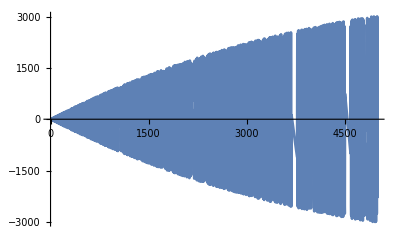

```mathematica
Plot[ⅇ^(-mu t) (-t Cos[t/2])/.mu->0.0001,{t,0,5000}]
```

```mathematica
DSolve[x''[t]+(z^2-d^2)*x[t]==f*E^(d*t)Cos[t],x[t],t]
```

{{x[t]→ⅇ^(t √(d^2-z^2)) C[1]+ⅇ^(-t √(d^2-z^2)) C[2]+(ⅇ^(d t) f (-Cos[t]+z^2 Cos[t]+2 d Sin[t]))/(1+4 d^2-2 z^2+z^4)}}

```mathematica
Series[1/r^3,{r,Infinity,5}]
```

(1/r)^3+O[1/r]^6

```mathematica
Integrate[(E^(-x^2/l^2))/(√Pi)*x^2*1/l,{x,-Infinity,Infinity}]
```

ConditionalExpression[1/(2 (1/l^2)^(3/2) l), Re[l^2]>0]

```mathematica
Clear[k]
```

```mathematica
Integrate[Exp[-(x-y)^2/(4*k*t)]/(√Pi)*x^2*1/l,{x,-Infinity,Infinity}]
```